# Emergent Classicality

The goal is to explore how AI can extract and condense information about a qubit from local weak measurements in the environment that is entangled with the qubit. To demonstrate the idea that classical information is spread from the qubit into the environment and recollected by the intelligence to form emergent reality. Focus on how to quantify the relation between confidence and decoherence.

## Quantum Darwinism

### Measurement Theory

#### General Quantum Measurement

A quantum measurement is described by a set of Kraus operators K_a with the normalization condition

∑_a K_a^†K_a=𝟙.

Each possible index a labels a possible measurement outcome.

Let ρ be a density matrix of a quantum system. It evolves under the measurement as follows:

If unconditioned on the measurement outcome

ρ→∑_a K_a ρ K_a^†,

this will generally result in a mixed state density matrix.

If conditioned on the measurement outcome a

ρ→(K_a ρ K_a^†)/(Tr K_a ρ K_a^†),

and the outcome a appears with the probability

p_a=Tr K_a ρ K_a^†.

Pure state remains pure in this setup (conditioned on the outcome). Eq. (DisplayFormulaNumbered) defines a quantum trajectory of the state ρ.

#### Weak Measurement

Weak measurements are fussy (observer obtain very little information about the quantum system) and gentle (the perturbation to the quantum system is also very little). Krause operators of weak measurements are close to the identity.

For a single qubit, we can have the following schemes.

Binary measurement along a fixed axis

K_(±ϵ)=(σ^0±ϵ σ^z)/(√(2(1+ϵ^2))),

where ϵ controls the measurement strength. The measurement outcome is binary a=±ϵ. The normalization reads

∑_a K_a^†K_a=1/(2(1+ϵ^2))∑_(a=±ϵ) (σ^0+a σ^z)^2=σ^0.

Continuous measurement along any axis

K_ϵ=(σ^0+ϵ·σ)/(√(4π(1+ϵ^2))),

where |ϵ| controls the measurement strength. The measurement outcome is labeled by a three-component real vector ϵ. The normalization reads

∫ⅆϵ K_ϵ^†K_ϵ=1/(1+ϵ^2)∫ⅆϵ/(4π)(σ^0+ϵ·σ)^2=σ^0,

where the integral measure is defined such that ∫ⅆϵ/(4π)=1 (like spherical angle).

#### Quantum Trajectory

Consider a single qubit, its density matrix ρ is universally parameterized by a three-component real vector n (no necessarily unit vector if ρ can be mixed),

ρ=(σ^0+n·σ)/2.

##### Binary Measurement

Conditioned on the outcome a=±ϵ, the n vector evolves as

n_1→((1-a^2)n_1)/(1+2a n_3+a^2),
n_2→((1-a^2)n_2)/(1+2a n_3+a^2),
n_3→((1+a^2)n_3+2a)/(1+2a n_3+a^2),

```mathematica
Collect[(σ[0]+a σ[3])·(σ[0]+n1 σ[1]+n2 σ[2]+n3 σ[3])·(σ[0]+a σ[3]),_σ]
```

(1+a^2+2 a n3) σ[0]+(n1-a^2 n1) σ[1]+(n2-a^2 n2) σ[2]+(2 a+n3+a^2 n3) σ[3]

Details.

with probability

p_(a=±ϵ)=(1+2a n_3+a^2)/(2(1+a^2)).

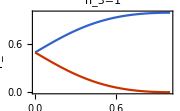

```mathematica
Block[{n3=1},
Plot[Evaluate[(1+2 n3{1,-1}ϵ+ϵ^2)/(2(1+ϵ^2))],{ϵ,0,1},FrameLabel->{"ϵ","\!\(p\_±ϵ\)"},PlotLabel->StringTemplate["\!\(n\_3=`1`\)"][n3],PlotRange->{0,1},PlotRangePadding->Scaled[.05],ImageSize->180]]
```

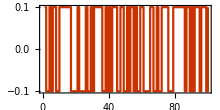
-Graphics3D--Graphics-

```mathematica
Block[{ϵ=0.1,measure,ns,os},
measure[{n1_,n2_,n3_}]:=Block[{ps,a,n},
ps=(1+2ϵ n3{1,-1}+ϵ^2)/(2(1+ϵ^2));
Sow[a=RandomChoice[ps->{ϵ,-ϵ}]];
{(1-a^2)n1,(1-a^2)n2,(1+a^2)n3+2 a}/(1+2 a n3+a^2)];
{ns,{os}}=Reap[NestList[measure,{1,0,0},100]];
Row@{Graphics3D[{First@ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Opacity[0.1],White],MeshStyle->Opacity[0.1]],Point[ns]},Boxed->False,ImageSize->160],
ListLinePlot[os,PlotStyle->Red,FrameLabel->{"step","outcome"},AspectRatio->1/2,InterpolationOrder->0,ImageSize->220]}]
```

The state ρ will be attracted towards the north/south pole while doing random walk along the path. The outcome will gradually become biased by ϵ amount.

##### Continuous Measurement

Conditioned on the outcome ϵ, the n vector evolves as

n→(n(1-ϵ^2)+2ϵ(1+ϵ·n))/(1+2ϵ·n+ϵ^2),

```mathematica
Collect[(σ[0]+ϵ1 σ[1]+ϵ2 σ[2]+ϵ3 σ[3])·(σ[0]+n1 σ[1]+n2 σ[2]+n3 σ[3])·(σ[0]+ϵ1 σ[1]+ϵ2 σ[2]+ϵ3 σ[3]),_σ]
```

(1+2 n1 ϵ1+ϵ1^2+2 n2 ϵ2+ϵ2^2+2 n3 ϵ3+ϵ3^2) σ[0]+(n1+2 ϵ1+n1 ϵ1^2+2 n2 ϵ1 ϵ2-n1 ϵ2^2+2 n3 ϵ1 ϵ3-n1 ϵ3^2) σ[1]+(n2-n2 ϵ1^2+2 ϵ2+2 n1 ϵ1 ϵ2+n2 ϵ2^2+2 n3 ϵ2 ϵ3-n2 ϵ3^2) σ[2]+(n3-n3 ϵ1^2-n3 ϵ2^2+2 ϵ3+2 n1 ϵ1 ϵ3+2 n2 ϵ2 ϵ3+n3 ϵ3^2) σ[3]

Details.

with probability density (upon fixed |ϵ|)

p(ϵ)ⅆϵ=(1+2ϵ·n+ϵ^2)/(4π(1+ϵ^2))ⅆϵ.

In fact, the continuous measurement scheme is equivalent to the binary measurement with a random axis isotropically sampled on the sphere.

To generate random ϵ given n, we can choose to represent ϵ in spherical coordinate with respect to n (as the direction toward the north pole). Let θ be the angle between ϵ and n (i.e. ϵ·n=ϵ n cos θ), Eq. (DisplayFormulaNumbered) induces a distribution of θ

p(θ)ⅆθ=2π sin θⅆθ(1+2ϵ·n+ϵ^2)/(4π(1+ϵ^2))=((1+2 ϵ n cos θ+ϵ^2)sin θ)/(2(1+ϵ^2))ⅆθ,

where ϵ=|ϵ| and n=|n| are the lengths of the vectors. From the probability distribution function p(θ), we can define the cumulative distribution function

x(θ)=∫_0^θ p(θ)ⅆθ=((1+2n ϵ cos^2 θ/2+ϵ^2)sin^2 θ/2)/(1+ϵ^2).

```mathematica
Integrate[(1+2 n ϵ Cos[θ]+ϵ^2)Sin[θ]/(2(1+ϵ^2)),{θ,0,θ}]
```

((1+n ϵ+ϵ^2+n ϵ Cos[θ]) Sin[θ/2]^2)/(1+ϵ^2)

Details.

Its inverse function reads

θ(x)=2 arctan √((2+y)/(2-y)),
y=(1+ϵ^2-√((1+2n ϵ+ϵ^2)^2-8n ϵ (1+ϵ^2)x))/(n ϵ).

```mathematica
Last@Solve[(1+2 n ϵ Cos[θ/2]^2+ϵ^2)Sin[θ/2]^2/(1+ϵ^2)==x,θ]
```

{θ→ConditionalExpression[2 (ArcTan[1/2 √(2-1/(n ϵ)-ϵ/n+(√((-1-2 n ϵ-ϵ^2)^2-8 n ϵ (x+x ϵ^2)))/(n ϵ)),1/2 √(2+1/(n ϵ)+ϵ/n-(√((-1-2 n ϵ-ϵ^2)^2-8 n ϵ (x+x ϵ^2)))/(n ϵ))]+2 π C[1]),C[1]∈ℤ]}

Details.

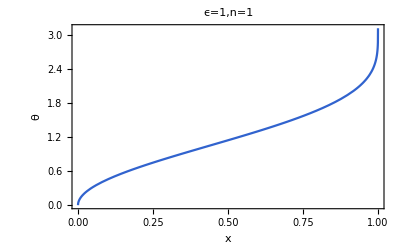

```mathematica
Block[{ϵ=1,n=1},
Plot[Block[{y},y=(1+ϵ^2-Sqrt[(1+2n ϵ+ϵ^2)^2-8n ϵ(1+ϵ^2)x])/(n ϵ);
2ArcTan[Sqrt[(2+y)/(2-y)]]],{x,0,1},FrameLabel->{"\!\(x\)","\!\(θ\)"},PlotLabel->StringTemplate["\!\(ϵ=`1`,n=`2`\)"][ϵ,n]]]
```

With this, we can first sample x from a uniform distribution in [0,1] (i.e. p(x)=1), then deform x to θ by Eq. (DisplayFormulaNumbered), the obtained θ will follow the desired distribution p(θ), because the probability is deformed by p(x)(∂x)/(∂θ)=p(θ). As we sample the angle θ, we can then uniformly sample ϕ from [0,2π), then the spherical coordinate (θ,ϕ) specifies ϵ with respect to n.

```mathematica
Block[{ϵ=0.05,measure,ns,ϵs,sphere},
measure[n:{_,_,_}]:=Block[{frame,θ,ϕ,m},
frame=RotationMatrix[{n,{0,0,1}}];
θ=Block[{nn=Norm[n],x=RandomReal[{0,1}],y},y=(1+ϵ^2-Sqrt[(1+2nn ϵ+ϵ^2)^2-8nn ϵ(1+ϵ^2)x])/(nn ϵ);
2ArcTan[Sqrt[(2+y)/(2-y)]]];
ϕ=RandomReal[{0,2π}];
Sow[m=ϵ{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}.frame];
(n(1-m.m)+2m(1+m.n))/(1+2m.n+m.m)];
{ns,{ϵs}}=Reap[NestList[measure,{0,0,1},100]];
sphere=First@ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Opacity[0.1],White],MeshStyle->Opacity[0.1]];
Row@{Graphics3D[{sphere,Point[ns]},Boxed->False,PlotLabel->Style["state",14,Black],ImageSize->160],Graphics3D[{sphere,Red,Point[ϵs/ϵ]},Boxed->False,PlotLabel->Style["outcome",14,Black],ImageSize->160]}
]
```

-Graphics3D--Graphics3D-

The state will diffuse around its initial position. The outcome is roughly biased by ϵ amount.

### GHZ State

#### Local Measurement

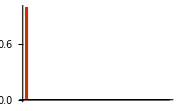
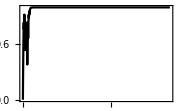
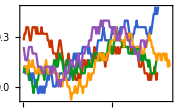

```mathematica
Block[{L=6,ϵ=0.1,Id,S,ρ0,measure,ρs,ϵs},
Id=SparseArray[{Band[{1,1}]->1},{2^L,2^L}];
S=SparseArray@Represent[Table[σ@@SparseArray[{i->a},L],{i,L},{a,3}]];
ρ0=#⊗#/2&@SparseArray[{1->1,-1->1},{2^L}];
measure[ρ1_]:=Block[{i,m,M,ρ2,p,a},
i=RandomInteger[{2,L}];
m={0,0,1};
M=AssociationThread[{1,-1}->{Id+ϵ #,Id-ϵ #}/Sqrt[2(1+ϵ^2)]]&[m.S⟦i⟧];
ρ2=#.ρ1.ConjugateTranspose[#]&/@M;
p=Re[Tr/@ρ2];
a=RandomChoice[p/@{1,-1}->{1,-1}];
Sow[a m,i];
ρ2[a]/p[a]];
{ρs,ϵs}=Reap[NestList[measure,ρ0,1000],Range[2,L]];
{BarChart[Re@Normal@Diagonal[Last@ρs],ImageSize->180],ListLinePlot[Re[Tr[S⟦1,3⟧.#]&/@ρs],PlotStyle->Black,PlotRange->All,ImageSize->180],ListLinePlot[MovingAverage[#,50]&/@ϵs⟦All,1,All,3⟧,PlotRange->All,ImageSize->180]}
]
```

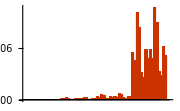
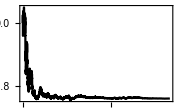
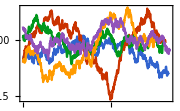

```mathematica
Block[{L=6,ϵ=0.05,Id,S,ρ0,measure,ρs,ϵs},
Id=SparseArray[{Band[{1,1}]->1},{2^L,2^L}];
S=SparseArray@Represent[Table[σ@@SparseArray[{i->a},L],{i,L},{a,3}]];
ρ0=#⊗#/2&@SparseArray[{1->1,-1->1},{2^L}];
measure[ρ1_]:=Block[{i,m,M,ρ2,p,a},
i=RandomInteger[{2,L}];
m=Normalize@RandomVariate[NormalDistribution[],{3}];
M=AssociationThread[{1,-1}->{Id+ϵ #,Id-ϵ #}/Sqrt[2(1+ϵ^2)]]&[m.S⟦i⟧];
ρ2=#.ρ1.ConjugateTranspose[#]&/@M;
p=Re[Tr/@ρ2];
a=RandomChoice[p/@{1,-1}->{1,-1}];
Sow[a m,i];
ρ2[a]/p[a]];
{ρs,ϵs}=Reap[NestList[measure,ρ0,5000],Range[2,L]];
{BarChart[Re@Normal@Diagonal[Last@ρs],ImageSize->180],ListLinePlot[Re[Tr[S⟦1,3⟧.#]&/@ρs],PlotStyle->Black,PlotRange->All,ImageSize->180],ListLinePlot[MovingAverage[#,200]&/@ϵs⟦All,1,All,3⟧,PlotRange->All,ImageSize->180]}
]
```

#### Mutual Information

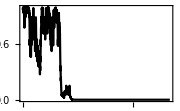
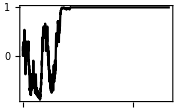
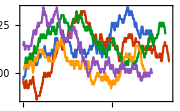
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Block[{L=6,ϵ=0.05,Id,S,ρ0,measure,MI,ρs,ϵs},
Id=SparseArray[{Band[{1,1}]->1},{2^L,2^L}];
S=SparseArray@Represent[Table[σ@@SparseArray[{i->a},L],{i,L},{a,3}]];
ρ0=#⊗#/2&@SparseArray[{1->1,-1->1},{2^L}];
measure[ρ1_]:=Block[{i,m,M,ρ2,p,a},
i=RandomInteger[{2,L}];
m={0,0,1};
(*m=Normalize@RandomVariate[NormalDistribution[],{3}];*)
M=AssociationThread[{1,-1}->{Id+ϵ #,Id-ϵ #}/Sqrt[2(1+ϵ^2)]]&[m.S⟦i⟧];
ρ2=#.ρ1.ConjugateTranspose[#]&/@M;
p=Re[Tr/@ρ2];
a=RandomChoice[p/@{1,-1}->{1,-1}];
Sow[a m,i];
ρ2[a]/p[a]];
MI[ρ_]:=Block[{ρr,Ent},
ρr=TensorContract[ArrayReshape[ρ,ConstantArray[2,2L]],Table[{i,i+L},{i,3,L}]];
Ent[ps_]:=Re@Total[If[#==0.,0.,-# Log[2,#]]&/@ps];
Ent[Eigenvalues@N@TensorContract[ρr,{{2,4}}]]+Ent[Eigenvalues@N@TensorContract[ρr,{{1,3}}]]-Ent[Eigenvalues@N@ArrayReshape[ρr,{4,4}]]];
{ρs,ϵs}=Reap[NestList[measure,ρ0,2000],Range[2,L]];
{BarChart[Re@Normal@Diagonal[Last@ρs],ImageSize->180],ListLinePlot[MI/@ρs,PlotStyle->Black,PlotRange->All,ImageSize->180],ListLinePlot[Re[Tr[S⟦1,3⟧.#]&/@ρs],PlotStyle->Black,PlotRange->All,ImageSize->180],ListLinePlot[MovingAverage[#,100]&/@ϵs⟦All,1,All,3⟧,PlotRange->All,ImageSize->180]}
]
```

We can consider a generative model like RBM

E({v},{h})=∑_(i,j) w_ij v_i h_j+∑_j b_j h_j.

How many mode h do we need? → dimension of Hilbert space of the system.

How confident we can determine {h} based on {v}

p({h}|{v})=(p({v}|{h})p({h}))/(p({v}))

Also this is not calculated simply by clamping a specific {v}, because we could have already collect a bunch of data about {v}. Different configurations of {v} have appeared many times. We want to evaluate this based on the entire data. To this end, we need to first figure out how to evaluate this Bayesian probability give a set of {v} configurations jointly.

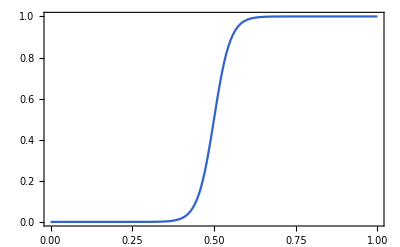

```mathematica
Plot[Block[{q=1-p,n=10},p^n/(p^n+q^n)],{p,0,1}]
```

We first train the machine on long-time data, where the state has already collapsed. This is to teach the machine about how to use the apparatus, how to read out useful information. After that we can apply the same machine to analyze the data starting from the GHZ state. At the beginning the local measurement looks like 1:1 random, because the reduced density matrix is identity, then no knowledge can be learned. As weak measurement goes information about the qubit is gradually obtained, we use the trained machine (generative model) to evaluate the confidence of the internal state {h} to investigate how this confidence raises as the decoherence happens. (Without training, the state still decohere but no knowledge is gained by the machine.)

To work with local measurement, we need a generative model that can marginalize easily.

We can also consider to remove the locality condition, then the observer should be able to develop a full understanding of the entire quantum state (capturing non-local correlations).

#### Joint Distribution

We do not need to sample the weak measurement outcome one-by-one. We can sample a sequence of outcomes all at once from their joint distribution.

We will consider the binary measurement on GHZ state.

K_±=e^(±ϵ Z/2)/(√(2cosh ϵ))=1/(√(2 cosh ϵ))(e^(±ϵ/2) | 0
0 | e^(∓ϵ/2)).

One can verify that ∑_a K_a^†K_a=𝟙.

Suppose we take totally n weak measurements, among which n_± outcomes are ±. This means the overall measurement operator (in the space spanned by the all-up and all-down states) is

K=K_+^(n_+)K_-^(n_-)=1/(2 cosh ϵ)^(n/2)(e^(ϵ/2(n_+-n_-)) | 0
0 | e^(-ϵ/2(n_+-n_-))).

The GHZ state in this subspace is represented as

Ψ=1/(√(2cosh α))(e^(α/2)
e^(-α/2))

We can calculate the probability for this to happen

p(n_+,n_-)=Ψ K^†KΨ
=(cosh(ϵ(n_+-n_-)+α))/(2cosh α (2 cosh ϵ)^n).

Introduce the magnetization -1≤m≤1,

{ | n_++n_-=n
n_+-n_-=m n⇒{ | n_+=(1+m)n/2
n_-=(1-m)n/2

The probability for the weak measurement outcome sequence to have a particular magnetization m is

p(m)=(n
(1+m)n/2)(cosh(ϵ m n+α))/(2cosh α (2 cosh ϵ)^n).

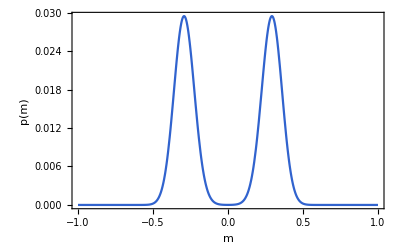

```mathematica
Block[{α=0,ϵ=0.3,n=200},
Plot[{2 Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2]},{m,-1,1},FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->All]]
```

The weak measurement outcome will develop the two-peak structure for large enough total sample number n.

The splitting happens when ∂_m^2 p(m) changes sign, which happens when

∂_m^2 p(m)=n^2/(2(2 cosh ϵ)^n)(n
n/2)(2 ϵ^2-ψ^(1)(1+n/2))=0,

```mathematica
FullSimplify[D[2 Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,2}]/.m->0]
```

1/2 n^2 Binomial[n,n/2] (2 ϵ^2-PolyGamma[1,1+n/2]) (Csch[ϵ] Sinh[2 ϵ])^-n

Details.

where ψ^(1) is the polygamma function. The solution of Eq. (DisplayFormulaNumbered) is given by

ϵ=(1/2 ψ^(1)(1+n/2))^(1/2)→^(n→∞)n^(-1/2).

```mathematica
Series[Sqrt[PolyGamma[1,1+n/2]/2],{n,∞,1}]
```

√(1/n)+O[1/n]^(3/2)

Details.

After the weak measurement, the GHZ state becomes

KΨ=1/(2 cosh ϵ)^(n/2)1/(√(2cosh α))(e^((ϵ m n+α)/2)
e^(-(ϵ m n+α)/2)),

So the quantum coherence is given by

c(m)=1/(cosh(ϵ m n+α)).

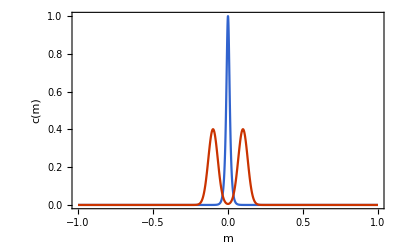

```mathematica
Block[{α=0,ϵ=0.1,n=1000},
Plot[{Sech[ϵ m n+α],Exp[Log[2 Cosh[ϵ m n+α]]-n Log[2 Cosh[ϵ]]-Log[2Cosh[α]]+LogGamma[n+1.]-LogGamma[(1+m)n/2+1.]-LogGamma[(1-m)n/2+1.]+Log[n]/2]},{m,-1,1},FrameLabel->{"\!\(m\)","\!\(c(m)\)"},PlotRange->All]]
```

We also plot p(m) in red to show that most likely the state has already decohere when the two modes split apart. We can try to quantify the confidence of the classification.

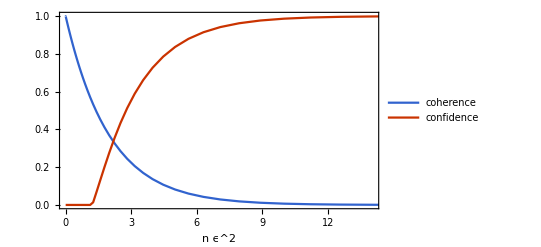

```mathematica
Block[{α=0,ϵ=0.01},ListLinePlot[Thread[Table[Block[{n ,p,c},
n=10^lgn/ϵ^2;
p[m_]:=Exp[Log[2 Cosh[ϵ m n+α]]-n Log[2 Cosh[ϵ]]-Log[2Cosh[α]]+LogGamma[n+1.]-LogGamma[(1+m)n/2+1.]-LogGamma[(1-m)n/2+1.]+Log[n/2]];
c=
NIntegrate[Exp[Log[n]-n Log[2 Cosh[ϵ]]-Log[2Cosh[α]]+LogGamma[n+1.]-LogGamma[(1+m)n/2+1.]-LogGamma[(1-m)n/2+1.]],{m,-1,1}];
{n ϵ^2,#}&/@{c,1-Clip[p[0]/p[ϵ],{0,1}]}],{lgn,-3,1.5,0.05}]],FrameLabel->{"\!\(n ϵ\^2\)"},PlotLegends->{"coherence","confidence"}]]
```

Universal curves emerge in the weak measurement limit as ϵ→0.

```mathematica
Block[{n=200},
Graphics3D[{AbsolutePointSize[3],Point[{#,0.5#,0.2#}&/@(RandomVariate[NormalDistribution[0,0.15],{n}]+0.5RandomChoice[{1,-1},{n}])+RandomVariate[NormalDistribution[0,0.02],{n,3}]],
{Dashed,Red,Line[{1,0.5,0.2}#&/@{-1,1}]}},PlotRange->1]]
```

-Graphics3D-

## Quantum State Tomography

### VAE Model

#### Density Matrix Model

Define the single-qubit POVM

E_m=(σ^0+m·σ)/2.

We have

Tr E_m=1, Tr E_m E_m'=(1+m·m')/2.

Consider the many-body density matrix to be modeled by

ρ=∫⊗_i E_(m_i(z))p(z)ⅆz,
=∫E[m]p[m]ⅅ[m],

where z is the set of latent variables and m_i(z) are functions of z. The prior distribution p(z) is taken to be normalized Gaussian, such that all the non-triviality goes to the mapping m_i(z).

The key difference from Juan’s setup: they tries to build a generative model to directly model the measurement outcome distribution and then recover the density matrix of the outcome distribution. But we do not have an explicit model for measurement outcome (although we can estimate the outcome probability base on our model), we directly model the density matrix.

In this way, we achieve three advantages:

To recover density matrix from outcome distribution, a non-singular overlapping matrix T between the POVM’s is needed. This restricts the choice of POVM. In particular, we can only work with discrete POVM which forbidden us from applying differentiable generative models (flow-based, VAE ...). Our scheme can work with continuous POVMs and enables the application of differentiable generative model.

In principle, Juan’s framework can also be generalized to weak measurement, but as the measurement becomes weaker, the overlapping matrix T becomes more singular, and the algorithm is very unstable. We do not model the outcome distribution but directly model the density matrix, which is more stable in the weak measurement limit.

Boltzmann machine and autoregressive models are hard to marginalize. It turns out that VAE is easy to marginalize, which allows quantum state tomography from local measurements and density matrix reconstruction.

#### Weak Measurement

The weak measurement at site i will obtain outcome x with probability

p_mdl(x)=Tr E_x ρ
=∫(1+x·m_i(z))/2 p(z)ⅆz
=∫p(x|z)p(z)ⅆz,

where p(x|z)=(1+x·m_i(z))/2. So the measurement outcome probability nicely fit in the framework of classical probability theory. As the prior distribution p(z) is always assumed to be normal Gaussian, all the non-triviality enters from the conditional distribution p(x|z) which eventually relies on a non-trivial mapping of m_i(z). We relies on neural network to realize the non-linear map m_i(z) with broad enough representation power.

#### Training Objectives

The original objective is to maximize the likelihood on observed outcomes

max ℒ:ℒ=ln p_mdl(x).

However, evaluating p_mdl(x) involves sampling over z\[Distributed]p(z), which is inefficient. The idea of VAE is to build a variational ansatz q(z|x) to approximate p(z|x), which allows us to do importance sampling of z\[Distributed]q(z|x) by inference. Now the objective becomes two folded:

to maximize likelihood ln p(x),

and to bring q(z|x) close to p(z|x) by minimizing their KL divergence.

So the objective function can be chosen as

ℒ=𝔼_(z\[Distributed]q(z|x))ln p(x)-D_KL(q(z|x)||p(z|x))
=𝔼_(z\[Distributed]q(z|x))(ln p(x)+ln p(z|x)-ln q(z|x))
=𝔼_(z\[Distributed]q(z|x))(ln p(z)+ln p(x|z)-ln q(z|x))
=𝔼_(z\[Distributed]q(z|x))ln p(x|z)-D_KL(q(z|x)||p(z)).

### Density Matrix Modeling

#### Tetra POVM

##### On-Site Case

Consider a the tetra basis of qubit POVM,

E_x=K_x^†K_x=1/4(σ^0+x·σ),

where x=x m labels the POVM and m is a unit vector taken from

m=(1,1,1)/(√3),(1,-1,-1)/(√3),(-1,1,-1)/(√3),(-1,-1,1)/(√3).

It can be verified that

∑_x E_x=σ^0.

The overlap matrix reads

T_(x_1 x_2)=Tr(E_x_1 E_x_2^†)=1/8-(x_1 x_2)/24(1-4 δ_(x_1 x_2)),

```mathematica
Block[{ms,Es,T},
ms=Normalize/@{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}};
Es[x_]:=Represent[(σ[0]+#.(σ/@Range[3]))/4]&/@(x ms);
T=FullSimplify[Table[Tr[E1.ConjugateTranspose[E2]],{E1,Es[x1]},{E2,Es[x2]}],x1>0&&x2>0];
MatrixForm@Expand@T]
```

(1/8+(x1 x2)/8 | 1/8-(x1 x2)/24 | 1/8-(x1 x2)/24 | 1/8-(x1 x2)/24
1/8-(x1 x2)/24 | 1/8+(x1 x2)/8 | 1/8-(x1 x2)/24 | 1/8-(x1 x2)/24
1/8-(x1 x2)/24 | 1/8-(x1 x2)/24 | 1/8+(x1 x2)/8 | 1/8-(x1 x2)/24
1/8-(x1 x2)/24 | 1/8-(x1 x2)/24 | 1/8-(x1 x2)/24 | 1/8+(x1 x2)/8)

Details.

where x_(1,2)=|x_(1,2)| denotes the norm of the vectors. Its inverse gives the metric

(T^-1)_(x_1 x_2)=1/2-3/(2 x_1 x_2)(1-4 δ_(ϵ_1 ϵ_2)).

```mathematica
Block[{ms,Es,T},
ms=Normalize/@{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}};
Es[x_]:=Represent[(σ[0]+#.(σ/@Range[3]))/4]&/@(x ms);
T=FullSimplify[Table[Tr[E1.ConjugateTranspose[E2]],{E1,Es[x1]},{E2,Es[x2]}],x1>0&&x2>0];
MatrixForm@Simplify@Inverse@T]
```

(1/2+9/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2)
1/2-3/(2 x1 x2) | 1/2+9/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2)
1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2+9/(2 x1 x2) | 1/2-3/(2 x1 x2)
1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2-3/(2 x1 x2) | 1/2+9/(2 x1 x2))

Details.

Special case: when x_1=x_2=1,

T_(x_1 x_2)=1/8-(1-4 δ_(x_1 x_2))/24=Piecewise[{{1/4, if x_1=x_2,}, {1/12, if x_1≠x_2.}}]

(T^-1)_(x_1 x_2)=1/2-(3(1-4 δ_(x_1 x_2)))/2=Piecewise[{{5, if x_1=x_2,}, {-1, if x_1≠x_2.}}]

In general T^-1 becomes singular when either x_1 or x_2 approaches zero.

We can use T^-1 to construct a tetra IOVM

(Ẽ)_x=∑_x' (T^-1)_(x x')E_x'
=1/2(σ^0+3/x^2 x·σ),

```mathematica
Block[{ms,Es,T,invT},
ms=Normalize/@{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}};
Es[x_]:=Represent[(σ[0]+#.(σ/@Range[3]))/4]&/@(x ms);
T=FullSimplify[Table[Tr[E1.ConjugateTranspose[E2]],{E1,Es[x]},{E2,Es[xp]}],x>0&&xp>0];
invT=Simplify@Inverse@T;
Simplify[Abstract/@(invT.Es[xp])]]
```

{(x σ[0]+√3 (σ[1]+σ[2]+σ[3]))/(2 x),(x σ[0]+√3 (σ[1]-σ[2]-σ[3]))/(2 x),(x σ[0]-√3 (σ[1]-σ[2]+σ[3]))/(2 x),(x σ[0]-√3 (σ[1]+σ[2]-σ[3]))/(2 x)}

Details.

where x=|x| is the norm of x vector and the result is independent of the norm of the x' vector that has been summed over in Eq. (DisplayFormulaNumbered). In the case that x=m as a unit vector, such that E_m is the standard tetra POVM, the corresponding tetra IOVM reads

(Ẽ)_m=1/2(σ^0+3m·σ),

where m are unit vectors taken from Eq. (DisplayFormulaNumbered).

##### Many-Body Case

We define multi-qubit POVM as a product of single-qubit POVM

E[m]=∏_i E_m_i=∏_i 1/4(σ^0+m_i·σ).

This defines the metric

T[m,m']=Tr (E[m]E[m']^†)=∏_i T_(m_i m'_i),

and its inverse

T^-1[m,m']=∏_i (T^-1)_(m_i m'_i).

Given the probability of measurement outcome

p[m]=Tr E[m]ρ,

the density matrix can be back out from the outcome probability by

ρ=∑_([m][m']) E[m]^†T^-1[m,m']p[m'].

Because

∑_([m'][m'']) Tr (E[m]E[m']^†)T^-1[m',m'']p[m'']
=∑_([m'][m'']) T[m,m']T^-1[m',m'']p[m'']
=p[m].

However, this approach has a few problem

For weak measurement, T^-1 will be come singular, if p[m] is considered to be the weak measurement probability.

m must be discrete, measurement are restricted to be performed along special axis,

It is difficult to marginalize p[m] for local measurement (this is not a problem of the formulation but a problem of the choice of generative model).

#### Dual IOVM

In Eq. (DisplayFormulaNumbered), we can absorb T^-1 (sign structure) to E^† and define the dual IOVM

Ẽ[m]=∑_[m'] E[m']^†T^-1[m',m].

In fact, Ẽ[m] can be defined even if T^-1 does not exist. It is defined through the isometry relation that (the summation of [m] can be generalized to integration for the continuous case)

∑_[m] Ẽ[m]⊗E[m]==.

Then we can show that

ρ=∑_[m] Ẽ[m]Tr(E[m]ρ)=∑_[m] Ẽ[m]p[m],

where p[m] is the measurement outcome probability which is positive definite. For generic measurement M[x],

p[x]=Tr M[x]ρ=∑_[m] Tr (M[x]Ẽ[m])p[m]=∑_[m] p[x|m]p[m],

where the conditional distribution is given by

p[x|m]=Tr (M[x]Ẽ[m]).

Although  p[x|m] is not positive for all possible outcomes x, but as long as the measurement is weak enough, the positivity can be bounded.

```mathematica
Abstract/@tTr[{PauliMatrix/@Range[0,3],ArrayReshape[Inverse@ArrayReshape[Sum[If[a==0,1,1/3]PauliMatrix[a]⊗PauliMatrix[a],{a,0,3}],{4,4}],{2,2,2,2}]},{{2,5},{3,4}}]
```

{σ[0]/2,(3 σ[1])/2,(3 σ[2])/2,(3 σ[3])/2}

#### Spherical POVM

##### Single-Qubit Case

Define the single-qubit POVM (assuming m is unit vector)

E_m=(σ^0+m·σ)/2.

The corresponding dual IOVM is given by

(Ẽ)_m=σ^0+3m·σ.

We have

trace properties

Tr E_m=1, Tr E_m E_m'=(1+m·m')/2,

isometry (assuming ∫_(S^2) ⅆm =1)

∫_(S^2) ⅆm (Ẽ)_m⊗E_m
=1/2∫_(S^2) ⅆm (σ^0+3m·σ)⊗(σ^0+m·σ)
=1/2∫_(S^2) ⅆm (σ^0+3 m_1 σ^1+3 m_2 σ^2+3 m_3 σ^3)⊗(σ^0+m_1 σ^1+m_2 σ^2+m_3 σ^3)
=1/2(σ^00+σ^11+σ^22+σ^33).

```mathematica
Integrate[x^2,{x,y,z}∈Sphere[]]/(4π)
```

1/3

Details.

Therefore

∫_(S^2) ⅆm (Ẽ)_m⊗E_m=(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)=swap

```mathematica
Represent[σ[0,0]+σ[1,1]-σ[2,2]+σ[3,3]]//MatrixForm
```

(2 | 0 | 0 | 2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
2 | 0 | 0 | 2)

Details.

Therefore we can establish a model for the density matrix

ρ=∫_(S^2) ⅆm (Ẽ)_m Tr(E_m ρ)=∫_(S^2) ⅆm (Ẽ)_m p_m,

where p_m=Tr(E_m ρ) is positive definite and can be model by any generative model.

##### Multi-Qubit Case

For multiple sites, we define

the POVM and its dual

E[m]=∏_i E_m_i=∏_i (1+m_i·σ_i)/2,
Ẽ[m]=∏_i (Ẽ)_m_i=∏_i (1+3m·σ).

They satisfies the isometry relation

∫ⅅ[m]Ẽ[m]⊗E[m]=SWAP.

the measurement operator (overs non-local observables)

M[x]=1/2(1+∑_[μ] x_[μ]σ^[μ]).

Eq. (DisplayFormulaNumbered) implies that the density matrix can be modeled by

ρ=∫ⅅ[m]Ẽ[m]p[m],

with p[m]=Tr E[m]ρ positive definite. We introduce latent variable z to model p[m]=∫ⅆz δ[m-m(z)]p(z), such that

ρ=∫ⅆzẼ[m(z)]p(z).

Based on this model, the weak measurement outcome should follow

p(x)=Tr M[x]ρ=∫ⅆz p(x|z)p(z),

where the conditional distribution is given by

p(x|z)=Tr M[x]Ẽ[m(z)]=

## Emergent Classical Reality

### Quantum World

#### Model Setup

Consider a model of quantum circuit coupled to neural network via weak measurement interface. Question: can artificial intelligence extract a strong measurement outcome from the weak measurement signals on the ancilla qubits.

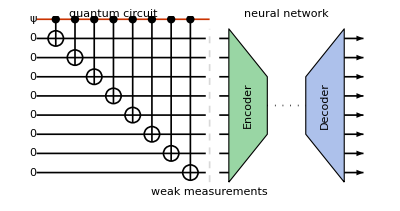

```mathematica
Block[{a=0.4,b=0.3,g=0.2,L=8,t=1},
Graphics[{AbsoluteThickness[1.2],
{Red,Line[{{0,0},{L+1,0}}]},
Table[{
{Line[{{0,y},{L+1-g,y}}]},
{EdgeForm[AbsoluteThickness[1.2]],White,Disk[{L+1+g,y},b,{-π/2,π/2}]},Line[{{L+1+g+b,y},{L+1+t,y}}],Arrow[{{L+1+7t,y},{L+1+8t,y}}]},{y,-L,-1}],
{Dotted,Line[{{L+1+3t,-(L+1)/2},{L+1+5t,-(L+1)/2}}]},Translate[{{Lighter[Green,0.6],EdgeForm[Black],Polygon[{{-t,-L/2},{-t,L/2},{t,1.5},{t,-1.5}}]},{Text["Encoder",{0,0},{0,0},{0,1}]}},{L+1+2t,-(L+1)/2}],
Translate[{{Lighter[Blue,0.6],EdgeForm[Black],Polygon[{{t,-L/2},{t,L/2},{-t,1.5},{-t,-1.5}}]},{Text["Decoder",{0,0},{0,0},{0,1}]}},{L+1+6t,-(L+1)/2}],
AbsolutePointSize[6],Table[{Point[{x,0}],Line[{{x,0},{x,-x-a}}],Circle[{x,-x},a]},{x,1,L}],
Text["\!\(ψ\)",{0,0},{1.2,0}],
Table[Text["\!\(0\)",{0,y},{1.2,0}],{y,-1,-L,-1}],
Text["quantum circuit",{L/2,0},{0,-1}],Text["neural network",{L+1+4t,0},{0,-1}],
{Dashed,LightGray,Line[{{L+1,-L-0.5},{L+1,-0.5}}]},
Text["weak measurements",{L+1,-L-1}]},ImageSize->{Automatic,150}]]
```

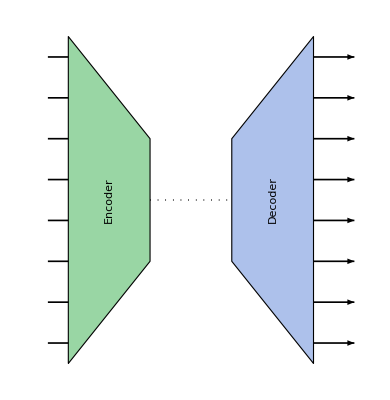

```mathematica
Block[{a=0.4,b=0.3,g=0.2,L=8,t=1},
Graphics[{AbsoluteThickness[1.2],Arrowheads[0.08],
Table[{
{EdgeForm[AbsoluteThickness[1.2]],White,Disk[{L+1+g,y},b,{-π/2,π/2}]},Line[{{L+1+g+b,y},{L+1+t,y}}],Arrow[{{L+1+7t,y},{L+1+8t,y}}]},{y,-L,-1}],
{Dotted,Line[{{L+1+3t,-(L+1)/2},{L+1+5t,-(L+1)/2}}]},Translate[{{Lighter[Green,0.6],EdgeForm[Black],Polygon[{{-t,-L/2},{-t,L/2},{t,1.5},{t,-1.5}}]},{Text["Encoder",{0,0},{0,0},{0,1}]}},{L+1+2t,-(L+1)/2}],
Translate[{{Lighter[Blue,0.6],EdgeForm[Black],Polygon[{{t,-L/2},{t,L/2},{-t,1.5},{-t,-1.5}}]},{Text["Decoder",{0,0},{0,0},{0,1}]}},{L+1+6t,-(L+1)/2}],
},ImageSize->{Automatic,110}]]
```

The quantum circuit models the quantum Darwin process, which entangles the system qubits with the ancilla qubits into a cat state

Ψ=(e^(α/2)000…+e^(-α/2)111…)/(√(2 cosh α)).

Now each ancilla qubit will emit weak measurement signals. There are several possibilities to consider.

Weak measurements in space or in time? We will first consider the measurement in space, such that each measurement operator commute with each other, making the problem simpler. If the measurement happens in time and in random basis, the system may be thermalized quickly.

Measurement basis are random or fixed? It will be better to consider random basis, so as to make the following two points: (i) nature does not have basis preference, but AI can figure out the basis (ii) any local measurement on the ancilla qubit is measuring Z of the system qubit.

Local measurement or non-local? It is physically more reasonable to consider local measurement, because non-local measurement is much harder to occur in nature.

#### Weak Measurement

We consider weak measurement operator of strength ϵ along direction n (unit vector) on site i

K_n_i=e^(ϵ/2 n_i·σ_i)/(√(2 cosh ϵ)).

We assume that the measurement is performed on separate ancilla qubits (because of the permutation symmetry of the problem, it is not necessary to specify the order of the qubits). All measurement operator commute with each other, and the total measurement operator reads

K_[n]=∏_(i=1)^N K_n_i=1/(2 cosh ϵ)^(N/2)e^(ϵ/2∑_(i=1)^N n_i·σ_i).

The probability for the measurement outcome [n] to appear is

p[n]=Ψ K_[n]^†K_[n]Ψ
=1/(2 cosh ϵ)^N Ψ e^(ϵ∑_(i=1)^N n_i·σ_i)Ψ
=1/((2 cosh ϵ)^N(2 cosh α))(e^α 0 e^(ϵ∑_(i=1)^N n_i·σ_i)0+e^-α 1 e^(ϵ∑_(i=1)^N n_i·σ_i)1+0 e^(ϵ∑_(i=1)^N n_i·σ_i)1+1 e^(ϵ∑_(i=1)^N n_i·σ_i)0)
=1/(2^N(2 cosh α))(e^α∏_(i=1)^N (1+n_i^z tanh ϵ)+e^-α∏_(i=1)^N (1-n_i^z tanh ϵ)+2 tanh^N ϵ ∏_(i=1)^N n_i^x).

Simplification is possible in the following limit

For large N, tanh^N ϵ  is exponentially small, and can be dropped.

If the measurement axis is along z, i.e. n_i^z=±1,

p[n]=(cosh(α+ϵ∑_(i=1)^N n_i^z))/((2 cosh ϵ)^N cosh α).

#### Autoregressive Sampling

For general case, we can sample Eq. (DisplayFormulaNumbered) in an autoregressive manner

p[n]=p(n_1)p(n_2|n_1)p(n_3|n_1 n_2)…

The conditional probability can be derived by projecting the measurement operator to the cat state basis. Let us consider weakly measuring a single qubit i on the cat state Ψ

p(n_i|α)=Ψ K_n_i^†K_n_i Ψ
=1/(2 cosh ϵ)Ψ e^(ϵ n_i·σ_i)Ψ
=1/((2 cosh ϵ)(2 cosh α))(e^α 0 e^(ϵ n_i·σ_i)0+e^-α 1 e^(ϵ n_i·σ_i)1+0 e^(ϵ n_i·σ_i)1+1 e^(ϵ n_i·σ_i)0)
=1/(2(2 cosh α))(e^α(1+n_i^z tanh ϵ)+e^-α(1-n_i^z tanh ϵ))
=1/2(1+n_i^z tanh α tanh ϵ).

The cross term vanishes, because the unmeasured qubits are still orthogonal between the two universes. Based on the conditional probability p(n_i|α), we can sample the outcome vector n_i.

With the outcome n_i, the state will be modified by

Ψ→K_n_i Ψ.

The measurement operator represented on the qubit reads

K_n_i=e^(ϵ/2 n_i·σ_i)/(√(2 cosh ϵ))
=(cosh ϵ/2+sinh ϵ/2 n_i·σ_i)/(√(2 cosh ϵ))
≏(cosh ϵ/2)/(√(2 cosh ϵ))(1+n_i^z tanh ϵ/2 | (n_i^z-ⅈ n_i^y)tanh ϵ/2
(n_i^z+ⅈ n_i^y)tanh ϵ/2 | 1-n_i^z tanh ϵ/2).

In the cat state basis, the off-diagonal elements will be projected out

K_n_i≏(cosh ϵ/2)/(√(2 cosh ϵ))(1+n_i^z tanh ϵ/2 | 0
0 | 1-n_i^z tanh ϵ/2).

The state is represented as

Ψ≏1/(√(2 cosh α))(e^(α/2)
e^(-α/2)).

Applying the measurement operator, we have

K_n_i Ψ≏(cosh ϵ/2)/(√(2 cosh ϵ)√(2 cosh α))((1+n_i^z tanh ϵ/2)e^(α/2)
(1-n_i^z tanh ϵ/2)e^(-α/2))

To match the form of the cat sate (ignoring the components outside the code subspace), we should have

(e^(α'/2)
e^(-α'/2))∝((1+n_i^z tanh ϵ/2)e^(α/2)
(1-n_i^z tanh ϵ/2)e^(-α/2)),

which implies

α'=α+ln(1+n_i^z tanh ϵ/2)/(1-n_i^z tanh ϵ/2)=α+2 arctanh(n_i^z tanh ϵ/2).

In conclusion, a sequence of weak measurement outcome can be sampled as follows:

n_i\[Distributed]p(n_i|α)=1/(4π)(1+n_i^z tanh α tanh ϵ),
α→α+2 arctanh(n_i^z tanh ϵ/2).

For n_i^z=±1, Eq. (DisplayFormulaNumbered) reduces to

n_i^z\[Distributed]p(n_i^z|α)=(cosh(α+ϵ n_i^z))/(2 cosh ϵ cosh α)=1/2(1+n_i^z tanh α tanh ϵ),
α→α+ϵ n_i^z.

Apply Eq. (DisplayFormulaNumbered) in a autoregressive manner, we can recover the joint distribution

p[n]=(cosh(α+ϵ n_1^z))/(2 cosh ϵ cosh α)(cosh(α+ϵ n_1^z+ϵ n_2^z))/(2 cosh ϵ cosh(α+ϵ n_1^z))…
=(cosh(α+ϵ ∑_(i=1)^N n_i^z))/((2 cosh ϵ)^N cosh α),

which matches Eq. (DisplayFormulaNumbered) as derived previously.

##### Dipolar Distribution

The distribution function appeared in Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) can be unified as the dipolar distribution (in different dimensions). The d-dimensional dipolar distribution is a distribution of d-component unit vector x=(x_1,x_2,…,x_d) following the PDF

p(x)=1/(Ω_(d-1))(1+x_d m),

where Ω_(d-1)=2π^(d/2)/Γ(d/2) is the volume of a S^(d-1) unit sphere. The parameter m, called polarization, controls the distribution. It takes value in [-1,1].

We can switch to a spherical coordinate

x_d=cos θ,
(x_1,…,x_(d-1))=r sin θ,

where θ∈[0,π] and r is a (d-1)-component unit vector on S^(d-2). This relates ⅆ Ω_(d-1) to sin^(d-2)θⅆθⅆ Ω_(d-2)

p(x)ⅆ Ω_(d-1)=1/(Ω_(d-1))(1+m cos θ)sin^(d-2) θⅆθⅆ Ω_(d-2)
=1/(Ω_(d-1))(1+m cos θ)sin^(d-2) θⅆθⅆ Ω_(d-2)

We can marginalize over the unit vector r on S^(d-2) and obtain the distribution of θ∈[0,π]:

p(θ)ⅆθ=(Ω_(d-2))/(Ω_(d-1))(1+m cos θ)sin^(d-2) θⅆθ
=(Γ(d/2))/(√π Γ((d-1)/2))(1+m cos θ)sin^(d-2) θⅆθ.

```mathematica
Gamma[d/2]/(Sqrt[π]Gamma[(d-1)/2])Integrate[Sin[θ]^(d-2),{θ,0,π},Assumptions->d>1]
```

1

Check normalization.

One can check that the distribution is normalized ∫_0^π p(θ)ⅆθ=1. A special limit is d=1, where the denominator Γ(0) diverges. In this case, the distribution actually reduces to the Bernoulli distribution of discrete variable x=±1. Alternatively, we may switch back to the coordinate z=cos θ (s.t. ⅆz=-sin θⅆθ),

p(z)ⅆz=-p(θ)ⅆθ
=(Γ(d/2))/(√π Γ((d-1)/2))(1+m z)sin^(d-2) θ ⅆz/(sin θ)
=(Γ(d/2))/(√π Γ((d-1)/2))(1+m z)(1-z^2)^((d-3)/2)ⅆz,

```mathematica
Gamma[d/2]/(Sqrt[π]Gamma[(d-1)/2])Integrate[(1-z^2)^((d-3)/2),{z,-1,1},Assumptions->d>1]
```

1

Check normalization.

where z takes value in [-1,+1].

Let us calculate the entropy associated with the dipolar distribution. We can consider the Rényi entropy

S^(n)=1/(1-n)ln∫_0^π (p(θ))^n ⅆθ
=S_0^(n)+1/(1-n)ln∫_0^π (1+m cos θ)^n sin^(n(d-2)) θⅆθ

where zero point entropy S_0^(n) is given by

S_0^(n)=n/(1-n) ln((Γ(d/2))/(√π Γ((d-1)/2))).

Denote q_1=n(d-2),

S^(n)=S_0^(n)+1/(1-n)ln∫_0^π (1+m cos θ)^n sin^q_1 θⅆθ
=S_0^(n)+1/(1-n)ln∑_(k=0)^n (n
k)m^k∫_0^π cos^k θ sin^q_1 θⅆθ
=S_0^(n)+1/(1-n)ln∑_(k=0:2:n) (n
k)m^k(Γ((k+1)/2)Γ((q_1+1)/2))/(Γ((k+q_1+2)/2)).

```mathematica
Integrate[Cos[θ]^k Sin[θ]^q,{θ,0,π}]
```

ConditionalExpression[((1+(-1)^k) Gamma[(1+k)/2] Gamma[(1+q)/2])/(2 Gamma[1/2 (2+k+q)]),Re[k]>-1&&Re[q]>-1]

Integral.

If we use the z=cos θ coordinate

S^(n)=1/(1-n)ln∫_-1^1 (p(z))^n ⅆz
=S_0^(n)+1/(1-n)ln∫_-1^1 (1+m z)^n(1-z^2)^(n(d-3)/2)ⅆz.

Denote q_2=n(d-3)+1,

S^(n)=S_0^(n)+1/(1-n)ln∫_-1^1 (1+m z)^n(1-z^2)^((q_2-1)/2)ⅆz
=S_0^(n)+1/(1-n)ln∑_(k=0)^n (n
k)m^k∫_-1^1 z^k (1-z^2)^((q_2-1)/2)ⅆz
=S_0^(n)+1/(1-n)ln∑_(k=0:2:n) (n
k)m^k(Γ((k+1)/2)Γ((q_2+1)/2))/(Γ((k+q_2+2)/2)).

```mathematica
Integrate[z^k(1-z^2)^((q-1)/2),{z,-1,1}]
```

ConditionalExpression[((1+(-1)^k) Gamma[(1+k)/2] Gamma[(1+q)/2])/(2 Gamma[1/2 (2+k+q)]),Re[k]>-1&&Re[q]>-1]

Integral.

We can see that Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) has the similar form but only differ in q_1=n(d-2) and q_2=n(d-3)+1. In the limit of n→1, q_1 and q_2 are the same. We will leave this difference for later treatment, and proceed with the summation by denoting q_(1,2) as q generally

S^(n)=S_0^(n)+1/(1-n)ln∑_(k=0:2:n) (n
k)m^k(Γ((k+1)/2)Γ((q+1)/2))/(Γ((k+q+2)/2))
=S_0^(n)+1/(1-n)ln(√π Γ((q+1)/2))/(Γ((q+2)/2))_2 F_1((1-n)/2,-n/2;1+q/2;m^2),

```mathematica
Sum[Binomial[n,k]m^k Gamma[(k+1)/2]Gamma[(q+1)/2]/Gamma[(k+q+2)/2],{k,0,n,2}]
```

(√π Gamma[(1+q)/2] Hypergeometric2F1[1/2-n/2,-n/2,1+q/2,m^2])/Gamma[(2+q)/2]

Summation.

where _2 F_1(a,b;c;z) is the hypergeometric function. To absorber the prefactor, we can define

S_bg^(n)=S_0^(n)+1/(1-n)ln(√π Γ((q+1)/2))/(Γ((q+2)/2))
=ln √π+1/(1-n) ln(((Γ(d/2))^n Γ((q+1)/2))/((Γ((d-1)/2))^n Γ((q+2)/2))),

Then the Rényi entropy reads

S^(n)=S_bg^(n)+1/(1-n)ln_2 F_1((1-n)/2,-n/2;1+q/2;m^2).

Now we take the limit of n→1 to extract the Shannon entropy

S=lim_(n→1) S^(n)=S_bg+1/2_2 F_1^(0,1,0,0)(-1/2,0;d/2;m^2),

```mathematica
Block[{S1,S2},
S1[n_,d_,m_]:=Block[{q=n(d-2)},Log[Sqrt[π]]+Log[(Gamma[d/2]^n Gamma[(q+1)/2])/(Gamma[(d-1)/2]^n Gamma[(q+2)/2])]/(1-n)+Log[Hypergeometric2F1[(1-n)/2,-n/2,1+q/2,m^2]]/(1-n)];
S2[n_,d_,m_]:=Block[{q=n(d-3)+1},Log[Sqrt[π]]+Log[(Gamma[d/2]^n Gamma[(q+1)/2])/(Gamma[(d-1)/2]^n Gamma[(q+2)/2])]/(1-n)+Log[Hypergeometric2F1[(1-n)/2,-n/2,1+q/2,m^2]]/(1-n)];
Limit[{S1[n,d,m],S2[n,d,m]},n->1]//FullSimplify
]
```

{1/2 (Log[π]+2 Log[Gamma[1/2 (-1+d)]]-2 Log[Gamma[d/2]]-(-2+d) PolyGamma[0,1/2 (-1+d)]+(-2+d) PolyGamma[0,d/2]-(-2+d) Hypergeometric2F1^(0,0,1,0)[-1/2,0,d/2,m^2]+Hypergeometric2F1^(0,1,0,0)[-1/2,0,d/2,m^2]+Hypergeometric2F1^(1,0,0,0)[-1/2,0,d/2,m^2]),1/2 (Log[π]+2 Log[Gamma[1/2 (-1+d)]]-2 Log[Gamma[d/2]]-(-3+d) PolyGamma[0,1/2 (-1+d)]+(-3+d) PolyGamma[0,d/2]-(-3+d) Hypergeometric2F1^(0,0,1,0)[-1/2,0,d/2,m^2]+Hypergeometric2F1^(0,1,0,0)[-1/2,0,d/2,m^2]+Hypergeometric2F1^(1,0,0,0)[-1/2,0,d/2,m^2])}

Expansion.

where the background entropy (independent of m) depends on the choice of q

q=q_1:S_bg=ln (√π Γ((d-1)/2))/(Γ(d/2))+(d-2)/2(ψ(d/2)-ψ((d-1)/2)),
q=q_2:S_bg=ln (√π Γ((d-1)/2))/(Γ(d/2))+(d-3)/2(ψ(d/2)-ψ((d-1)/2)),

where ψ is the digamma function. We can numerically verify that Eq. (DisplayFormulaNumbered) is indeed the correct limit of Eq. (DisplayFormulaNumbered).

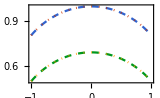

```mathematica
Block[{S1,S2},
S1[n_,d_,m_]:=Block[{q=n(d-2)},Log[Sqrt[π]]+Log[(Gamma[d/2]^n Gamma[(q+1)/2])/(Gamma[(d-1)/2]^n Gamma[(q+2)/2])]/(1-n)+Log[Hypergeometric2F1[(1-n)/2,-n/2,1+q/2,m^2]]/(1-n)];
S2[n_,d_,m_]:=Block[{q=n(d-3)+1},Log[Sqrt[π]]+Log[(Gamma[d/2]^n Gamma[(q+1)/2])/(Gamma[(d-1)/2]^n Gamma[(q+2)/2])]/(1-n)+Log[Hypergeometric2F1[(1-n)/2,-n/2,1+q/2,m^2]]/(1-n)];
S1[d_,m_]:=Log[(Sqrt[π]Gamma[(d-1)/2])/Gamma[d/2]]+(d-2)/2(PolyGamma[d/2]-PolyGamma[(d-1)/2])+1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,d/2,m^2];
S2[d_,m_]:=Log[(Sqrt[π]Gamma[(d-1)/2])/Gamma[d/2]]+(d-3)/2(PolyGamma[d/2]-PolyGamma[(d-1)/2])+1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,d/2,m^2];
Plot[{S1[1.001,3,m],S1[3,m],S2[1.001,3,m],S2[3,m]},{m,-1,1},PlotStyle->{Dashed,Dotted,Dashed,Dotted},FrameLabel->{"\!\(m\)","\!\(S(m)\)"},ImageSize->160]
]
```

The two different choices of q only leads to a constant shift of the entropy. To determine the background entropy, we take the d→1 limit, where we know that the entropy should converge to that of the Bernoulli distribution

S=-(1+m)/2ln(1+m)/2-(1-m)/2 ln(1-m)/2
=ln 2+1/2_2 F_1^(0,1,0,0)(-1/2,0;1/2;m^2),

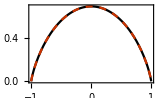

```mathematica
Plot[{Log[2]
+1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,1/2,m^2],
-(1+m)/2Log[(1+m)/2]-(1-m)/2Log[(1-m)/2]},{m,-1,1},PlotStyle->{Black,Dashed},FrameLabel->{"\!\(m\)","\!\(S(m)\)"},ImageSize->160]
```

So we identify that S_bg=ln 2 for d=1. To generalize to higher dimension, we notice that 2 is the volume of S^0, i.e. 2=Ω_0. So the systematic generalization should be replacing 2 by Ω_(d-1), such that S_bg=ln Ω_(d-1). This is a reasonable assignment, because when m=0 (polarization vanishes), the dipolar distribution reduces to the uniform distribution on S^(d-1), which should have the entropy S=ln Ω_(d-1). Therefore we conclude that the entropy of the d-dimensional dipolar distribution is given by

S=ln Ω_(d-1)+1/2_2 F_1^(0,1,0,0)(-1/2,0;d/2;m^2)
=ln (2 π^(d/2))/(Γ(d/2))+1/2_2 F_1^(0,1,0,0)(-1/2,0;d/2;m^2).

When m=0, the hypergeometric function vanishes, the entropy ln Ω_(d-1) matches what is expected from the uniform distribution on S^(d-1).

d=1 case. As has appeared in Eq. (DisplayFormulaNumbered), the entropy reduces to that of the Bernoulli distribution

S(m)=-(1+m)/2ln(1+m)/2-(1-m)/2 ln(1-m)/2.

d=3 case. The hypergeometric function can be approached by the Taylor series around m=0,

S(m)=ln(4π)+1/2_2 F_1^(0,1,0,0)(-1/2,0;3/2;m^2)
=ln(4π)-m^2/6-m^4/60-m^6/210-m^8/504-𝒪(m^10).

```mathematica
Series[1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,3/2,m^2],{m,0,8}]//N//Rationalize
```

-m^2/6-m^4/60-m^6/210-m^8/504+O[m]^9

Series expansion.

Some more inspection reveals that the terms in follows the rule of

S(m)=ln(4π)-∑_(k=0)^∞ m^(2k+2)/((2k+1)(2k+2)(2k+3)),

which simplifies to

S(m)=ln(4π)+1/2-(1+m)^2/(4m)ln(1+m)+(1-m)^2/(4m)ln(1-m).

```mathematica
Series[Log[4π]+1/2-(1+m)^2/(4m)Log[1+m]+(1-m)^2/(4m)Log[1-m],{m,0,8}]
```

Log[4 π]-m^2/6-m^4/60-m^6/210-m^8/504+O[m]^9

Verification.

We can numerically check that Eq. (DisplayFormulaNumbered) is indeed equivalent to Eq. (DisplayFormulaNumbered).

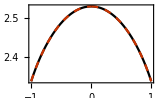

```mathematica
Plot[{Log[4π]+1/2Derivative[0,1,0,0][Hypergeometric2F1][-1/2,0,3/2,m^2],Log[4π]+1/2-(1+m)^2/(4m)Log[1+m]+(1-m)^2/(4m)Log[1-m]},{m,-1,1},PlotStyle->{Black,Dashed},FrameLabel->{"\!\(m\)","\!\(S(m)\)"},ImageSize->160]
```

#### Outcome Distribution

##### Sampling Unit Vector

Let m(α)=tanh α tanh ϵ, we basically need to sample n from

p(n|α)=1/(4π)(1+n^z m).

```mathematica
Block[{θ=π/6,dθ=π/24},Graphics[{Circle[],AbsoluteThickness[1.2],Line[ReIm/@{0,Exp[ⅈ(π/2-#)]}]&/@{0,θ,θ+dθ},
Line[{ReIm@#,{0,Im@#}}]&/@Exp[ⅈ (π/2-{θ,θ+dθ})],
Circle[{0,0},0.2,(π/2-{0,θ})],Text["θ",{0.1,0.3}],Circle[{0,0},0.4,(π/2-{θ,θ+dθ})],Text["ⅆθ",{0.4,0.3}],Text["\!\(ⅆn\^z\)",{0,Cos[θ]},{1,0.5}]},ImageSize->120]]
```

-Graphics-

We first calculate the marginal distribution of n^z

p(n^z|α)ⅆ n^z=p(n|α)(2π sin θⅆθ),

where 2π sin θ ⅆθ is the area of a belt of width ⅆθ surrounding the sphere on the latitude θ. On the other hand, ⅆ n^z=sin θ ⅆθ, so

p(n^z|α)=2π p(n|α)=1/2(1+n^z m).

The distribution is properly normalized as

∫_-1^1 ⅆ n^zp(n^z|α)=∫_-1^1 ⅆ n^z 1/2(1+n^z m)=1.

So we should first sample n^z from p(n^z|α) given in Eq. (DisplayFormulaNumbered), and then prepend the (n^x,n^y) components. To sample n^z, we first calculate the cumulative distribution function,

f(n^z|α)=∫_-1^(n^z) ⅆ n^zp(n^z|α)=1/4(n^z+1)((n^z-1)m+2).

```mathematica
Integrate[(1+m z)/2,{z,-1,n}]//FullSimplify
```

1/4 (2+m (-1+n)) (1+n)

Integration.

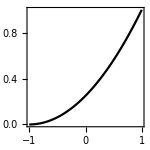

```mathematica
Block[{m=1},
Plot[(n+1)((n-1)m+2)/4,{n,-1,1},FrameLabel->{"\!\(n\^z\)","\!\(f(n\^z|α)\)"},PlotStyle->Black,AspectRatio->1,ImageSize->150]]
```

Then we can take a flow based approach by sampling z∈[0,1] uniformly, and then push it back to n^z by solving the equation of f(n^z|α)=z. The solution is

n^z=(m-2+4z)/(1+√((m-1)^2+4m z)), z\[Distributed]uniform([0,1]).

```mathematica
Solve[(2+m(n-1))(n+1)/4==z,n]
```

{{n→(-1-√(1-2 m+m^2+4 m z))/m},{n→(-1+√(1-2 m+m^2+4 m z))/m}}

Solution.

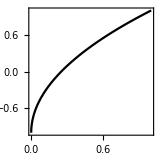

```mathematica
Block[{m=1},
Plot[(m-2+4 z)/(1+Sqrt[(m-1)^2+4m z]),{z,0,1},FrameLabel->{"\!\(z\)","\!\(n\^z\)"},PlotStyle->Black,AspectRatio->1,ImageSize->160]]
```

##### Simulate Weak Measurements

We can use WeakMeasurements[ϵ,N,α0:0] to simulate weak measurements of strength ϵ on N qubits initiated at state of parameter α_0. The result is an association, containing data of α at each step and n as outcomes at each step.

```mathematica
WeakMeasurements[0.1,10,0]
```

<|αs→{0,0.0571878,0.00450611,0.0122992,-0.0222925,0.072805,0.0431786,0.107719,0.123431,0.038227,0.053975},outs→{{0.807263,0.144621,0.572199},{-0.802947,-0.278219,-0.527134},{-0.769664,0.633667,0.0779951},{-0.451155,-0.822572,-0.346171},{0.0387029,-0.3066,0.951051},{-0.087418,-0.951027,-0.29649},{0.696337,-0.313306,0.64572},{0.0743123,0.98476,0.157243},{-0.333791,-0.402845,-0.852232},{-0.532239,0.831794,0.157608}}|>

Distribution of the weak measurement outcomes on a sphere:

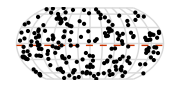
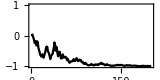

```mathematica
Block[{wm},
wm=WeakMeasurements[0.2,200,0];
Row@{Graphics[{
{LightGray,AbsoluteThickness[1],Line@Table[EEP[{λ,ϕ}],{λ,-π,π,π/6},{ϕ,-π/2,π/2,π/24}],
Line@Table[EEP[{λ,ϕ}],{ϕ,-π/2,π/2,π/6},{λ,{-π,π}}]},
{Dashed,Red,Line[Table[EEP[{λ,#}],{λ,{-π,π}}]]&@ArcSin[Mean[Last/@wm["outs"]]]},
{AbsolutePointSize[3],
Point[EEP[{ArcTan[#1,#2],ArcSin[#3]}]&@@@wm["outs"]]}},ImageSize->180],
ListLinePlot[Tanh[wm["αs"]],PlotStyle->Black,PlotRange->{-1,1},PlotRangePadding->0.1,FrameLabel->{"step","tanh α"},AspectRatio->0.5,ImageSize->160]}]
```

The statistical property is very vague. It is challenging for human to decide which state it collapsed to.

For fixed axis case, it is faster to decohere but the statistical property is still not obvious.

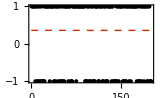
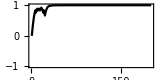

```mathematica
Block[{wm},
wm=WeakMeasurements[0.2,200,0,Axis->"Fixed"];
Row@{ListPlot[wm["outs"],Epilog->{Red,Dashed,Line[Table[{x,#},{x,{0,Length@wm["outs"]}}]]&@Mean[wm["outs"]]},PlotStyle->Directive[Black,AbsolutePointSize[3]],FrameLabel->{"step","\!\(n\^z\)"},ImageSize->160],
ListLinePlot[Tanh[wm["αs"]],PlotStyle->Black,PlotRange->{-1,1},PlotRangePadding->0.1,FrameLabel->{"step","tanh α"},AspectRatio->0.5,ImageSize->160]}]
```

A batch of fixed axis samples. The key feature is the non-local correlation within the same sample.

```mathematica
Grid@Table[Block[{α=0,n=100},
{Style[StringTemplate["\!\(ϵ=`1`\): "][ϵ],14,FontFamily->"CMU"],MatrixPlot[Table[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"],50],ColorFunction->GrayLevel,PlotRangePadding->None,Frame->False,ImageSize->100]}],{ϵ,{0.1,0.2,0.5,1,2}}]
```

ϵ=0.1:  | -Graphics-
ϵ=0.2:  | -Graphics-
ϵ=0.5:  | -Graphics-
ϵ=1:  | -Graphics-
ϵ=2:  | -Graphics-

Note: although the measurement outcomes are collected in a sequential order in the simulation, but they are actually permutation symmetric. Any reshuffling of the data still appears with the same probability.

### Classical World

#### Statistics Analysis

Let us take the case of fixed axis weak measurements. According to Eq. (DisplayFormulaNumbered), the joint distribution is given by

p[n]=(cosh(α+ϵ ∑_(i=1)^N n_i^z))/((2 cosh ϵ)^N cosh α).

Let m=N^-1∑_(i=1)^N n_i^z the magnetization. The distribution of m follows

p(m)=(N
(1+m)/2 N)(cosh(α+ϵ N m))/((2 cosh ϵ)^N cosh α).

As the number N of qubits increases, the distribution of m undergoes a quantum-classical transition at N ϵ^2=1.

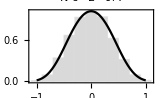

```mathematica
Block[{α=0,ϵ=0.2,n=10},
Show[{Histogram[Table[Mean@N[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"]],10000],{-1-1/n,1+1/n,2/n},"PDF",ChartStyle->LightGray],
Plot[n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1},PlotStyle->Black]},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][n ϵ^2],FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->{0,All},PlotRangePadding->0.1,ImageSize->160]]
```

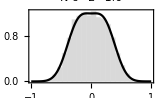

```mathematica
Block[{α=0,ϵ=0.2,n=25},
Show[{Histogram[Table[Mean@N[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"]],10000],{-1-1/n,1+1/n,2/n},"PDF",ChartStyle->LightGray],
Plot[n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1},PlotStyle->Black]},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][n ϵ^2],FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->{0,All},PlotRangePadding->0.1,ImageSize->160]]
```

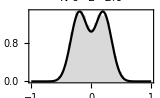

```mathematica
Block[{α=0,ϵ=0.2,n=50},
Show[{Histogram[Table[Mean@N[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"]],10000],{-1-1/n,1+1/n,2/n},"PDF",ChartStyle->LightGray],
Plot[n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1},PlotStyle->Black]},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][n ϵ^2],FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->{0,All},PlotRangePadding->0.1,ImageSize->160]]
```

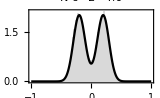

```mathematica
Block[{α=0,ϵ=0.2,n=100},
Show[{Histogram[Table[Mean@N[WeakMeasurements[ϵ,n,α,Axis->"Fixed"]["outs"]],10000],{-1-1/n,1+1/n,2/n},"PDF",ChartStyle->LightGray],
Plot[n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1},PlotStyle->Black]},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][n ϵ^2],FrameLabel->{"\!\(m\)","\!\(p(m)\)"},PlotRange->{0,All},PlotRangePadding->0.1,ImageSize->160]]
```

Define the variance of the distribution p(m) as

⟨m^2⟩=∫m^2 p(m)ⅆm.

It is found that N⟨m^2⟩ grows linearly with N ϵ^2 starting from 1 as

N⟨m^2⟩=1+N ϵ^2.

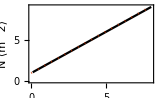

```mathematica
ListLinePlot[{Table[Block[{α=0,ϵ=0.1,n},n=Max[x/ϵ^2,5];{n ϵ^2,n NIntegrate[m^2 n Cosh[ϵ m n+α]/((2 Cosh[ϵ])^n 2 Cosh[α])Binomial[n,(1+m)n/2],{m,-1,1}]}],{x,0.1,8,0.1}],Table[{x,1+x},{x,0,8}]},PlotRange->{0,All},PlotStyle->{Black,Dotted},FrameLabel->{"\!\(N ϵ\^2\)","\!\(N ⟨m\^2⟩\)"},ImageSize->160]
```

This implies that the variance can be describe by

⟨m^2⟩=ϵ^2+1/N.

In the large N limit, it saturates to the constant ϵ^2.

#### Transition

Let us first consider the case of α=0. p(m) can be approximated by the action model

p(m)∝e^(-N E(m)),
E(m)=-1/Nln cosh(N ϵ m)-H(m),
H(m)=-(1+m)/2ln(1+m)/2-(1-m)/2 ln(1-m)/2.

Expand around m→0,

E(m)=1/2(1-N ϵ^2)m^2+1/12(1+N^3 ϵ^4)m^4

```mathematica
Series[-Log[Cosh[ϵ m Ν]]/Ν+Log[2]-(-(1+m)/2Log[(1+m)/2]-(1-m)/2Log[(1-m)/2]),{m,0,4}]
```

(1/2-(ϵ^2 Ν)/2) m^2+1/12 (1+ϵ^4 Ν^3) m^4+O[m]^5

Expansion.

This is similar to a Landau potential. A symmetry breaking transition happens at N ϵ^2=1. The saddle point solution is given by

m=Piecewise[{{0, N<ϵ^-2}, {±√((3(N ϵ^2-1))/(N^3 ϵ^4+1)), N>ϵ^-2}}].

```mathematica
Solve[D[(1-Ν ϵ^2)m^2/2+(1+Ν^3 ϵ^4)m^4/12,m]==0,m]
```

{{m→0},{m→-(√3 √(-1+ϵ^2 Ν))/(√(1+ϵ^4 Ν^3))},{m→(√3 √(-1+ϵ^2 Ν))/(√(1+ϵ^4 Ν^3))}}

Solution.

However, this result only holds around the transition, because the expansion Eq. (DisplayFormulaNumbered) is only valid when m is small. Away from the transition, we should find the saddle point directly from Eq. (DisplayFormulaNumbered),

∂_m E(m)=-ϵ tanh(N ϵ m)+arctanh(m),

```mathematica
Block[{H,Ε},
H[m_]:=-Sum[(1+s m)/2Log[(1+s m)/2],{s,{-1,1}}];
Ε[m_]:=-Log[Cosh[ϵ m Ν]]/Ν+Log[2]-H[m];
D[Ε[m],m]//FullSimplify
]
```

ArcTanh[m]-ϵ Tanh[m ϵ Ν]

Derivative.

the saddle point equation ∂_m E(m)=0 suggests

m=tanh(ϵ tanh(N ϵ m)),

which provides us an iterative approach to solve for m.

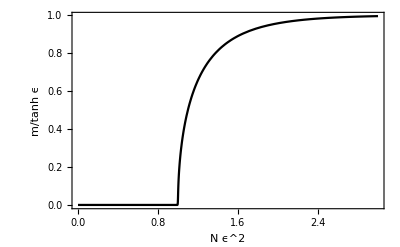

```mathematica
Block[{ϵ=0.1,m},
m[Ν_]:=FixedPoint[Tanh[ϵ Tanh[Ν ϵ #]]&,ϵ,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
Plot[m[x/ϵ^2]/Tanh[ϵ],{x,0,3},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(m/tanh ϵ\)"}]]
```

In the large N limit (N≫ϵ^-2), m converges to tanh ϵ.

We can follow the saddle point solution and expand E(m) around the saddle point to the quadratic order to obtain a Gaussian model. To calculate the quadratic coefficient, we first evaluate the 2nd order derivative of E(m),

1/(χ(m))≡∂_m^2 E(m)=1/(1-m^2)-N ϵ^2(sech(N ϵ m))^2.

```mathematica
Block[{H,Ε},
H[m_]:=-Sum[(1+s m)/2Log[(1+s m)/2],{s,{-1,1}}];
Ε[m_]:=-Log[Cosh[ϵ m Ν]]/Ν+Log[2]-H[m];
D[Ε[m],{m,2}]//FullSimplify
]
```

1/(1-m^2)-ϵ^2 Ν Sech[m ϵ Ν]^2

Derivative.

Given the saddle point solution m̄(N), the energy expands around it as

E(m)=(m-m̄(N))^2/(2 χ(m̄(N))),

which gives a Gaussian distribution of m

p(m)∝e^(-N E(m))=exp(-(N (m-m̄(N))^2)/(2 χ(m̄(N)))),

so the variance of m goes as

var m=⟨m^2⟩-⟨m⟩^2=1/N χ(m̄(N)).

χ(m̄(N)) is the universal (dimensionless) piece of the variance which does not scale with N. It diverges at the transition point as

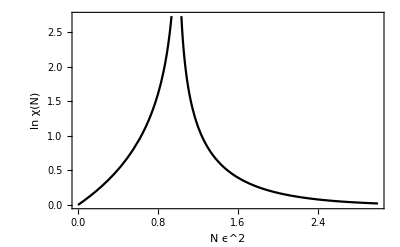

```mathematica
Block[{ϵ=0.1,m,χ},
m[Ν_]:=FixedPoint[Tanh[ϵ Tanh[Ν ϵ #]]&,ϵ,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
χ[Ν_]:=1/(1/(1-#^2)-ϵ^2 Ν Sech[# ϵ Ν]^2&@m[Ν]);
Plot[Log[χ[x/ϵ^2]],{x,0,3},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(ln χ(N)\)"}]]
```

Conclusion: Because of the phase transition in N, we should not expect the neural network to be able to generalize from small N to large N. We should train the neural network separately at different N.

#### Mode Analysis

In the N>ϵ^-2 phase, the distribution p(m) can be modeled by two Gaussian modes

p(m)=∑_(σ=±) p(m|σ)p(σ)
p(m|σ)=1/(√(2π χ/N))exp(-(N (m-σ m̄)^2)/(2 χ)).

Here we consider that p(±)=1/2, both modes are equal likely to appear. How to quantify the confidence of classification?

##### Misclassification Probability

Let us sample m from p(m|+), what is the probability for m to be classified as -?

p(-|m)=(p(m|-)p(-))/(p(m))=(p(m|-)p(-))/(p(m|+)p(+)+p(m|-)p(-)).

Given p(+)=p(-)=1/2, we have

p(-|m)=(p(m|-))/(p(m|+)+p(m|-)).

Now as we sample from p(m|+), the probability of misclassification is

p_mis=∫ⅆm p(-|m)p(m|+)=∫ⅆm(p(m|-)p(m|+))/(p(m|+)+p(m|-)).

Using the Gaussian model in Eq. (DisplayFormulaNumbered),

p_mis=1/(√(2π χ/N))∫ⅆm/(exp((N (m-m̄)^2)/(2 χ))+exp((N (m+ m̄)^2)/(2 χ)))
=1/(√(2π))∫ⅆx/(e^(1/2 (m-a)^2)+e^(1/2 (m+a)^2)).

where a=m̄/σ_m and σ_m=(χ/N)^(1/2) is the standard deviation.

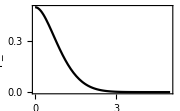

```mathematica
Block[{pmis},
pmis[a_]:=NIntegrate[1/(Exp[(x-a)^2/2]+Exp[(x+a)^2/2]),{x,-∞,∞}]/Sqrt[2π];
Plot[pmis[a],{a,0,5},FrameLabel->{"\!\(m\&_/σ\_m\)","\!\(p\_mis\)"},PlotStyle->Black,ImageSize->180]]
```

Put into the context of transition driven by N, the misclassification drops in the symmetry broken phase.

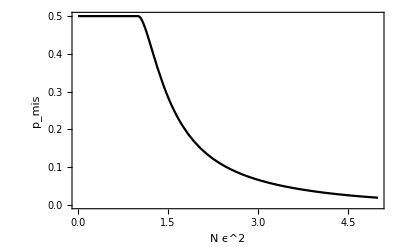

```mathematica
Block[{ϵ=0.1,pmis},
pmis[Ν_]:=Block[{m,χ,a},
m=FixedPoint[Tanh[ϵ Tanh[Ν ϵ #]]&,ϵ,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
χ=1/(1/(1-m^2)-ϵ^2 Ν Sech[m ϵ Ν]^2);
a=m/Sqrt[χ/Ν];
NIntegrate[1/(Exp[(x-a)^2/2]+Exp[(x+a)^2/2]),{x,-∞,∞}]/Sqrt[2π]];
Plot[pmis[x/ϵ^2],{x,0,5},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(p\_mis\)"}]]
```

##### KL Divergence

A probably more natural way is to average the negative log likely hood of p(-|m) when sampling on p(m|+), this quantifies the amount of surprise that one has to pay to misclassify

NLL=-∫ⅆm p(m|+) ln p(-|m)
=-∫ⅆm p(m|+) ln (p(m|-))/(p(m|+)+p(m|-)).

In the case that p(m|+) and p(m|-) is separated, it is likely that p(m|+)≫p(m|-) for those m sampled from p(m|+), so we can replace p(m|+)+p(m|-) by p(m|+), then Eq. (DisplayFormulaNumbered) becomes the KL divergence

NLL≃∫ⅆm p(m|+) ln (p(m|+))/(p(m|-))=KL(p(m|+)|p(m|-)).

For two Gaussians of equal variance (which is the case for p(m|±)), the KL divergence is simply given by

KL(p(m|+)|p(m|-))=(N ((m̄)_+-(m̄)_-)^2)/(2 χ)=(2N(m̄)^2)/χ.

We can define the confidence by

conf=1-e^(-KL(p(m|+)|p(m|-))).

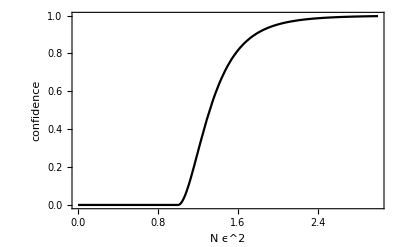

```mathematica
Block[{ϵ=0.1,conf},
conf[Ν_]:=Block[{m,χ},
m=FixedPoint[Tanh[ϵ Tanh[Ν ϵ #]]&,ϵ,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
χ=1/(1/(1-m^2)-ϵ^2 Ν Sech[m ϵ Ν]^2);
1-Exp[-2Ν m^2/χ]];
Plot[conf[x/ϵ^2],{x,0,3},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(confidence\)"}]]
```

### Latent Space

#### Network Design

Encoder q(z|x): Gaussian, parameterized by mean μ_z and standard deviation σ_z.

q(z|x)∝e^(-(z-μ_z[x])^2/(2σ_z^2[x])).

Decoder p(x|z): dipolar distribution.

p(x|z)∝∏_i (1+x_i m(z)).

Loss (to be minimized)

ℒ=ℒ_re+λ ℒ_kl,
ℒ_re=-𝔼_(z\[Distributed]q(z|x))log p(x|z),
ℒ_kl=KL[q(z|x)|p(z)]=1/2(μ_z^2+σ_z^2-1)-log σ_z,

where the prior p(z) is standard normal.

See Jupyter notebook for details.

#### Saddle Point

Consider a toy model (corresponding to a=c=0) of the VAE, by specifying the following mapping

m(z)=b z, μ_z[x]=d x̄, σ_z[x]=e,

Based on Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), we can model the encoder q(z|x) and decoder p(x|z), from which we can further compute the loss function

Reconstruction loss

ℒ_re=-𝔼_(z\[Distributed]q(z|x))log p(x|z)
=-N x̄ b μ_z+1/2 N b^2(μ_z^2+σ_z^2)
=-N b d(x̄)^2+1/2 N b^2(d^2(x̄)^2+e^2)

KL loss

ℒ_kl=KL[q(z|x)|p(z)]
=1/2(μ_z^2+σ_z^2-1)-log σ_z
=1/2 λ(d^2(x̄)^2+e^2-1)-λ log e.

Assemble the total loss with a KL regularization strength λ

ℒ=ℒ_re+λ ℒ_kl
=-N b d(x̄)^2+1/2(N b^2+λ)(d^2(x̄)^2+e^2)-λ log e.

Ensemble average over p(x̄), according to Eq. (DisplayFormulaNumbered),

⟨(x̄)^2⟩=∫ⅆ x̄ (x̄)^2 p(x̄)=ϵ^2+1/N.

Substitute Eq. (DisplayFormulaNumbered) to Eq. Eq. (DisplayFormulaNumbered),

ℒ=-(N ϵ^2+1)b d+1/(2N)(N b^2+λ)(d^2(N ϵ^2+1)+N e^2)-λ log e.

The learning dynamics described by

∂_t b=-N e^2 b-(N ϵ^2+1)d(d b-1),
∂_t d=-1/N(N ϵ^2+1)(λ d+N b (d b-1)),
∂_t e=λ/e-e(N b^2+λ).

```mathematica
FullSimplify[-D[-(Ν ϵ^2+1)b d+1/(2Ν)(Ν b^2+λ)(d^2(Ν ϵ^2+1)+Ν e^2)-λ Log[e],#]]&/@{b,d,e}
```

{d-b e^2 Ν+d ϵ^2 Ν-d^2 (b+b ϵ^2 Ν),-((d λ+b (-1+b d) Ν) (1+ϵ^2 Ν))/Ν,λ/e-e (λ+b^2 Ν)}

Gradient.

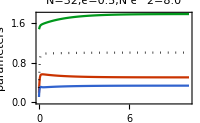

```mathematica
Block[{Ν=32,ϵ=0.5,λ=1,t1=10,b,d,e},
{b,d,e}=NDSolveValue[{
b'[t]==-Ν b[t]e[t]^2-(Ν ϵ^2+1)d[t](b[t]d[t]-1),
d'[t]==-1/Ν(Ν ϵ^2+1)(λ d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t](Ν b[t]^2+λ),
b[0]==ϵ RandomReal[],d[0]==RandomReal[]/ϵ,e[0]==RandomReal[]/Sqrt[Ν]},{b,d,e},{t,0,t1}];
Plot[{b[t],d[t],e[t],b[t]d[t]+e[t]^2},{t,0,t1},PlotStyle->{Red,Green,Blue,Directive[Black,Dotted]},FrameLabel->{"\!\(t\)","parameters"},PlotLabel->StringTemplate["\!\(N=`1`,ϵ=`2`,N ϵ\^2=`3`\)"][Ν,ϵ,Ν ϵ^2],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(e\)","\!\(b d+e\^2\)"}),ImageSize->200]]
```

Apart from trivial solution b=d=0,e=1, the non-trivial solution is

b=1/(√N)√(1-λ+N ϵ^2),
d=√N(√(1-λ+N ϵ^2))/(1+N ϵ^2),
e=(√λ)/(√(1+N ϵ^2)).

```mathematica
Solve[{d-b e^2 Ν+d ϵ^2 Ν-d^2 (b+b ϵ^2 Ν)==0,(d λ+b (-1+b d) Ν)==0,λ/e-e (λ+b^2 Ν)==0},{b,d,e}]//FullSimplify
```

{{b→0,d→0,e→-1},{b→0,d→0,e→1},{b→-(√(1-λ+ϵ^2 Ν))/(√Ν),d→-(√Ν √(1-λ+ϵ^2 Ν))/(1+ϵ^2 Ν),e→-(√λ)/(√(1+ϵ^2 Ν))},{b→-(√(1-λ+ϵ^2 Ν))/(√Ν),d→-(√Ν √(1-λ+ϵ^2 Ν))/(1+ϵ^2 Ν),e→(√λ)/(√(1+ϵ^2 Ν))},{b→(√(1-λ+ϵ^2 Ν))/(√Ν),d→(√Ν √(1-λ+ϵ^2 Ν))/(1+ϵ^2 Ν),e→-(√λ)/(√(1+ϵ^2 Ν))},{b→(√(1-λ+ϵ^2 Ν))/(√Ν),d→(√Ν √(1-λ+ϵ^2 Ν))/(1+ϵ^2 Ν),e→(√λ)/(√(1+ϵ^2 Ν))}}

Solve.

This implies

m(z)=z/(√N)√(1-λ+N ϵ^2),
μ_z[x]=x̄ √N(√(1-λ+N ϵ^2))/(1+N ϵ^2),
σ_z[x]=(√λ)/(√(1+N ϵ^2)).

So the fidelity and the variance are

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z=(1-λ+N ϵ^2)/(1+N ϵ^2),
σ_z^2[x]=λ/(1+N ϵ^2).

Amazingly the fidelity-variance relation still holds

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z+σ_z^2[x]=1.

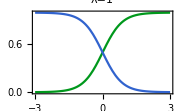

```mathematica
Block[{λ=1},
Plot[Evaluate@Block[{x=10^lgx},{(1-λ+x)/(1+x),λ/(1+x)}],
{lgx,-3,3},PlotStyle->{Green,Blue,Directive[Black,Dotted]},FrameLabel->{"\!\(lg(N ϵ\^2)\)","values"},PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(μ\_z[x]/z\)","\!\(σ\_z\%2[x]\)"}),
PlotLabel->StringTemplate["\!\(λ=`1`\)"][λ],ImageSize->180]]
```

The regularization has the most effect when N ϵ^2 is small, and does not affect the thermodynamic limit. On the other hand, we can also see why λ=1 is the most reasonable choice. Because in the limit of N ϵ^2→0, there is no data to get any clue, and the latent space should remain Gaussian, but this behavior is achieved only when λ=1. Any λ<1 will result in finite fidelity in N ϵ^2→0, which is overfitting.

At λ=1, we find the saddle point solution

b=ϵ, d=(N ϵ)/(1+N ϵ^2), e=1/(√(1+N ϵ^2)),

which amounts to the following maps in the VAE

m(z)=ϵ z, μ_z[x]=(N ϵ)/(1+N ϵ^2)x̄, σ_z^2[x]=1/(1+N ϵ^2).

#### Bifurcation

Suppose p(x̄) has the two-peak structure

p(x̄)=∑_(a=±) p_a exp(-(x̄-μ_a)^2/(2 σ_a)).

The latent space distribution is given by the convolution with the encoding distribution

p(z)=∫ⅆx q(z|x)p(x)
=∑_(a=±) p_a∫ⅆ x̄ exp(-(z-d x̄)^2/(2 e^2))exp(-(x̄-μ_a)^2/(2 σ_a))
=∑_(a=±) p_a exp(-(z-d μ_a)^2/(2(e^2+d^2 σ_a^2))).

```mathematica
Block[{S},
S=-(z-d x)^2/(2e^2)-(x-μ)^2/(2 σ^2);
Simplify[S/.Solve[D[S,x]==0,x]]]
```

{-(z-d μ)^2/(2 (e^2+d^2 σ^2))}

Saddle point.

Even if p(x) bifurcates, p(z) may not, as the Gaussian q(z|x) can further smooth out the distribution and thereby merging bifurcated peaks. Given that

σ_±=1/N,μ_±=±ϵ f(N ϵ^2), d=(N ϵ)/(1+N ϵ^2),e^2=1/(1+N ϵ^2),

where f is the solution of f=tanh(N ϵ^2 f), we can evaluate the effective mean and variance for the latent variable

(μ̃)_a=d μ_a=(N ϵ^2)/(1+N ϵ^2)f(N ϵ^2),
(σ̃)_a^2=e^2+d^2 σ_a^2=(1+2N ϵ^2)/((1+N ϵ^2)^2).

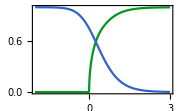

```mathematica
Block[{ϵ=0.1,f},
f[x_]:=FixedPoint[Tanh[x #]&,1,1000,SameTest->(Abs[#1-#2]<1*^-15&)];
ListLinePlot[Thread@Table[Block[{x=10^lgx},{lgx,#}&/@{x/(1+x)f[x],(1+2x)/(1+x)^2}],{lgx,-2,3,0.01}],PlotStyle->{Green,Blue},FrameLabel->{"\!\(lg(N ϵ\^2)\)","values"},PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(μ\&~\_a\)","\!\(\(σ\&~\)\_a\%2\)"}),
ImageSize->180]]
```

## Shadow Classicality

### Pauli Shadow Tomography

#### Measurement Protocol

Pauli measurement protocol

Measurement basis (3^N choices):

S=(S_1,S_2,…), S_i∈{X,Y,Z}.

Measurement outcome (2^N choices):

b=(b_1,b_2,…), b_i∈{+1,-1}.

Classical snapshot

σ_(b,S)=∏_i (𝟙+b_i S_i)/2.

Probability to obtain a snapshot σ_(b,S) on a given state ρ is

P_ρ(b,S)=P_ρ(b|S)P(S),

where

P(S)=3^-N is the probability to sample observables, which is fixed by the randomized measurement scheme, and is independent of the underlying state ρ.

P_ρ(b|S) is the conditional probability to obtain b by measuring S, which is ρ dependent, and is given by

P_ρ(b|S)=Tr(σ_(b,S)ρ).

This defines the posterior POVM ensemble

ℰ_(σ|ρ)={σ_(b,S)|(b,S)\[Distributed]P_ρ(b,S)}.

#### Reconstruction Channel

Given the posterior POVM, the state can be reconstructed by

ρ=𝔼_((b,S)\[Distributed]P_ρ(b,S))ℳ^-1[σ_(b,S)].

For Pauli measurement, the reconstruction map reads

ℳ^-1[σ]=∏_i (3 σ_i-𝟙),

therefore

ρ=𝔼_((b,S)\[Distributed]P_ρ(b,S))∏_i (𝟙+3 b_i S_i)/2.

We can model the underlying quantum state ρ by modeling the joint probability distribution P_ρ(b,S) (or equivalently P_ρ(b|S) given P(S) fixed).

#### Pauli Observable Expectation

Given a Pauli string

O_A=∏_(i∈A) O_i,

evaluate the expectation value

⟨O_A⟩_ρ=Tr O_A ρ
=∑_(S_A=O_A) ∑_b_A P_ρ(b_A|S_A)∏_(i∈A) b_i,

where

S_A=O_A means to pick any S such that S_i matches with O_i for all i∈A.

P_ρ(b_A|S_A) is the marginalization of P_ρ(b|S) to region A.

Prove Eq. (DisplayFormulaNumbered)

⟨O_A⟩=Tr O_A ρ
=𝔼_((b,S)\[Distributed]P_ρ(b,S))Tr(∏_(i∈A) O_i∏_i (𝟙+3 b_i S_i)/2),
=𝔼_((b,S)\[Distributed]P_ρ(b,S))∏_(i∈A) Tr(O_i(𝟙+3 b_i S_i)/2)∏_(i∈Ā) Tr((𝟙+3 b_i S_i)/2)
=𝔼_((b,S)\[Distributed]P_ρ(b,S))∏_(i∈A) (3 b_i δ_(O_i S_i))
=∑_(b,S) P_ρ(b|S)P(S)3^(|A|)∏_(i∈A) (b_i δ_(O_i S_i))
=∑_(S_A=O_A) ∑_b P_ρ(b|S)∏_(i∈A) b_i

The reconstructed density matrix is equivalent to

ρ=1/2^N∑_(O∈Pauli) ⟨O⟩_ρ O,

as a linear combination of Pauli operators, whose coefficient are the corresponding expectation values.

#### Latent Decomposition

Introduce latent variable z∈Z to model P_ρ(b,S),

P_ρ(b,S)=∫_Z ⅆz P_ρ(b|z)P_ρ(z|S).

This corresponds to the causal model

S→z→b.

The latent variable z can be found by the singular value decomposition of P_ρ(b,S).

#### Test States

##### Product State

Stabilized by

H=-∑_i Z_i.

Ground state

ρ=∏_i (𝟙+Z_i)/2.

##### GHZ State

Stabilized by

H=-∑_i Z_i Z_(i+1)-g ∏_i X_i

Ground state for g>0 (pure)

ρ=(𝟙+∏_i X_i)/2∏_(i=1)^(N-1) (𝟙+Z_i Z_(i+1))/2.

Ground state for g=0 (mixed)

ρ=∏_(i=1)^(N-1) (𝟙+Z_i Z_(i+1))/2.

##### 5-Qubit Code

Stabilized by

H=-∑_i X_i Z_(i+1)Z_(i+2)X_(i+3)-g∏_i Z_i.

Ground state for g>0 (pure)

ρ=(𝟙+∏_i Z_i)/2∏_(i=1)^(N-1) (𝟙+X_i Z_(i+1)Z_(i+2)X_(i+3))/2.

Ground state for g=0 (mixed)

ρ=∏_(i=1)^(N-1) (𝟙+X_i Z_(i+1)Z_(i+2)X_(i+3))/2.

### Emergent Classicality

#### Product State

Construct the P_ρ(b|S) matrix and perform SVD.

##### N=2

```mathematica
Block[{n=2,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=RotateLeft[σ@@PadLeft[{3},n],#]&/@Range[n];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XX | XY | XZ | YX | YY | YZ | ZX | ZY | ZZ
++ | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/2 | 1/2 | 1
+- | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/2 | 1/2 | 0
-+ | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0
-- | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0
1.70711 | 0.707107 | 0.707107 | 0.292893
0.853553 ++
0.353553 +-
0.353553 -+
0.146447 -- | 0.5 ++
-0.5 +-
-0.5 -+
-0.5 -- | 0.707107 +-
-0.707107 -+ | 0.853553 --
-0.353553 -+
-0.353553 +-
0.146447 ++
0.5 ZZ
0.353553 ZY
0.353553 ZX
0.353553 YZ
0.353553 XZ
0.25 XX
0.25 YY
0.25 YX
0.25 XY | 0.707107 ZZ
-0.353553 XY
-0.353553 YY
-0.353553 YX
-0.353553 XX | 0.5 ZY
0.5 ZX
-0.5 YZ
-0.5 XZ | 0.5 ZZ
-0.353553 ZY
-0.353553 ZX
-0.353553 YZ
-0.353553 XZ
0.25 YY
0.25 YX
0.25 XY
0.25 XX

##### N=3

```mathematica
Block[{n=3,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=RotateLeft[σ@@PadLeft[{3},n],#]&/@Range[n];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XXX | XXY | XXZ | XYX | XYY | XYZ | XZX | XZY | XZZ | YXX | YXY | YXZ | YYX | YYY | YYZ | YZX | YZY | YZZ | ZXX | ZXY | ZXZ | ZYX | ZYY | ZYZ | ZZX | ZZY | ZZZ
+++ | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/2 | 1/2 | 1
++- | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/2 | 1/2 | 0
+-+ | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0
+-- | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0
-++ | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+- | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
--+ | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
--- | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.23044 | 0.92388 | 0.92388 | 0.92388 | 0.382683 | 0.382683 | 0.382683 | 0.158513
0.788581 +++
0.326641 ++-
0.326641 -++
0.326641 +-+
0.135299 +--
0.135299 -+-
0.135299 --+
0.0560427 --- | 0.565758 +++
-0.344816 -+-
-0.344816 +--
-0.344816 --+
-0.299057 ++-
-0.299057 -++
-0.299057 +-+
-0.234345 --- | 0.74959 +-+
-0.448026 ++-
-0.31049 -+-
-0.301564 -++
0.185579 --+
0.124912 +-- | 0.691444 -++
-0.606884 ++-
-0.286406 +--
0.251379 --+
-0.0845604 +-+
0.0350261 -+- | 0.667441 -+-
-0.438498 -++
0.373873 ---
-0.310882 +--
0.236324 --+
-0.211838 ++-
0.154863 +++
-0.0332635 +-+ | 0.751959 --+
-0.420326 -+-
-0.333816 +--
0.312612 ++-
-0.172964 +-+
-0.137131 -++
-0.00137678 ---
-0.000570281 +++ | 0.671111 +--
-0.430704 +-+
0.424617 ---
-0.271896 ++-
0.192819 --+
-0.190578 -+-
0.175882 +++
-0.0737812 -++ | 0.788581 ---
-0.326641 --+
-0.326641 +--
-0.326641 -+-
0.135299 +-+
0.135299 -++
0.135299 ++-
-0.0560427 +++
0.353553 ZZZ
0.25 ZZY
0.25 ZZX
0.25 ZYZ
0.25 ZXZ
0.25 YZZ
0.25 XZZ
0.176777 ZYY
0.176777 ZYX
0.176777 ZXY
0.176777 ZXX
0.176777 YZY
0.176777 YZX
0.176777 XZY
0.176777 XZX
0.176777 XXZ
0.176777 YYZ
0.176777 YXZ
0.176777 XYZ
0.125 XXY
0.125 YYY
0.125 YYX
0.125 YXY
0.125 YXX
0.125 XYY
0.125 XYX
0.125 XXX | 0.612372 ZZZ
-0.216506 XXY
-0.216506 YYY
-0.216506 YYX
-0.216506 YXY
-0.216506 YXX
-0.216506 XYY
-0.216506 XYX
-0.216506 XXX
0.144338 ZYZ
0.144338 ZXZ
0.144338 YZZ
0.144338 XZZ
0.144338 ZZY
0.144338 ZZX
-0.102062 YZY
-0.102062 YZX
-0.102062 XZY
-0.102062 XZX
-0.102062 ZYY
-0.102062 ZYX
-0.102062 ZXY
-0.102062 ZXX
-0.102062 XXZ
-0.102062 YYZ
-0.102062 YXZ
-0.102062 XYZ | 0.405675 ZYZ
0.405675 ZXZ
-0.286856 YZY
-0.286856 YZX
-0.286856 XZY
-0.286856 XZX
-0.24247 ZZY
-0.24247 ZZX
0.171452 XYZ
0.171452 XXZ
0.171452 YYZ
0.171452 YXZ
-0.163205 YZZ
-0.163205 XZZ
0.115403 ZYY
0.115403 ZYX
0.115403 ZXY
0.115403 ZXX | 0.374207 YZZ
0.374207 XZZ
-0.328443 ZZY
-0.328443 ZZX
-0.264604 ZYY
-0.264604 ZYX
-0.264604 ZXY
-0.264604 ZXX
0.232244 YYZ
0.232244 YXZ
0.232244 XYZ
0.232244 XXZ
-0.0457638 ZYZ
-0.0457638 ZXZ
0.0323599 YZY
0.0323599 YZX
0.0323599 XZY
0.0323599 XZX | 0.404677 ZZZ
-0.370587 YZZ
-0.370587 XZZ
-0.262045 ZYY
-0.262045 ZYX
-0.262045 ZXY
-0.262045 ZXX
0.158878 ZYZ
0.158878 ZXZ
0.143075 XYY
0.143075 XYX
0.143075 YYY
0.143075 YYX
0.143075 YXY
0.143075 YXX
0.143075 XXX
0.143075 XXY
0.112344 YZY
0.112344 YZX
0.112344 XZY
0.112344 XZX
-0.0744407 ZZY
-0.0744407 ZZX
-0.0526376 XYZ
-0.0526376 YYZ
-0.0526376 YXZ
-0.0526376 XXZ | 0.407702 ZZY
0.407702 ZZX
0.288289 XYZ
0.288289 YYZ
0.288289 YXZ
0.288289 XXZ
-0.226734 ZYZ
-0.226734 ZXZ
-0.179915 YZZ
-0.179915 XZZ
-0.160325 XZX
-0.160325 YZY
-0.160325 YZX
-0.160325 XZY
-0.127219 ZYY
-0.127219 ZYX
-0.127219 ZXY
-0.127219 ZXX
-0.00149022 ZZZ
-0.000526871 XYY
-0.000526871 YYY
-0.000526871 YYX
-0.000526871 YXY
-0.000526871 YXX
-0.000526871 XXY
-0.000526871 XXX
-0.000526871 XYX | 0.459602 ZZZ
-0.332941 ZYZ
-0.332941 ZXZ
-0.235425 XZX
-0.235425 YZY
-0.235425 YZX
-0.235425 XZY
0.162494 XXY
0.162494 XXX
0.162494 YYY
0.162494 YYX
0.162494 YXY
0.162494 YXX
0.162494 XYY
0.162494 XYX
0.133401 YZZ
0.133401 XZZ
-0.125448 ZZY
-0.125448 ZZX
0.094329 ZYY
0.094329 ZYX
0.094329 ZXY
0.094329 ZXX
-0.0887053 YYZ
-0.0887053 YXZ
-0.0887053 XXZ
-0.0887053 XYZ | -0.353553 ZZZ
0.25 ZZY
0.25 ZZX
0.25 ZYZ
0.25 ZXZ
0.25 YZZ
0.25 XZZ
-0.176777 XZX
-0.176777 XXZ
-0.176777 YYZ
-0.176777 YXZ
-0.176777 ZYY
-0.176777 ZYX
-0.176777 ZXY
-0.176777 ZXX
-0.176777 XYZ
-0.176777 YZY
-0.176777 YZX
-0.176777 XZY
0.125 XYX
0.125 XXY
0.125 XXX
0.125 XYY
0.125 YYY
0.125 YYX
0.125 YXY
0.125 YXX

##### N=4

```mathematica
Block[{n=4,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=RotateLeft[σ@@PadLeft[{3},n],#]&/@Range[n];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XXXX | XXXY | XXXZ | XXYX | XXYY | XXYZ | XXZX | XXZY | XXZZ | XYXX | XYXY | XYXZ | XYYX | XYYY | XYYZ | XYZX | XYZY | XYZZ | XZXX | XZXY | XZXZ | XZYX | XZYY | XZYZ | XZZX | XZZY | XZZZ | YXXX | YXXY | YXXZ | YXYX | YXYY | YXYZ | YXZX | YXZY | YXZZ | YYXX | YYXY | YYXZ | YYYX | YYYY | YYYZ | YYZX | YYZY | YYZZ | YZXX | YZXY | YZXZ | YZYX | YZYY | YZYZ | YZZX | YZZY | YZZZ | ZXXX | ZXXY | ZXXZ | ZXYX | ZXYY | ZXYZ | ZXZX | ZXZY | ZXZZ | ZYXX | ZYXY | ZYXZ | ZYYX | ZYYY | ZYYZ | ZYZX | ZYZY | ZYZZ | ZZXX | ZZXY | ZZXZ | ZZYX | ZZYY | ZZYZ | ZZZX | ZZZY | ZZZZ
++++ | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/2 | 1/2 | 1
+++- | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/2 | 1/2 | 0
++-+ | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0
++-- | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0
+-++ | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+-+- | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+--+ | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+--- | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+++ | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-++- | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+-+ | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+-- | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
--++ | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
--+- | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
---+ | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
---- | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.91421 | 1.20711 | 1.20711 | 1.20711 | 1.20711 | 0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 0.207107 | 0.207107 | 0.207107 | 0.207107 | 0.0857864
0.728553 ++++
0.301777 ++-+
0.301777 +-++
0.301777 -+++
0.301777 +++-
0.125 ++--
0.125 +-+-
0.125 +--+
0.125 -++-
0.125 -+-+
0.125 --++
0.0517767 --+-
0.0517767 -+--
0.0517767 +---
0.0517767 ---+
0.0214466 ---- | 0.70703 +++-
-0.427172 +-++
0.259452 -++-
-0.259452 +--+
0.21035 ++--
-0.21035 --++
-0.1992 ++-+
-0.121307 ---+
0.115921 +-+-
-0.115921 -+-+
-0.0806572 -+++
0.0732912 -+--
0.0341773 --+-
0.0138386 +--- | 0.592734 +-++
-0.472068 -+++
0.33286 +-+-
-0.33286 -+-+
-0.331526 ++-+
0.21086 +++-
0.108196 +--+
-0.108196 -++-
-0.101697 -+--
0.0809941 +---
0.0568808 --+-
0.0499815 --++
-0.0499815 ++--
-0.0361778 ---+ | 0.603553 ++++
-0.25 ++--
-0.25 -++-
-0.25 +-+-
-0.25 -+-+
-0.25 --++
-0.25 +--+
-0.176777 +++-
-0.176777 -+--
-0.176777 --+-
-0.176777 +---
-0.176777 ---+
-0.176777 -+++
-0.176777 ++-+
-0.176777 +-++
-0.103553 ---- | 0.629941 ++-+
-0.563082 -+++
0.279741 ++--
-0.279741 --++
0.214425 +--+
-0.214425 -++-
-0.112272 +-++
-0.108081 --+-
0.0966095 +---
0.0454129 +++-
0.0276939 -+-+
-0.0276939 +-+-
0.0192628 -+--
-0.00779162 ---+ | 0.521923 -+-+
-0.495015 ++--
-0.348379 +--+
-0.338172 +---
-0.300975 -+++
0.185649 +-+-
0.183943 -++-
0.170035 ++-+
0.133323 +-++
0.132838 --+-
0.0961264 -+--
-0.0853178 --++
0.0720105 +++-
0.0348141 ---+
-0.0185982 ----
-0.0185982 ++++ | 0.477422 +++-
0.450572 +--+
-0.420333 +-+-
-0.341377 ++--
-0.263269 --+-
0.245758 ---+
-0.232331 -+--
-0.213485 +---
-0.115832 ++++
-0.115832 ----
0.0869289 --++
-0.0773018 -++-
0.0698472 -+-+
-0.0316053 ++-+
0.0181787 -+++
-0.000667887 +-++ | 0.578333 --++
-0.440573 +--+
0.37742 ++--
-0.341948 -++-
-0.293981 +-+-
-0.178567 +---
-0.178567 -+++
0.129254 ---+
0.129254 +++-
0.120749 -+-+
0.0781108 -+--
0.0781108 +-++
-0.0287978 --+-
-0.0287978 ++-+ | 0.488701 +-++
-0.374533 +-+-
-0.356002 ---+
0.327375 -++-
-0.278123 --++
-0.252256 --+-
-0.238904 +---
0.221472 ++--
-0.17923 ++++
-0.17923 ----
-0.145517 +--+
0.130242 -+--
0.119556 -+++
-0.109134 -+-+
0.106204 ++-+
0.00245797 +++- | 0.521355 -+-+
-0.425485 -++-
-0.406146 --++
-0.347907 --+-
-0.347907 ++-+
0.174309 ++--
0.155138 -+++
0.155138 +---
0.135818 +-+-
0.135089 -+--
0.135089 +-++
0.0576793 ---+
0.0576793 +++-
0.00014991 +--+ | 0.420379 -+--
0.385745 -++-
-0.370754 +-+-
-0.346534 -+++
-0.34379 ++-+
0.269944 ---+
0.232566 +--+
0.218778 ++++
0.218778 ----
-0.167611 +++-
0.134782 -+-+
0.101453 ++--
0.0937659 --+-
0.0910219 +---
-0.0462372 --++
-0.0171766 +-++ | 0.673598 +---
-0.475326 -+--
0.288265 -++-
-0.240836 +--+
0.235064 -+-+
-0.196893 --+-
-0.187635 +-+-
-0.135217 -+++
0.119733 --++
-0.0723042 ++--
-0.0684542 ---+
0.0619072 +-++
-0.0572521 ----
0.0141357 ++-+
0.0098229 ++++
-0.00790093 +++- | 0.573018 -+--
-0.428612 --+-
-0.400414 ---+
0.346328 --++
-0.332158 ++--
0.235967 +---
-0.104184 +-++
0.0827309 +-+-
0.0710509 +--+
-0.0685601 -+-+
0.0676684 ++-+
0.0628304 +++-
-0.0568802 -++-
-0.0463552 -+++
-0.0171056 ----
0.00293486 ++++ | 0.600525 ----
-0.27541 +--+
-0.26729 ++--
-0.262765 +-+-
0.247385 +---
-0.234726 -+-+
-0.230201 --++
-0.222081 -++-
0.182349 ++-+
0.180475 +-++
0.177111 +++-
0.168769 ---+
0.163623 -+++
0.149164 -+--
0.13824 --+-
-0.103034 ++++ | 0.619811 ---+
-0.579724 --+-
0.276412 +-+-
-0.269162 -+-+
0.227702 -++-
-0.220452 +--+
-0.109346 +++-
0.096462 ++-+
-0.0839679 +---
0.0336287 -+--
0.0223527 ++--
-0.015103 --++
0.0114037 -+++
-0.00877269 +-++
-0.00875114 ----
0.00150146 ++++ | 0.728553 ----
-0.301777 --+-
-0.301777 -+--
-0.301777 +---
-0.301777 ---+
0.125 -++-
0.125 --++
0.125 +-+-
0.125 ++--
0.125 -+-+
0.125 +--+
-0.0517767 +++-
-0.0517767 ++-+
-0.0517767 -+++
-0.0517767 +-++
0.0214466 ++++
0.25 ZZZZ
0.176777 ZZYZ
0.176777 ZZXZ
0.176777 ZYZZ
0.176777 ZXZZ
0.176777 YZZZ
0.176777 XZZZ
0.176777 ZZZY
0.176777 ZZZX
0.125 ZZYY
0.125 ZZYX
0.125 ZZXY
0.125 ZZXX
0.125 ZYZY
0.125 ZYZX
0.125 ZXZY
0.125 ZXZX
0.125 YZZY
0.125 YZZX
0.125 YZYZ
0.125 YZXZ
0.125 XZZY
0.125 XZZX
0.125 XZYZ
0.125 XZXZ
0.125 XXZZ
0.125 ZYYZ
0.125 ZYXZ
0.125 ZXYZ
0.125 ZXXZ
0.125 YYZZ
0.125 YXZZ
0.125 XYZZ
0.0883883 YZYY
0.0883883 YZYX
0.0883883 YZXY
0.0883883 YZXX
0.0883883 YYZY
0.0883883 YYZX
0.0883883 YXZY
0.0883883 YXZX
0.0883883 XZYY
0.0883883 XZYX
0.0883883 XZXY
0.0883883 XZXX
0.0883883 XYZY
0.0883883 XYZX
0.0883883 ZYYY
0.0883883 ZYYX
0.0883883 ZYXY
0.0883883 ZYXX
0.0883883 ZXYY
0.0883883 ZXYX
0.0883883 ZXXY
0.0883883 ZXXX
0.0883883 YYYZ
0.0883883 YYXZ
0.0883883 YXYZ
0.0883883 YXXZ
0.0883883 XYYZ
0.0883883 XYXZ
0.0883883 XXZY
0.0883883 XXZX
0.0883883 XXYZ
0.0883883 XXXZ
0.0625 XXYX
0.0625 YYYY
0.0625 YYYX
0.0625 YYXY
0.0625 YYXX
0.0625 YXYY
0.0625 YXYX
0.0625 YXXY
0.0625 YXXX
0.0625 XYYY
0.0625 XYYX
0.0625 XYXY
0.0625 XYXX
0.0625 XXYY
0.0625 XXXY
0.0625 XXXX | 0.292861 ZZZY
0.292861 ZZZX
0.18346 YZZY
0.18346 YZZX
0.18346 XZZY
0.18346 XZZX
-0.18346 ZYYZ
-0.18346 ZYXZ
-0.18346 ZXYZ
-0.18346 ZXXZ
-0.176941 ZYZZ
-0.176941 ZXZZ
0.14874 ZZYY
0.14874 ZZYX
0.14874 ZZXY
0.14874 ZZXX
-0.14874 XXZZ
-0.14874 YYZZ
-0.14874 YXZZ
-0.14874 XYZZ
-0.146431 XYYZ
-0.146431 YYYZ
-0.146431 YYXZ
-0.146431 YXYZ
-0.146431 YXXZ
-0.146431 XYXZ
-0.146431 XXXZ
-0.146431 XXYZ
0.0884703 YZYY
0.0884703 YZYX
0.0884703 YZXY
0.0884703 YZXX
0.0884703 XZYY
0.0884703 XZYX
0.0884703 XZXY
0.0884703 XZXX
-0.0825114 ZZYZ
-0.0825114 ZZXZ
0.0819683 ZYZY
0.0819683 ZYZX
0.0819683 ZXZY
0.0819683 ZXZX
-0.0819683 YZYZ
-0.0819683 YZXZ
-0.0819683 XZYZ
-0.0819683 XZXZ
0.0412557 XXZX
0.0412557 YYZY
0.0412557 YYZX
0.0412557 YXZY
0.0412557 YXZX
0.0412557 XYZY
0.0412557 XYZX
0.0412557 XXZY
-0.0334093 YZZZ
-0.0334093 XZZZ
0.0167046 ZYYY
0.0167046 ZYYX
0.0167046 ZYXY
0.0167046 ZYXX
0.0167046 ZXYY
0.0167046 ZXYX
0.0167046 ZXXY
0.0167046 ZXXX | 0.245519 ZYZZ
0.245519 ZXZZ
0.235367 ZYZY
0.235367 ZYZX
0.235367 ZXZY
0.235367 ZXZX
-0.235367 YZYZ
-0.235367 YZXZ
-0.235367 XZYZ
-0.235367 XZXZ
-0.195537 YZZZ
-0.195537 XZZZ
-0.137322 ZZYZ
-0.137322 ZZXZ
-0.122759 YZYY
-0.122759 YZYX
-0.122759 YZXY
-0.122759 YZXX
-0.122759 XZYY
-0.122759 XZYX
-0.122759 XZXY
-0.122759 XZXX
0.0977685 ZYYY
0.0977685 ZYYX
0.0977685 ZYXY
0.0977685 ZYXX
0.0977685 ZXYY
0.0977685 ZXYX
0.0977685 ZXXY
0.0977685 ZXXX
0.0873409 ZZZY
0.0873409 ZZZX
0.0765062 ZYYZ
0.0765062 ZYXZ
0.0765062 ZXYZ
0.0765062 ZXXZ
-0.0765062 YZZY
-0.0765062 YZZX
-0.0765062 XZZY
-0.0765062 XZZX
0.0686612 XXZY
0.0686612 XXZX
0.0686612 YYZY
0.0686612 YYZX
0.0686612 YXZY
0.0686612 YXZX
0.0686612 XYZY
0.0686612 XYZX
-0.0436705 XXXZ
-0.0436705 YYYZ
-0.0436705 YYXZ
-0.0436705 YXYZ
-0.0436705 YXXZ
-0.0436705 XYYZ
-0.0436705 XYXZ
-0.0436705 XXYZ
0.0353422 YYZZ
0.0353422 YXZZ
0.0353422 XYZZ
0.0353422 XXZZ
-0.0353422 ZZYY
-0.0353422 ZZYX
-0.0353422 ZZXY
-0.0353422 ZZXX | 0.5 ZZZZ
0.176777 ZYZZ
0.176777 ZXZZ
0.176777 ZZYZ
0.176777 ZZXZ
0.176777 YZZZ
0.176777 XZZZ
0.176777 ZZZY
0.176777 ZZZX
-0.125 XXYX
-0.125 XXXX
-0.125 XYXX
-0.125 YYYY
-0.125 YYYX
-0.125 YYXY
-0.125 YYXX
-0.125 YXYY
-0.125 YXYX
-0.125 YXXY
-0.125 YXXX
-0.125 XYYY
-0.125 XYYX
-0.125 XYXY
-0.125 XXYY
-0.125 XXXY
-0.0883883 YZYY
-0.0883883 YZYX
-0.0883883 YZXY
-0.0883883 YZXX
-0.0883883 XZYY
-0.0883883 XZYX
-0.0883883 XZXY
-0.0883883 XZXX
-0.0883883 YYZY
-0.0883883 YYZX
-0.0883883 YXZY
-0.0883883 YXZX
-0.0883883 XYZY
-0.0883883 XYZX
-0.0883883 XXZX
-0.0883883 ZYYY
-0.0883883 ZYYX
-0.0883883 ZYXY
-0.0883883 ZYXX
-0.0883883 ZXYY
-0.0883883 ZXYX
-0.0883883 ZXXY
-0.0883883 ZXXX
-0.0883883 XXZY
-0.0883883 XYYZ
-0.0883883 XXYZ
-0.0883883 YYYZ
-0.0883883 YYXZ
-0.0883883 YXYZ
-0.0883883 YXXZ
-0.0883883 XYXZ
-0.0883883 XXXZ | 0.26093 ZZYZ
0.26093 ZZXZ
-0.233236 YZZZ
-0.233236 XZZZ
0.197806 ZZYY
0.197806 ZZYX
0.197806 ZZXY
0.197806 ZZXX
-0.197806 XXZZ
-0.197806 YYZZ
-0.197806 YXZZ
-0.197806 XYZZ
0.151622 ZYYZ
0.151622 ZYXZ
0.151622 ZXYZ
0.151622 ZXXZ
-0.151622 YZZY
-0.151622 YZZX
-0.151622 XZZY
-0.151622 XZZX
-0.130465 YYZY
-0.130465 YYZX
-0.130465 YXZY
-0.130465 YXZX
-0.130465 XYZY
-0.130465 XYZX
-0.130465 XXZX
-0.130465 XXZY
0.116618 ZYYY
0.116618 ZYYX
0.116618 ZYXY
0.116618 ZYXX
0.116618 ZXYY
0.116618 ZXYX
0.116618 ZXXY
0.116618 ZXXX
-0.0465045 ZYZZ
-0.0465045 ZXZZ
0.0232522 YZYY
0.0232522 YZYX
0.0232522 YZXY
0.0232522 YZXX
0.0232522 XZYY
0.0232522 XZYX
0.0232522 XZXY
0.0232522 XZXX
0.0195825 YZYZ
0.0195825 YZXZ
0.0195825 XZYZ
0.0195825 XZXZ
-0.0195825 ZYZY
-0.0195825 ZYZX
-0.0195825 ZXZY
-0.0195825 ZXZX
0.0188106 ZZZY
0.0188106 ZZZX
-0.00940531 XYXZ
-0.00940531 YYYZ
-0.00940531 YYXZ
-0.00940531 YXYZ
-0.00940531 YXXZ
-0.00940531 XYYZ
-0.00940531 XXXZ
-0.00940531 XXYZ | -0.319573 YZZZ
-0.319573 XZZZ
0.186192 YZYZ
0.186192 YZXZ
0.186192 XZYZ
0.186192 XZXZ
0.186192 ZYZY
0.186192 ZYZX
0.186192 ZXZY
0.186192 ZXZX
-0.159787 ZYYY
-0.159787 ZYYX
-0.159787 ZYXY
-0.159787 ZYXX
-0.159787 ZXYY
-0.159787 ZXYX
-0.159787 ZXXY
-0.159787 ZXXX
0.151437 ZZYZ
0.151437 ZZXZ
-0.135784 YYZZ
-0.135784 YXZZ
-0.135784 XYZZ
-0.135784 XXZZ
-0.135784 ZZYY
-0.135784 ZZYX
-0.135784 ZZXY
-0.135784 ZZXX
0.114725 ZYZZ
0.114725 ZXZZ
0.0757183 XXZY
0.0757183 YYZY
0.0757183 YYZX
0.0757183 YXZY
0.0757183 YXZX
0.0757183 XYZY
0.0757183 XYZX
0.0757183 XXZX
0.0573623 YZYY
0.0573623 YZYX
0.0573623 YZXY
0.0573623 YZXX
0.0573623 XZYY
0.0573623 XZYX
0.0573623 XZXY
0.0573623 XZXX
0.0534123 ZZZY
0.0534123 ZZZX
-0.0371964 ZZZZ
-0.0318098 ZYYZ
-0.0318098 ZYXZ
-0.0318098 ZXYZ
-0.0318098 ZXXZ
-0.0318098 YZZY
-0.0318098 YZZX
-0.0318098 XZZY
-0.0318098 XZZX
0.0267061 XXXZ
0.0267061 XXYZ
0.0267061 XYXZ
0.0267061 XYYZ
0.0267061 YYYZ
0.0267061 YYXZ
0.0267061 YXYZ
0.0267061 YXXZ
-0.00929911 XXYX
-0.00929911 XYXY
-0.00929911 YYYY
-0.00929911 YYYX
-0.00929911 YYXY
-0.00929911 YYXX
-0.00929911 YXYY
-0.00929911 YXYX
-0.00929911 YXXY
-0.00929911 YXXX
-0.00929911 XYYY
-0.00929911 XYYX
-0.00929911 XXXX
-0.00929911 XYXX
-0.00929911 XXXY
-0.00929911 XXYY | 0.36159 ZZZY
0.36159 ZZZX
-0.231664 ZZZZ
0.180795 XXXZ
0.180795 YYYZ
0.180795 YYXZ
0.180795 YXYZ
0.180795 YXXZ
0.180795 XYYZ
0.180795 XYXZ
0.180795 XXYZ
0.151233 ZYYZ
0.151233 ZYXZ
0.151233 ZXYZ
0.151233 ZXXZ
0.151233 YZZY
0.151233 YZZX
0.151233 XZZY
0.151233 XZZX
-0.147437 ZZYZ
-0.147437 ZZXZ
-0.1165 ZYZZ
-0.1165 ZXZZ
-0.097653 YZZZ
-0.097653 XZZZ
-0.0737186 XXZX
-0.0737186 YYZY
-0.0737186 YYZX
-0.0737186 YXZY
-0.0737186 YXZX
-0.0737186 XYZY
-0.0737186 XYZX
-0.0737186 XXZY
-0.0582498 YZYY
-0.0582498 YZYX
-0.0582498 YZXY
-0.0582498 YZXX
-0.0582498 XZYY
-0.0582498 XZYX
-0.0582498 XZXY
-0.0582498 XZXX
-0.0579159 XXYY
-0.0579159 XXYX
-0.0579159 XYYX
-0.0579159 YYYY
-0.0579159 YYYX
-0.0579159 YYXY
-0.0579159 YYXX
-0.0579159 YXYY
-0.0579159 YXYX
-0.0579159 YXXY
-0.0579159 YXXX
-0.0579159 XYYY
-0.0579159 XYXX
-0.0579159 XYXY
-0.0579159 XXXX
-0.0579159 XXXY
-0.0488265 ZYYY
-0.0488265 ZYYX
-0.0488265 ZYXY
-0.0488265 ZYXX
-0.0488265 ZXYY
-0.0488265 ZXYX
-0.0488265 ZXXY
-0.0488265 ZXXX
-0.0297056 ZYZY
-0.0297056 ZYZX
-0.0297056 ZXZY
-0.0297056 ZXZX
-0.0297056 YZYZ
-0.0297056 YZXZ
-0.0297056 XZYZ
-0.0297056 XZXZ
-0.00569602 ZZYY
-0.00569602 ZZYX
-0.00569602 ZZXY
-0.00569602 ZZXX
-0.00569602 XXZZ
-0.00569602 YYZZ
-0.00569602 YXZZ
-0.00569602 XYZZ | 0.238938 XXZZ
0.238938 ZZYY
0.238938 ZZYX
0.238938 ZZXY
0.238938 ZZXX
0.238938 YYZZ
0.238938 YXZZ
0.238938 XYZZ
-0.19563 YZZY
-0.19563 YZZX
-0.19563 XZZY
-0.19563 XZZX
-0.19563 ZYYZ
-0.19563 ZYXZ
-0.19563 ZXYZ
-0.19563 ZXXZ
-0.178567 YZZZ
-0.178567 XZZZ
0.129254 ZZZY
0.129254 ZZZX
-0.0892836 ZYYY
-0.0892836 ZYYX
-0.0892836 ZYXY
-0.0892836 ZYXX
-0.0892836 ZXYY
-0.0892836 ZXYX
-0.0892836 ZXXY
-0.0892836 ZXXX
0.0781108 ZYZZ
0.0781108 ZXZZ
0.0646272 YYYZ
0.0646272 YYXZ
0.0646272 YXYZ
0.0646272 YXXZ
0.0646272 XYYZ
0.0646272 XYXZ
0.0646272 XXXZ
0.0646272 XXYZ
-0.0433079 ZYZY
-0.0433079 ZYZX
-0.0433079 ZXZY
-0.0433079 ZXZX
-0.0433079 YZYZ
-0.0433079 YZXZ
-0.0433079 XZYZ
-0.0433079 XZXZ
0.0390554 YZYY
0.0390554 YZYX
0.0390554 YZXY
0.0390554 YZXX
0.0390554 XZYY
0.0390554 XZYX
0.0390554 XZXY
0.0390554 XZXX
-0.0287978 ZZYZ
-0.0287978 ZZXZ
-0.0143989 XXZX
-0.0143989 YYZY
-0.0143989 YYZX
-0.0143989 YXZY
-0.0143989 YXZX
-0.0143989 XYZY
-0.0143989 XYZX
-0.0143989 XXZY | -0.35846 ZZZZ
0.309471 ZYZZ
0.309471 ZXZZ
-0.176772 ZZZY
-0.176772 ZZZX
0.154736 YZYY
0.154736 YZYX
0.154736 YZXY
0.154736 YZXX
0.154736 XZYY
0.154736 XZYX
0.154736 XZXY
0.154736 XZXX
0.13508 ZYYZ
0.13508 ZYXZ
0.13508 ZXYZ
0.13508 ZXXZ
0.13508 YZZY
0.13508 YZZX
0.13508 XZZY
0.13508 XZZX
-0.089615 XYYY
-0.089615 XYXX
-0.089615 YYYY
-0.089615 YYYX
-0.089615 YYXY
-0.089615 YYXX
-0.089615 YXYY
-0.089615 YXYX
-0.089615 YXXY
-0.089615 YXXX
-0.089615 XYYX
-0.089615 XYXY
-0.089615 XXXY
-0.089615 XXXX
-0.089615 XXYX
-0.089615 XXYY
-0.088386 XXYZ
-0.088386 XXXZ
-0.088386 XYYZ
-0.088386 YYYZ
-0.088386 YYXZ
-0.088386 YXYZ
-0.088386 YXXZ
-0.088386 XYXZ
0.0754521 ZZYY
0.0754521 ZZYX
0.0754521 ZZXY
0.0754521 ZZXX
0.0754521 YYZZ
0.0754521 YXZZ
0.0754521 XYZZ
0.0754521 XXZZ
-0.0730257 ZZYZ
-0.0730257 ZZXZ
-0.0596739 YZZZ
-0.0596739 XZZZ
-0.0365128 YYZY
-0.0365128 YYZX
-0.0365128 YXZY
-0.0365128 YXZX
-0.0365128 XYZY
-0.0365128 XYZX
-0.0365128 XXZX
-0.0365128 XXZY
-0.0313017 ZYZY
-0.0313017 ZYZX
-0.0313017 ZXZY
-0.0313017 ZXZX
-0.0313017 YZYZ
-0.0313017 YZXZ
-0.0313017 XZYZ
-0.0313017 XZXZ
-0.0298369 ZYYY
-0.0298369 ZYYX
-0.0298369 ZYXY
-0.0298369 ZYXX
-0.0298369 ZXYY
-0.0298369 ZXYX
-0.0298369 ZXXY
-0.0298369 ZXXX | -0.347907 ZZYZ
-0.347907 ZZXZ
-0.173953 YYZY
-0.173953 YYZX
-0.173953 YXZY
-0.173953 YXZX
-0.173953 XYZY
-0.173953 XYZX
-0.173953 XXZY
-0.173953 XXZX
0.164293 YZYZ
0.164293 YZXZ
0.164293 XZYZ
0.164293 XZXZ
0.164293 ZYZY
0.164293 ZYZX
0.164293 ZXZY
0.164293 ZXZX
0.155138 YZZZ
0.155138 XZZZ
0.135089 ZYZZ
0.135089 ZXZZ
-0.106334 YZZY
-0.106334 YZZX
-0.106334 XZZY
-0.106334 XZZX
-0.106334 ZYYZ
-0.106334 ZYXZ
-0.106334 ZXYZ
-0.106334 ZXXZ
0.0775692 ZYYY
0.0775692 ZYYX
0.0775692 ZYXY
0.0775692 ZYXX
0.0775692 ZXYY
0.0775692 ZXYX
0.0775692 ZXXY
0.0775692 ZXXX
0.0675447 YZYY
0.0675447 YZYX
0.0675447 YZXY
0.0675447 YZXX
0.0675447 XZYY
0.0675447 XZYX
0.0675447 XZXY
0.0675447 XZXX
-0.0579593 XXZZ
-0.0579593 YYZZ
-0.0579593 YXZZ
-0.0579593 XYZZ
-0.0579593 ZZYY
-0.0579593 ZZYX
-0.0579593 ZZXY
-0.0579593 ZZXX
0.0576793 ZZZY
0.0576793 ZZZX
0.0288396 XYYZ
0.0288396 YYYZ
0.0288396 YYXZ
0.0288396 YXYZ
0.0288396 YXXZ
0.0288396 XYXZ
0.0288396 XXYZ
0.0288396 XXXZ | 0.437556 ZZZZ
0.201601 ZYZZ
0.201601 ZXZZ
-0.168382 ZYZY
-0.168382 ZYZX
-0.168382 ZXZY
-0.168382 ZXZX
-0.168382 YZYZ
-0.168382 YZXZ
-0.168382 XZYZ
-0.168382 XZXZ
-0.127756 YZZZ
-0.127756 XZZZ
-0.125012 ZZYZ
-0.125012 ZZXZ
0.109389 XXYX
0.109389 XYXX
0.109389 YYYY
0.109389 YYYX
0.109389 YYXY
0.109389 YYXX
0.109389 YXYY
0.109389 YXYX
0.109389 YXXY
0.109389 YXXX
0.109389 XYYY
0.109389 XYYX
0.109389 XXYY
0.109389 XYXY
0.109389 XXXX
0.109389 XXXY
0.100801 YZYY
0.100801 YZYX
0.100801 YZXY
0.100801 YZXX
0.100801 XZYY
0.100801 XZYX
0.100801 XZXY
0.100801 XZXX
-0.0955849 XXZZ
-0.0955849 YYZZ
-0.0955849 YXZZ
-0.0955849 XYZZ
-0.0955849 ZZYY
-0.0955849 ZZYX
-0.0955849 ZZXY
-0.0955849 ZZXX
-0.063878 ZYYY
-0.063878 ZYYX
-0.063878 ZYXY
-0.063878 ZYXX
-0.063878 ZXYY
-0.063878 ZXYX
-0.063878 ZXXY
-0.063878 ZXXX
-0.062506 YYZY
-0.062506 YYZX
-0.062506 YXZY
-0.062506 YXZX
-0.062506 XYZY
-0.062506 XYZX
-0.062506 XXZY
-0.062506 XXZX
0.0511667 ZZZY
0.0511667 ZZZX
0.0451889 ZYYZ
0.0451889 ZYXZ
0.0451889 ZXYZ
0.0451889 ZXXZ
0.0451889 YZZY
0.0451889 YZZX
0.0451889 XZZY
0.0451889 XZZX
0.0255833 XXYZ
0.0255833 XYYZ
0.0255833 XYXZ
0.0255833 YYYZ
0.0255833 YYXZ
0.0255833 YXYZ
0.0255833 YXXZ
0.0255833 XXXZ | -0.302728 YZZZ
-0.302728 XZZZ
0.187066 YZZY
0.187066 YZZX
0.187066 XZZY
0.187066 XZZX
-0.187066 ZYYZ
-0.187066 ZYXZ
-0.187066 ZXYZ
-0.187066 ZXXZ
0.173172 ZYZZ
0.173172 ZXZZ
0.151364 ZYYY
0.151364 ZYYX
0.151364 ZYXY
0.151364 ZYXX
0.151364 ZXYY
0.151364 ZXYX
0.151364 ZXXY
0.151364 ZXXX
0.149447 YZYZ
0.149447 YZXZ
0.149447 XZYZ
0.149447 XZXZ
-0.149447 ZYZY
-0.149447 ZYZX
-0.149447 ZXZY
-0.149447 ZXZX
-0.0865859 YZYY
-0.0865859 YZYX
-0.0865859 YZXY
-0.0865859 YZXX
-0.0865859 XZYY
-0.0865859 XZYX
-0.0865859 XZXY
-0.0865859 XZXX
0.0678956 XXZZ
0.0678956 YYZZ
0.0678956 YXZZ
0.0678956 XYZZ
-0.0678956 ZZYY
-0.0678956 ZZYX
-0.0678956 ZZXY
-0.0678956 ZZXX
0.0578413 ZZYZ
0.0578413 ZZXZ
0.0474292 ZZZZ
-0.0289206 YYZY
-0.0289206 YYZX
-0.0289206 YXZY
-0.0289206 YXZX
-0.0289206 XYZY
-0.0289206 XYZX
-0.0289206 XXZY
-0.0289206 XXZX
-0.0118573 XXXY
-0.0118573 XXXX
-0.0118573 XYYX
-0.0118573 XYYY
-0.0118573 XXYX
-0.0118573 YYYY
-0.0118573 YYYX
-0.0118573 YYXY
-0.0118573 YYXX
-0.0118573 YXYY
-0.0118573 YXYX
-0.0118573 YXXY
-0.0118573 YXXX
-0.0118573 XYXX
-0.0118573 XYXY
-0.0118573 XXYY
0.00464006 ZZZY
0.00464006 ZZZX
-0.00232003 XYXZ
-0.00232003 XYYZ
-0.00232003 XXXZ
-0.00232003 YYYZ
-0.00232003 YYXZ
-0.00232003 YXYZ
-0.00232003 YXXZ
-0.00232003 XXYZ | -0.244437 ZYZZ
-0.244437 ZXZZ
0.239881 XXZZ
0.239881 YYZZ
0.239881 YXZZ
0.239881 XYZZ
-0.239881 ZZYY
-0.239881 ZZYX
-0.239881 ZZXY
-0.239881 ZZXX
0.170451 ZZYZ
0.170451 ZZXZ
0.158771 ZZZY
0.158771 ZZZX
0.122219 YZYY
0.122219 YZYX
0.122219 YZXY
0.122219 YZXX
0.122219 XZYY
0.122219 XZYX
0.122219 XZXY
0.122219 XZXX
-0.104826 YZZZ
-0.104826 XZZZ
-0.0852257 XXZX
-0.0852257 XXZY
-0.0852257 YYZY
-0.0852257 YYZX
-0.0852257 YXZY
-0.0852257 YXZX
-0.0852257 XYZY
-0.0852257 XYZX
-0.0793857 XXYZ
-0.0793857 XYYZ
-0.0793857 YYYZ
-0.0793857 YYXZ
-0.0793857 YXYZ
-0.0793857 YXXZ
-0.0793857 XYXZ
-0.0793857 XXXZ
0.0534895 ZYZY
0.0534895 ZYZX
0.0534895 ZXZY
0.0534895 ZXZX
-0.0534895 YZYZ
-0.0534895 YZXZ
-0.0534895 XZYZ
-0.0534895 XZXZ
0.052413 ZYYY
0.052413 ZYYX
0.052413 ZYXY
0.052413 ZYXX
0.052413 ZXYY
0.052413 ZXYX
0.052413 ZXXY
0.052413 ZXXX
0.0452305 ZYYZ
0.0452305 ZYXZ
0.0452305 ZXYZ
0.0452305 ZXXZ
-0.0452305 YZZY
-0.0452305 YZZX
-0.0452305 XZZY
-0.0452305 XZZX
0.0141708 ZZZZ
-0.00354269 XYYX
-0.00354269 XXYX
-0.00354269 XXYY
-0.00354269 XYYY
-0.00354269 XYXX
-0.00354269 YYYY
-0.00354269 YYYX
-0.00354269 YYXY
-0.00354269 YYXX
-0.00354269 YXYY
-0.00354269 YXYX
-0.00354269 YXXY
-0.00354269 YXXX
-0.00354269 XXXX
-0.00354269 XYXY
-0.00354269 XXXY | -0.497491 ZZZZ
0.191484 ZZYZ
0.191484 ZZXZ
0.186959 ZYZZ
0.186959 ZXZZ
0.178839 ZZZY
0.178839 ZZZX
0.146275 YZZZ
0.146275 XZZZ
0.124373 XXXY
0.124373 XXYX
0.124373 XXYY
0.124373 XYYX
0.124373 XYXX
0.124373 YYYY
0.124373 YYYX
0.124373 YYXY
0.124373 YYXX
0.124373 YXYY
0.124373 YXYX
0.124373 YXXY
0.124373 YXXX
0.124373 XYYY
0.124373 XYXY
0.124373 XXXX
-0.0957422 XYZX
-0.0957422 XXZY
-0.0957422 YYZY
-0.0957422 YYZX
-0.0957422 YXZY
-0.0957422 YXZX
-0.0957422 XYZY
-0.0957422 XXZX
-0.0934797 YZYY
-0.0934797 YZYX
-0.0934797 YZXY
-0.0934797 YZXX
-0.0934797 XZYY
-0.0934797 XZYX
-0.0934797 XZXY
-0.0934797 XZXX
-0.0894196 XXXZ
-0.0894196 YYYZ
-0.0894196 YYXZ
-0.0894196 YXYZ
-0.0894196 YXXZ
-0.0894196 XYXZ
-0.0894196 XYYZ
-0.0894196 XXYZ
-0.0731376 ZYYY
-0.0731376 ZYYX
-0.0731376 ZYXY
-0.0731376 ZYXX
-0.0731376 ZXYY
-0.0731376 ZXYX
-0.0731376 ZXXY
-0.0731376 ZXXX
0.0188548 YZZY
0.0188548 YZZX
0.0188548 XZZY
0.0188548 XZZX
-0.0188548 ZYYZ
-0.0188548 ZYXZ
-0.0188548 ZXYZ
-0.0188548 ZXXZ
0.0131128 YYZZ
0.0131128 YXZZ
0.0131128 XYZZ
0.0131128 XXZZ
-0.0131128 ZZYY
-0.0131128 ZZYX
-0.0131128 ZZXY
-0.0131128 ZZXX
0.00991326 YZYZ
0.00991326 YZXZ
0.00991326 XZYZ
0.00991326 XZXZ
-0.00991326 ZYZY
-0.00991326 ZYZX
-0.00991326 ZXZY
-0.00991326 ZXZX | -0.260359 ZZZY
-0.260359 ZZZX
0.236505 ZZYZ
0.236505 ZZXZ
0.192889 ZYZY
0.192889 ZYZX
0.192889 ZXZY
0.192889 ZXZX
-0.192889 YZYZ
-0.192889 YZXZ
-0.192889 XZYZ
-0.192889 XZXZ
0.158446 YZZY
0.158446 YZZX
0.158446 XZZY
0.158446 XZZX
-0.158446 ZYYZ
-0.158446 ZYXZ
-0.158446 ZXYZ
-0.158446 ZXXZ
0.130179 XYYZ
0.130179 YYYZ
0.130179 YYXZ
0.130179 YXYZ
0.130179 YXXZ
0.130179 XYXZ
0.130179 XXXZ
0.130179 XXYZ
-0.118252 YYZY
-0.118252 YYZX
-0.118252 YXZY
-0.118252 YXZX
-0.118252 XYZY
-0.118252 XYZX
-0.118252 XXZY
-0.118252 XXZX
0.0311558 YZZZ
0.0311558 XZZZ
-0.0175543 ZYZZ
-0.0175543 ZXZZ
-0.0155779 ZYYY
-0.0155779 ZYYX
-0.0155779 ZYXY
-0.0155779 ZYXX
-0.0155779 ZXYY
-0.0155779 ZXYX
-0.0155779 ZXXY
-0.0155779 ZXXX
0.0132426 ZZYY
0.0132426 ZZYX
0.0132426 ZZXY
0.0132426 ZZXX
-0.0132426 XXZZ
-0.0132426 YYZZ
-0.0132426 YXZZ
-0.0132426 XYZZ
0.00877715 YZYY
0.00877715 YZYX
0.00877715 YZXY
0.00877715 YZXX
0.00877715 XZYY
0.00877715 XZYX
0.00877715 XZXY
0.00877715 XZXX
0.00724968 ZZZZ
-0.00181242 XXXY
-0.00181242 XXYX
-0.00181242 XYYX
-0.00181242 XYXY
-0.00181242 XYYY
-0.00181242 XXYY
-0.00181242 YYYY
-0.00181242 YYYX
-0.00181242 YYXY
-0.00181242 YYXX
-0.00181242 YXYY
-0.00181242 YXYX
-0.00181242 YXXY
-0.00181242 YXXX
-0.00181242 XXXX
-0.00181242 XYXX | 0.25 ZZZZ
-0.176777 ZZZY
-0.176777 ZZZX
-0.176777 ZYZZ
-0.176777 ZXZZ
-0.176777 YZZZ
-0.176777 XZZZ
-0.176777 ZZYZ
-0.176777 ZZXZ
0.125 ZYZY
0.125 ZYZX
0.125 ZXZY
0.125 ZXZX
0.125 YZZY
0.125 YZZX
0.125 XZZY
0.125 XZZX
0.125 XXZZ
0.125 ZZYY
0.125 ZZYX
0.125 ZZXY
0.125 ZZXX
0.125 ZYYZ
0.125 ZYXZ
0.125 ZXYZ
0.125 ZXXZ
0.125 YZYZ
0.125 YZXZ
0.125 YYZZ
0.125 YXZZ
0.125 XZYZ
0.125 XZXZ
0.125 XYZZ
-0.0883883 XYZX
-0.0883883 YYZY
-0.0883883 YYZX
-0.0883883 YXZY
-0.0883883 YXZX
-0.0883883 XYZY
-0.0883883 YZYY
-0.0883883 YZYX
-0.0883883 YZXY
-0.0883883 YZXX
-0.0883883 XZYY
-0.0883883 XZYX
-0.0883883 XZXY
-0.0883883 XZXX
-0.0883883 ZYYY
-0.0883883 ZYYX
-0.0883883 ZYXY
-0.0883883 ZYXX
-0.0883883 ZXYY
-0.0883883 ZXYX
-0.0883883 ZXXY
-0.0883883 ZXXX
-0.0883883 XYYZ
-0.0883883 XYXZ
-0.0883883 XXZX
-0.0883883 YYYZ
-0.0883883 YYXZ
-0.0883883 YXYZ
-0.0883883 YXXZ
-0.0883883 XXXZ
-0.0883883 XXYZ
-0.0883883 XXZY
0.0625 XYXX
0.0625 XXXX
0.0625 XYXY
0.0625 YYYY
0.0625 YYYX
0.0625 YYXY
0.0625 YYXX
0.0625 YXYY
0.0625 YXYX
0.0625 YXXY
0.0625 YXXX
0.0625 XYYX
0.0625 XYYY
0.0625 XXYX
0.0625 XXYY
0.0625 XXXY

#### GHZ State (Pure)

##### N=2

```mathematica
Block[{n=2,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=Append[RotateLeft[σ@@PadLeft[{3,3},n],#]&/@Range[n-1],σ@@ConstantArray[1,n]];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XX | XY | XZ | YX | YY | YZ | ZX | ZY | ZZ
++ | 1/2 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 1/4 | 1/2
+- | 0 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/4 | 0
-+ | 0 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/4 | 0
-- | 1/2 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 1/4 | 1/2
1.51346 | 0.842277 | 0. | 0.
0.573635 ++
0.573635 --
0.413453 -+
0.413453 +- | 0.573635 +-
0.573635 -+
-0.413453 ++
-0.413453 -- | 0.700659 +-
-0.700659 -+
0.0952734 --
-0.0952734 ++ | 0.700659 --
-0.700659 ++
0.0952734 -+
-0.0952734 +-
0.379021 ZZ
0.379021 XX
0.326102 ZY
0.326102 ZX
0.326102 YZ
0.326102 YX
0.326102 XZ
0.326102 XY
0.273183 YY | 0.681052 YY
-0.490875 ZZ
-0.490875 XX
0.0950888 XY
0.0950888 ZY
0.0950888 ZX
0.0950888 YZ
0.0950888 YX
0.0950888 XZ | -0.595994 XY
0.555636 YY
0.531384 XX
-0.103056 XZ
-0.103056 ZY
-0.103056 ZX
-0.103056 YZ
-0.103056 YX
0.0242521 ZZ | -0.688823 ZZ
0.577075 XX
0.415507 XY
-0.111748 YY
-0.0384022 ZY
-0.0384022 ZX
-0.0384022 YZ
-0.0384022 YX
-0.0384022 XZ

##### N=3

```mathematica
Block[{n=3,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=Append[RotateLeft[σ@@PadLeft[{3,3},n],#]&/@Range[n-1],σ@@ConstantArray[1,n]];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XXX | XXY | XXZ | XYX | XYY | XYZ | XZX | XZY | XZZ | YXX | YXY | YXZ | YYX | YYY | YYZ | YZX | YZY | YZZ | ZXX | ZXY | ZXZ | ZYX | ZYY | ZYZ | ZZX | ZZY | ZZZ
+++ | 1/4 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 0 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2
++- | 0 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/4 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0
+-+ | 0 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/4 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0
+-- | 1/4 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 0 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0
-++ | 0 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/4 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0
-+- | 1/4 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 0 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0
--+ | 1/4 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 0 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0
--- | 0 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/4 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2
1.88156 | 0.731033 | 0.652166 | 0.5 | 0.5 | 0. | 0. | 0.
0.505016 ---
0.448444 +++
0.328024 +-+
0.328024 -++
0.328024 ++-
0.271452 -+-
0.271452 +--
0.271452 --+ | 0.644066 +++
-0.427618 +-+
-0.427618 -++
-0.427618 ++-
0.143164 ---
0.0732838 --+
0.0732838 +--
0.0732838 -+- | 0.591154 ---
-0.461096 --+
-0.461096 +--
-0.461096 -+-
0.0952743 +++
0.0347836 +-+
0.0347836 -++
0.0347836 ++- | 0.559313 +--
0.559313 -++
-0.40366 -+-
-0.40366 +-+
-0.155653 ++-
-0.155653 --+ | 0.555973 ++-
0.555973 --+
-0.412786 -+-
-0.412786 +-+
-0.143187 +--
-0.143187 -++ | 0.565882 +++
-0.565882 ---
0.395897 +-+
-0.395897 -+-
0.15055 ++-
-0.15055 --+
0.0194354 -++
-0.0194354 +-- | 0.491826 -++
-0.491826 +--
0.42054 -+-
-0.42054 +-+
0.234026 +++
-0.234026 ---
0.16274 ++-
-0.16274 --+ | 0.570833 --+
-0.570833 ++-
0.36432 -++
-0.36432 +--
0.203498 +-+
-0.203498 -+-
0.00301474 ---
-0.00301474 +++
0.253369 ZZZ
0.206336 ZYZ
0.206336 ZXZ
0.206336 YZZ
0.206336 XZZ
0.206336 ZZY
0.206336 ZZX
0.197853 YYX
0.197853 YXY
0.197853 XYY
0.182819 ZYY
0.182819 ZYX
0.182819 ZXY
0.182819 ZXX
0.182819 YZY
0.182819 YZX
0.182819 YYZ
0.182819 YYY
0.182819 YXZ
0.182819 YXX
0.182819 XZY
0.182819 XZX
0.182819 XYZ
0.182819 XYX
0.182819 XXZ
0.182819 XXY
0.167786 XXX | 0.538436 ZZZ
-0.389753 YYX
-0.389753 YXY
-0.389753 XYY
0.295444 XXX
0.148042 ZZY
0.148042 ZZX
0.148042 YZZ
0.148042 XZZ
0.148042 ZYZ
0.148042 ZXZ
-0.0471546 XYX
-0.0471546 XXZ
-0.0471546 ZYY
-0.0471546 ZYX
-0.0471546 ZXY
-0.0471546 ZXX
-0.0471546 YZY
-0.0471546 YZX
-0.0471546 YYZ
-0.0471546 YYY
-0.0471546 YXZ
-0.0471546 YXX
-0.0471546 XZY
-0.0471546 XZX
-0.0471546 XYZ
-0.0471546 XXY | 0.526268 ZZZ
-0.493745 XXX
0.266613 XYY
0.266613 YYX
0.266613 YXY
-0.113566 XXY
-0.113566 ZYY
-0.113566 ZYX
-0.113566 ZXY
-0.113566 ZXX
-0.113566 YZY
-0.113566 YZX
-0.113566 YYZ
-0.113566 YYY
-0.113566 YXZ
-0.113566 YXX
-0.113566 XZY
-0.113566 XZX
-0.113566 XYZ
-0.113566 XYX
-0.113566 XXZ
0.0997122 ZYZ
0.0997122 ZXZ
0.0997122 YZZ
0.0997122 XZZ
0.0997122 ZZY
0.0997122 ZZX | 0.559313 YZZ
0.559313 XZZ
-0.40366 ZYZ
-0.40366 ZXZ
-0.155653 ZZY
-0.155653 ZZX | 0.555973 ZZY
0.555973 ZZX
-0.412786 ZYZ
-0.412786 ZXZ
-0.143187 YZZ
-0.143187 XZZ | 0.633813 XXY
-0.570755 XXX
0.384967 XXZ
-0.222314 YYX
-0.222314 YXY
-0.126128 XYY
-0.0690341 XYX
0.0179903 ZZZ
0.0175188 ZYY
0.0175188 ZYX
0.0175188 ZXY
0.0175188 ZXX
0.0175188 YZY
0.0175188 YZX
0.0175188 YYZ
0.0175188 YYY
0.0175188 YXZ
0.0175188 YXX
0.0175188 XZX
0.0175188 XZY
0.0175188 XYZ
-0.00899516 ZYZ
-0.00899516 ZXZ
-0.00899516 YZZ
-0.00899516 XZZ
-0.00899516 ZZY
-0.00899516 ZZX | 0.556323 XYX
-0.505339 XXZ
-0.430754 XXX
-0.394616 XYY
-0.139493 XXY
0.0751016 XYZ
0.0751016 ZYY
0.0751016 ZYX
0.0751016 ZXY
0.0751016 ZXX
0.0751016 YZY
0.0751016 YZX
0.0751016 YYZ
0.0751016 YYY
0.0751016 YXZ
0.0751016 YXX
0.0751016 XZX
0.0751016 XZY
-0.0180689 YYX
-0.0180689 YXY
0.0131525 ZZZ
-0.00657625 YZZ
-0.00657625 XZZ
-0.00657625 ZYZ
-0.00657625 ZXZ
-0.00657625 ZZY
-0.00657625 ZZX | 0.781392 XYX
0.422225 XXZ
0.152943 XXX
0.149047 XYY
0.120551 ZZZ
-0.099461 XYZ
-0.099461 ZYY
-0.099461 ZYX
-0.099461 ZXY
-0.099461 ZXX
-0.099461 YZY
-0.099461 YZX
-0.099461 YYZ
-0.099461 YYY
-0.099461 YXZ
-0.099461 YXX
-0.099461 XZX
-0.099461 XZY
-0.0602756 YZZ
-0.0602756 XZZ
-0.0602756 ZZY
-0.0602756 ZZX
-0.0602756 ZYZ
-0.0602756 ZXZ
0.0245937 XXY
0.00194765 YYX
0.00194765 YXY

##### N=4

```mathematica
Block[{n=4,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=Append[RotateLeft[σ@@PadLeft[{3,3},n],#]&/@Range[n-1],σ@@ConstantArray[1,n]];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XXXX | XXXY | XXXZ | XXYX | XXYY | XXYZ | XXZX | XXZY | XXZZ | XYXX | XYXY | XYXZ | XYYX | XYYY | XYYZ | XYZX | XYZY | XYZZ | XZXX | XZXY | XZXZ | XZYX | XZYY | XZYZ | XZZX | XZZY | XZZZ | YXXX | YXXY | YXXZ | YXYX | YXYY | YXYZ | YXZX | YXZY | YXZZ | YYXX | YYXY | YYXZ | YYYX | YYYY | YYYZ | YYZX | YYZY | YYZZ | YZXX | YZXY | YZXZ | YZYX | YZYY | YZYZ | YZZX | YZZY | YZZZ | ZXXX | ZXXY | ZXXZ | ZXYX | ZXYY | ZXYZ | ZXZX | ZXZY | ZXZZ | ZYXX | ZYXY | ZYXZ | ZYYX | ZYYY | ZYYZ | ZYZX | ZYZY | ZYZZ | ZZXX | ZZXY | ZZXZ | ZZYX | ZZYY | ZZYZ | ZZZX | ZZZY | ZZZZ
++++ | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2
+++- | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0
++-+ | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0
++-- | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0
+-++ | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+-+- | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+--+ | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+--- | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+++ | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-++- | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+-+ | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+-- | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
--++ | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0
--+- | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0
---+ | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/8 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/16 | 0 | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0
---- | 1/8 | 1/16 | 1/16 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 0 | 1/16 | 0 | 1/16 | 1/16 | 1/16 | 1/16 | 1/8 | 0 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/16 | 1/16 | 1/8 | 1/16 | 1/16 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2
2.35029 | 1.00484 | 0.707107 | 0.707107 | 0.707107 | 0.682964 | 0.5 | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.423113 ----
0.423113 ++++
0.243792 --+-
0.243792 +-++
0.243792 +---
0.243792 -+++
0.243792 -+--
0.243792 ++-+
0.243792 +++-
0.243792 ---+
0.166572 --++
0.166572 ++--
0.166572 +-+-
0.166572 +--+
0.166572 -++-
0.166572 -+-+ | 0.565741 ++++
0.565741 ----
-0.172209 +++-
-0.172209 --+-
-0.172209 +---
-0.172209 ++-+
-0.172209 +-++
-0.172209 -+++
-0.172209 -+--
-0.172209 ---+
-0.142961 --++
-0.142961 +-+-
-0.142961 +--+
-0.142961 -++-
-0.142961 -+-+
-0.142961 ++-- | 0.49499 +++-
0.49499 ---+
-0.424119 -+--
-0.424119 +-++
-0.225957 -+++
-0.225957 +---
0.155086 --+-
0.155086 ++-+ | 0.565485 +---
0.565485 -+++
-0.409449 +-++
-0.409449 -+--
-0.0922507 --+-
-0.0922507 ++-+
-0.0637848 +++-
-0.0637848 ---+ | 0.585182 --+-
0.585182 ++-+
-0.354847 +++-
-0.354847 ---+
-0.165755 -+--
-0.165755 +-++
-0.0645796 +---
-0.0645796 -+++ | 0.344213 +-+-
0.344213 -+-+
0.344213 +--+
0.344213 -++-
0.344213 --++
0.344213 ++--
-0.189499 +-++
-0.189499 -+--
-0.189499 +---
-0.189499 -+++
-0.189499 +++-
-0.189499 ---+
-0.189499 ++-+
-0.189499 --+-
0.0302144 ----
0.0302144 ++++ | 0.52789 -++-
0.52789 +--+
-0.466427 -+-+
-0.466427 +-+-
-0.0614636 --++
-0.0614636 ++-- | 0.574069 --++
0.574069 ++--
-0.340264 -+-+
-0.340264 +-+-
-0.233806 -++-
-0.233806 +--+ | 0.704715 +++-
-0.704715 ---+
0.0474551 ++-+
-0.0474551 --+-
0.0194457 ++++
-0.0194457 ----
0.0186752 ++--
-0.0186752 --++
0.0167349 -+++
-0.0167349 +---
0.0108114 -+--
-0.0108114 +-++
0.00104428 -+-+
-0.00104428 +-+-
0.000231048 +--+
-0.000231048 -++- | 0.684379 --+-
-0.684379 ++-+
0.165058 ++++
-0.165058 ----
0.0441087 ++--
-0.0441087 --++
0.0397556 +++-
-0.0397556 ---+
0.0188357 -+--
-0.0188357 +-++
0.0186417 -+-+
-0.0186417 +-+-
0.0122382 -+++
-0.0122382 +---
0.00161523 -++-
-0.00161523 +--+ | 0.68472 ----
-0.68472 ++++
0.158808 --+-
-0.158808 ++-+
0.0554185 -+--
-0.0554185 +-++
0.0449407 ++--
-0.0449407 --++
0.0274203 +++-
-0.0274203 ---+
0.0083294 -+-+
-0.0083294 +-+-
0.00483289 -+++
-0.00483289 +---
0.0018434 -++-
-0.0018434 +--+ | 0.695401 --++
-0.695401 ++--
0.0922672 +--+
-0.0922672 -++-
0.0534114 --+-
-0.0534114 ++-+
0.0486354 +-++
-0.0486354 -+--
0.0363143 ----
-0.0363143 ++++
0.0241016 +++-
-0.0241016 ---+
0.0226685 -+-+
-0.0226685 +-+-
0.0165151 +---
-0.0165151 -+++ | 0.698769 -++-
-0.698769 +--+
0.0887481 --++
-0.0887481 ++--
0.0534311 -+-+
-0.0534311 +-+-
0.0277083 +---
-0.0277083 -+++
0.0134409 +-++
-0.0134409 -+--
0.00410189 --+-
-0.00410189 ++-+
0.00373812 +++-
-0.00373812 ---+
0.00347604 ----
-0.00347604 ++++ | 0.694989 +---
-0.694989 -+++
0.105367 -+-+
-0.105367 +-+-
0.0591615 +-++
-0.0591615 -+--
0.0331115 +--+
-0.0331115 -++-
0.0299686 ++--
-0.0299686 --++
0.0171741 +++-
-0.0171741 ---+
0.00922886 --+-
-0.00922886 ++-+
0.0037059 ----
-0.0037059 ++++ | 0.695527 +-+-
-0.695527 -+-+
0.110567 +---
-0.110567 -+++
0.0458425 -++-
-0.0458425 +--+
0.0266241 -+--
-0.0266241 +-++
0.0259207 --++
-0.0259207 ++--
0.0222236 --+-
-0.0222236 ++-+
0.00553705 +++-
-0.00553705 ---+
0.0032882 ----
-0.0032882 ++++ | 0.699787 +-++
-0.699787 -+--
0.0571999 -+++
-0.0571999 +---
0.0515501 ++--
-0.0515501 --++
0.0467032 ----
-0.0467032 ++++
0.0367941 +-+-
-0.0367941 -+-+
0.0265387 --+-
-0.0265387 ++-+
0.011141 +++-
-0.011141 ---+
0.00227943 +--+
-0.00227943 -++-
0.180026 ZZZZ
0.141877 ZZYZ
0.141877 ZZXZ
0.141877 ZYZZ
0.141877 ZXZZ
0.141877 YZZZ
0.141877 XZZZ
0.141877 ZZZY
0.141877 ZZZX
0.114589 ZYYZ
0.114589 ZYXZ
0.114589 ZXYZ
0.114589 ZXXZ
0.114589 YZYZ
0.114589 YZXZ
0.114589 YYZZ
0.114589 YXZZ
0.114589 XZYZ
0.114589 XZXZ
0.114589 XYZZ
0.114589 XXZZ
0.114589 ZZYY
0.114589 ZZYX
0.114589 ZZXY
0.114589 ZZXX
0.114589 ZYZY
0.114589 ZYZX
0.114589 ZXZY
0.114589 ZXZX
0.114589 YZZY
0.114589 YZZX
0.114589 XZZY
0.114589 XZZX
0.103728 XXYY
0.103728 YYXX
0.103728 YXYX
0.103728 YXXY
0.103728 XYYX
0.103728 XYXY
0.100945 XXXZ
0.100945 XXYX
0.100945 XXZY
0.100945 XXZX
0.100945 ZYYY
0.100945 ZYYX
0.100945 ZYXY
0.100945 ZYXX
0.100945 ZXYY
0.100945 ZXYX
0.100945 ZXXY
0.100945 ZXXX
0.100945 YZYY
0.100945 YZYX
0.100945 YZXY
0.100945 YZXX
0.100945 YYZY
0.100945 YYZX
0.100945 YYYZ
0.100945 YYYX
0.100945 YYXZ
0.100945 YYXY
0.100945 YXZY
0.100945 YXZX
0.100945 YXYZ
0.100945 YXYY
0.100945 YXXZ
0.100945 YXXX
0.100945 XZYY
0.100945 XZYX
0.100945 XZXY
0.100945 XZXX
0.100945 XYZY
0.100945 XYZX
0.100945 XYYZ
0.100945 XYYY
0.100945 XYXZ
0.100945 XYXX
0.100945 XXYZ
0.100945 XXXY
0.0981611 XXXX
0.0981611 YYYY | 0.563014 ZZZZ
0.195817 ZZZY
0.195817 ZZZX
0.195817 ZYZZ
0.195817 ZXZZ
0.195817 YZZZ
0.195817 XZZZ
0.195817 ZZYZ
0.195817 ZZXZ
-0.171379 XXYY
-0.171379 YYXX
-0.171379 YXYX
-0.171379 YXXY
-0.171379 XYYX
-0.171379 XYXY
-0.0686647 XXXZ
-0.0686647 XXYX
-0.0686647 XXZY
-0.0686647 XXZX
-0.0686647 ZYYY
-0.0686647 ZYYX
-0.0686647 ZYXY
-0.0686647 ZYXX
-0.0686647 ZXYY
-0.0686647 ZXYX
-0.0686647 ZXXY
-0.0686647 ZXXX
-0.0686647 YZYY
-0.0686647 YZYX
-0.0686647 YZXY
-0.0686647 YZXX
-0.0686647 YYZY
-0.0686647 YYZX
-0.0686647 YYYZ
-0.0686647 YYYX
-0.0686647 YYXZ
-0.0686647 YYXY
-0.0686647 YXZY
-0.0686647 YXZX
-0.0686647 YXYZ
-0.0686647 YXYY
-0.0686647 YXXZ
-0.0686647 YXXX
-0.0686647 XZYY
-0.0686647 XZYX
-0.0686647 XZXY
-0.0686647 XZXX
-0.0686647 XYZY
-0.0686647 XYZX
-0.0686647 XYYZ
-0.0686647 XYYY
-0.0686647 XYXZ
-0.0686647 XYXX
-0.0686647 XXYZ
-0.0686647 XXXY
0.0340497 XXXX
0.0340497 YYYY
0.0194961 ZYZY
0.0194961 ZYZX
0.0194961 ZXZY
0.0194961 ZXZX
0.0194961 YZZY
0.0194961 YZZX
0.0194961 XZZY
0.0194961 XZZX
0.0194961 ZZYY
0.0194961 ZZYX
0.0194961 ZZXY
0.0194961 ZZXX
0.0194961 YYZZ
0.0194961 YXZZ
0.0194961 XYZZ
0.0194961 XXZZ
0.0194961 YZYZ
0.0194961 YZXZ
0.0194961 XZYZ
0.0194961 XZXZ
0.0194961 ZYYZ
0.0194961 ZYXZ
0.0194961 ZXYZ
0.0194961 ZXXZ | 0.350011 ZZZY
0.350011 ZZZX
-0.299897 ZYZZ
-0.299897 ZXZZ
0.229837 ZZYY
0.229837 ZZYX
0.229837 ZZXY
0.229837 ZZXX
-0.229837 YYZZ
-0.229837 YXZZ
-0.229837 XYZZ
-0.229837 XXZZ
-0.159776 YZZZ
-0.159776 XZZZ
0.109662 ZZYZ
0.109662 ZZXZ
0.0951174 YZZY
0.0951174 YZZX
0.0951174 XZZY
0.0951174 XZZX
-0.0951174 ZYYZ
-0.0951174 ZYXZ
-0.0951174 ZXYZ
-0.0951174 ZXXZ
0.0250568 ZYZY
0.0250568 ZYZX
0.0250568 ZXZY
0.0250568 ZXZX
-0.0250568 YZYZ
-0.0250568 YZXZ
-0.0250568 XZYZ
-0.0250568 XZXZ | 0.399858 YZZZ
0.399858 XZZZ
-0.289524 ZYZZ
-0.289524 ZXZZ
0.177378 YZZY
0.177378 YZZX
0.177378 XZZY
0.177378 XZZX
-0.177378 ZYYZ
-0.177378 ZYXZ
-0.177378 ZXYZ
-0.177378 ZXXZ
0.167313 YZYZ
0.167313 YZXZ
0.167313 XZYZ
0.167313 XZXZ
-0.167313 ZYZY
-0.167313 ZYZX
-0.167313 ZXZY
-0.167313 ZXZX
-0.0652311 ZZYZ
-0.0652311 ZZXZ
0.0551669 YYZZ
0.0551669 YXZZ
0.0551669 XYZZ
0.0551669 XXZZ
-0.0551669 ZZYY
-0.0551669 ZZYX
-0.0551669 ZZXY
-0.0551669 ZZXX
-0.0451027 ZZZY
-0.0451027 ZZZX | 0.413786 ZZYZ
0.413786 ZZXZ
-0.250915 ZZZY
-0.250915 ZZZX
0.184061 YZYZ
0.184061 YZXZ
0.184061 XZYZ
0.184061 XZXZ
-0.184061 ZYZY
-0.184061 ZYZX
-0.184061 ZXZY
-0.184061 ZXZX
0.14829 ZYYZ
0.14829 ZYXZ
0.14829 ZXYZ
0.14829 ZXXZ
-0.14829 YZZY
-0.14829 YZZX
-0.14829 XZZY
-0.14829 XZZX
-0.117207 ZYZZ
-0.117207 ZXZZ
0.0814358 ZZYY
0.0814358 ZZYX
0.0814358 ZZXY
0.0814358 ZZXX
-0.0814358 YYZZ
-0.0814358 YXZZ
-0.0814358 XYZZ
-0.0814358 XXZZ
-0.0456647 YZZZ
-0.0456647 XZZZ | 0.389059 XXXX
0.389059 YYYY
-0.277465 XXYY
-0.277465 YYXX
-0.277465 YXYX
-0.277465 YXXY
-0.277465 XYYX
-0.277465 XYXY
-0.116612 ZYZZ
-0.116612 ZXZZ
-0.116612 YZZZ
-0.116612 XZZZ
-0.116612 ZZZY
-0.116612 ZZZX
-0.116612 ZZYZ
-0.116612 ZZXZ
0.0557972 XXYX
0.0557972 XXZX
0.0557972 ZYYY
0.0557972 ZYYX
0.0557972 ZYXY
0.0557972 ZYXX
0.0557972 ZXYY
0.0557972 ZXYX
0.0557972 ZXXY
0.0557972 ZXXX
0.0557972 YZYY
0.0557972 YZYX
0.0557972 YZXY
0.0557972 YZXX
0.0557972 YYZY
0.0557972 YYZX
0.0557972 YYYZ
0.0557972 YYYX
0.0557972 YYXZ
0.0557972 YYXY
0.0557972 YXZY
0.0557972 YXZX
0.0557972 YXYZ
0.0557972 YXYY
0.0557972 YXXZ
0.0557972 YXXX
0.0557972 XZYY
0.0557972 XZYX
0.0557972 XZXY
0.0557972 XZXX
0.0557972 XYZY
0.0557972 XYZX
0.0557972 XYYZ
0.0557972 XYYY
0.0557972 XYXZ
0.0557972 XYXX
0.0557972 XXXZ
0.0557972 XXZY
0.0557972 XXXY
0.0557972 XXYZ
0.0442401 ZZZZ
-0.00167263 YYZZ
-0.00167263 YXZZ
-0.00167263 XYZZ
-0.00167263 XXZZ
-0.00167263 ZYZY
-0.00167263 ZYZX
-0.00167263 ZXZY
-0.00167263 ZXZX
-0.00167263 ZYYZ
-0.00167263 ZYXZ
-0.00167263 ZXYZ
-0.00167263 ZXXZ
-0.00167263 YZZY
-0.00167263 YZZX
-0.00167263 XZZY
-0.00167263 XZZX
-0.00167263 YZYZ
-0.00167263 YZXZ
-0.00167263 XZYZ
-0.00167263 XZXZ
-0.00167263 ZZYY
-0.00167263 ZZYX
-0.00167263 ZZXY
-0.00167263 ZZXX | 0.263945 YZZY
0.263945 YZZX
0.263945 XZZY
0.263945 XZZX
0.263945 ZYYZ
0.263945 ZYXZ
0.263945 ZXYZ
0.263945 ZXXZ
-0.233213 ZYZY
-0.233213 ZYZX
-0.233213 ZXZY
-0.233213 ZXZX
-0.233213 YZYZ
-0.233213 YZXZ
-0.233213 XZYZ
-0.233213 XZXZ
-0.0307318 YYZZ
-0.0307318 YXZZ
-0.0307318 XYZZ
-0.0307318 XXZZ
-0.0307318 ZZYY
-0.0307318 ZZYX
-0.0307318 ZZXY
-0.0307318 ZZXX | 0.287035 ZZYY
0.287035 ZZYX
0.287035 ZZXY
0.287035 ZZXX
0.287035 YYZZ
0.287035 YXZZ
0.287035 XYZZ
0.287035 XXZZ
-0.170132 ZYZY
-0.170132 ZYZX
-0.170132 ZXZY
-0.170132 ZXZX
-0.170132 YZYZ
-0.170132 YZXZ
-0.170132 XZYZ
-0.170132 XZXZ
-0.116903 ZYYZ
-0.116903 ZYXZ
-0.116903 ZXYZ
-0.116903 ZXXZ
-0.116903 YZZY
-0.116903 YZZX
-0.116903 XZZY
-0.116903 XZZX | 0.989941 XXXY
-0.0539193 XXXZ
-0.0516824 XXXX
0.0220605 ZZZZ
-0.0207847 XXYX
-0.0204617 YYYY
-0.0171635 XXYZ
-0.0167015 XYXZ
-0.0167015 XYYY
-0.0167015 ZYYY
-0.0167015 ZYYX
-0.0167015 ZYXY
-0.0167015 ZYXX
-0.0167015 ZXYY
-0.0167015 ZXYX
-0.0167015 ZXXY
-0.0167015 ZXXX
-0.0167015 YZYY
-0.0167015 YZYX
-0.0167015 YZXY
-0.0167015 YZXX
-0.0167015 YYZY
-0.0167015 YYZX
-0.0167015 YYYZ
-0.0167015 YYYX
-0.0167015 YYXZ
-0.0167015 YYXY
-0.0167015 YXZY
-0.0167015 YXZX
-0.0167015 YXYZ
-0.0167015 YXYY
-0.0167015 YXXZ
-0.0167015 YXXX
-0.0167015 XZYY
-0.0167015 XZYX
-0.0167015 XZXY
-0.0167015 XZXX
-0.0167015 XYZY
-0.0167015 XYZX
-0.0167015 XYXX
-0.0167015 XYYZ
-0.0155457 XXZX
-0.0116652 XXZY
-0.0109076 XXYY
-0.0101003 ZYYZ
-0.0101003 ZYXZ
-0.0101003 ZXYZ
-0.0101003 ZXXZ
-0.0100747 ZYZY
-0.0100747 ZYZX
-0.0100747 ZXZY
-0.0100747 ZXZX
-0.00992982 ZZYY
-0.00992982 ZZYX
-0.00992982 ZZXY
-0.00992982 ZZXX
-0.00991059 YYZZ
-0.00991059 YXZZ
-0.00991059 XYZZ
-0.00991059 XXZZ
-0.00976566 YZYZ
-0.00976566 YZXZ
-0.00976566 XZYZ
-0.00976566 XZXZ
-0.00974015 YZZY
-0.00974015 YZZX
-0.00974015 XZZY
-0.00974015 XZZX
-0.00783519 XYXY
-0.00783519 XYYX
-0.00783519 YYXX
-0.00783519 YXYX
-0.00783519 YXXY
0.00473005 ZYZZ
0.00473005 ZXZZ
0.00444019 ZZYZ
0.00444019 ZZXZ
0.00438917 ZZZY
0.00438917 ZZZX
0.00406085 YZZZ
0.00406085 XZZZ | 0.960303 XXXZ
-0.246753 XXXX
-0.0536001 XXYX
-0.0374838 XXYY
-0.0321591 XYXY
-0.0321591 XYYX
-0.0321591 YYXX
-0.0321591 YXYX
-0.0321591 YXXY
-0.0313674 XXZY
0.0293817 ZZZZ
0.0286456 XXXY
0.0190926 YYYY
-0.0127603 XXYZ
-0.00994053 XYXZ
-0.00994053 XYYY
-0.00994053 XYZX
-0.00994053 ZYYY
-0.00994053 ZYYX
-0.00994053 ZYXY
-0.00994053 ZYXX
-0.00994053 ZXYY
-0.00994053 ZXYX
-0.00994053 ZXXY
-0.00994053 ZXXX
-0.00994053 YZYY
-0.00994053 YZYX
-0.00994053 YZXY
-0.00994053 YZXX
-0.00994053 YYZY
-0.00994053 YYZX
-0.00994053 YYYZ
-0.00994053 YYYX
-0.00994053 YYXZ
-0.00994053 YYXY
-0.00994053 YXZY
-0.00994053 YXZX
-0.00994053 YXYZ
-0.00994053 YXYY
-0.00994053 YXXZ
-0.00994053 YXXX
-0.00994053 XZYY
-0.00994053 XZYX
-0.00994053 XZXY
-0.00994053 XZXX
-0.00994053 XYZY
-0.00994053 XYYZ
-0.00994053 XYXX
-0.00875241 XXZX
-0.00770852 ZZYY
-0.00770852 ZZYX
-0.00770852 ZZXY
-0.00770852 ZZXX
-0.00618783 YZZY
-0.00618783 YZZX
-0.00618783 XZZY
-0.00618783 XZZX
-0.00572849 YZYZ
-0.00572849 YZXZ
-0.00572849 XZYZ
-0.00572849 XZXZ
-0.00541764 ZYZY
-0.00541764 ZYZX
-0.00541764 ZXZY
-0.00541764 ZXZX
-0.0049583 ZYYZ
-0.0049583 ZYXZ
-0.0049583 ZXYZ
-0.0049583 ZXXZ
-0.00467799 ZYZZ
-0.00467799 ZXZZ
-0.00343761 YYZZ
-0.00343761 YXZZ
-0.00343761 XYZZ
-0.00343761 XXZZ
-0.00313762 YZZZ
-0.00313762 XZZZ
0.000822438 ZZZY
0.000822438 ZZZX
-0.0000962408 ZZYZ
-0.0000962408 ZZXZ | 0.879348 XXXX
0.231056 XXXZ
-0.179702 YYYY
0.109863 YYXX
0.109863 YXYX
0.109863 YXXY
0.109863 XYXY
0.109863 XYYX
0.0969618 XXYY
-0.0838398 XXYX
-0.0533672 ZZZZ
-0.0430474 XXZY
-0.0380953 XXYZ
-0.0362196 XYYZ
-0.0362196 XYYY
-0.0362196 ZYYY
-0.0362196 ZYYX
-0.0362196 ZYXY
-0.0362196 ZYXX
-0.0362196 ZXYY
-0.0362196 ZXYX
-0.0362196 ZXXY
-0.0362196 ZXXX
-0.0362196 YZYY
-0.0362196 YZYX
-0.0362196 YZXY
-0.0362196 YZXX
-0.0362196 YYZY
-0.0362196 YYZX
-0.0362196 YYYZ
-0.0362196 YYYX
-0.0362196 YYXZ
-0.0362196 YYXY
-0.0362196 YXZY
-0.0362196 YXZX
-0.0362196 YXYZ
-0.0362196 YXYY
-0.0362196 YXXZ
-0.0362196 YXXX
-0.0362196 XZYY
-0.0362196 XZYX
-0.0362196 XZXY
-0.0362196 XZXX
-0.0362196 XYZY
-0.0362196 XYXX
-0.0362196 XYXZ
-0.0362196 XYZX
-0.0350061 XXZX
0.0326594 XXXY
0.0293897 ZZZY
0.0293897 ZZZX
0.0286561 ZZYZ
0.0286561 ZZXZ
0.0267072 ZYZZ
0.0267072 ZXZZ
0.026502 YZZZ
0.026502 XZZZ
-0.0156811 ZZYY
-0.0156811 ZZYX
-0.0156811 ZZXY
-0.0156811 ZZXX
-0.0147066 ZYZY
-0.0147066 ZYZX
-0.0147066 ZXZY
-0.0147066 ZXZX
-0.014604 YZZY
-0.014604 YZZX
-0.014604 XZZY
-0.014604 XZZX
-0.0143398 ZYYZ
-0.0143398 ZYXZ
-0.0143398 ZXYZ
-0.0143398 ZXXZ
-0.0142372 YZYZ
-0.0142372 YZXZ
-0.0142372 XZYZ
-0.0142372 XZXZ
-0.0132628 YYZZ
-0.0132628 YXZZ
-0.0132628 XYZZ
-0.0132628 XXZZ | 0.982648 XXYX
-0.0897386 XXZX
0.0530446 XXXZ
-0.0407213 YYYY
0.0313742 ZZZZ
0.0307374 XXXX
-0.0284749 XXYZ
-0.0199236 XXZZ
-0.0199236 YYZZ
-0.0199236 YXZZ
-0.0199236 XYZZ
-0.0196244 XYYY
-0.0196244 XYYZ
-0.0196244 ZYYY
-0.0196244 ZYYX
-0.0196244 ZYXY
-0.0196244 ZYXX
-0.0196244 ZXYY
-0.0196244 ZXYX
-0.0196244 ZXXY
-0.0196244 ZXXX
-0.0196244 YZYY
-0.0196244 YZYX
-0.0196244 YZXY
-0.0196244 YZXX
-0.0196244 YYZY
-0.0196244 YYZX
-0.0196244 YYYZ
-0.0196244 YYYX
-0.0196244 YYXZ
-0.0196244 YYXY
-0.0196244 YXZY
-0.0196244 YXZX
-0.0196244 YXYZ
-0.0196244 YXYY
-0.0196244 YXXZ
-0.0196244 YXXX
-0.0196244 XZYY
-0.0196244 XZYX
-0.0196244 XZXY
-0.0196244 XZXX
-0.0196244 XYZY
-0.0196244 XYXX
-0.0196244 XYZX
-0.0196244 XYXZ
-0.0154243 YZYZ
-0.0154243 YZXZ
-0.0154243 XZYZ
-0.0154243 XZXZ
-0.014204 ZYYZ
-0.014204 ZYXZ
-0.014204 ZXYZ
-0.014204 ZXXZ
-0.01405 YZZY
-0.01405 YZZX
-0.01405 XZZY
-0.01405 XZZX
0.013841 XXYY
0.0133004 YZZZ
0.0133004 XZZZ
-0.0128297 ZYZY
-0.0128297 ZYZX
-0.0128297 ZXZY
-0.0128297 ZXZX
-0.0111376 XXZY
0.0108598 ZYZZ
0.0108598 ZXZZ
-0.00833043 ZZYY
-0.00833043 ZZYX
-0.00833043 ZZXY
-0.00833043 ZZXX
0.00688841 XXXY
0.00186121 ZZYZ
0.00186121 ZZXZ
0.00150985 XYXY
0.00150985 YYXX
0.00150985 YXYX
0.00150985 YXXY
0.00150985 XYYX
-0.000887426 ZZZY
-0.000887426 ZZZX | 0.978771 XXZX
-0.108677 XXYZ
-0.0721856 XXZY
0.0667902 XXYX
0.0306911 XXYY
-0.0256382 ZYZY
-0.0256382 ZYZX
-0.0256382 ZXZY
-0.0256382 ZXZX
0.0230645 ZZZY
0.0230645 ZZZX
-0.0225213 YYYY
0.0190024 ZZZZ
0.0187106 ZYZZ
0.0187106 ZXZZ
-0.0182491 ZZYY
-0.0182491 ZZYX
-0.0182491 ZZXY
-0.0182491 ZZXX
-0.0176596 XYYY
-0.0176596 ZYYY
-0.0176596 ZYYX
-0.0176596 ZYXY
-0.0176596 ZYXX
-0.0176596 ZXYY
-0.0176596 ZXYX
-0.0176596 ZXXY
-0.0176596 ZXXX
-0.0176596 YZYY
-0.0176596 YZYX
-0.0176596 YZXY
-0.0176596 YZXX
-0.0176596 YYZY
-0.0176596 YYZX
-0.0176596 YYYZ
-0.0176596 YYYX
-0.0176596 YYXZ
-0.0176596 YYXY
-0.0176596 YXZY
-0.0176596 YXZX
-0.0176596 YXYZ
-0.0176596 YXYY
-0.0176596 YXXZ
-0.0176596 YXXX
-0.0176596 XZYY
-0.0176596 XZYX
-0.0176596 XZXY
-0.0176596 XZXX
-0.0176596 XYZY
-0.0176596 XYYZ
-0.0176596 XYZX
-0.0176596 XYXZ
-0.0176596 XYXX
-0.0160722 ZYYZ
-0.0160722 ZYXZ
-0.0160722 ZXYZ
-0.0160722 ZXXZ
-0.0117569 YZZY
-0.0117569 YZZX
-0.0117569 XZZY
-0.0117569 XZZX
-0.00957994 YYZZ
-0.00957994 YXZZ
-0.00957994 XYZZ
-0.00957994 XXZZ
-0.00905197 YZZZ
-0.00905197 XZZZ
-0.00656076 XYYX
-0.00656076 XYXY
-0.00656076 YYXX
-0.00656076 YXYX
-0.00656076 YXXY
0.00393252 ZZYZ
0.00393252 ZZXZ
-0.00219088 YZYZ
-0.00219088 YZXZ
-0.00219088 XZYZ
-0.00219088 XZXZ
0.00140624 XXXX
0.00106839 XXXZ
-0.000479922 XXXY | 0.944758 XXZY
-0.213461 XXYZ
0.0833128 ZYZZ
0.0833128 ZXZZ
0.0732424 XXYY
-0.0614849 ZYYZ
-0.0614849 ZYXZ
-0.0614849 ZXYZ
-0.0614849 ZXXZ
-0.0514749 YYYY
-0.0476662 XXZZ
-0.0476662 YYZZ
-0.0476662 YXZZ
-0.0476662 XYZZ
-0.0382431 ZYZY
-0.0382431 ZYZX
-0.0382431 ZXZY
-0.0382431 ZXZX
0.0314871 ZZYZ
0.0314871 ZZXZ
0.0255636 XXZX
0.0229389 XXXZ
-0.0217533 YZYZ
-0.0217533 YZXZ
-0.0217533 XZYZ
-0.0217533 XZXZ
-0.0214513 XYXY
-0.0214513 XYYX
-0.0214513 YYXX
-0.0214513 YXYX
-0.0214513 YXXY
0.0163399 ZZZZ
-0.0149966 ZZZY
-0.0149966 ZZZX
-0.0147234 XXYX
-0.0123302 ZZYY
-0.0123302 ZZYX
-0.0123302 ZZXY
-0.0123302 ZZXX
-0.00530786 XYYY
-0.00530786 ZYYY
-0.00530786 ZYYX
-0.00530786 ZYXY
-0.00530786 ZYXX
-0.00530786 ZXYY
-0.00530786 ZXYX
-0.00530786 ZXXY
-0.00530786 ZXXX
-0.00530786 YZYY
-0.00530786 YZYX
-0.00530786 YZXY
-0.00530786 YZXX
-0.00530786 YYZY
-0.00530786 YYZX
-0.00530786 YYYZ
-0.00530786 YYYX
-0.00530786 YYXZ
-0.00530786 YYXY
-0.00530786 YXZY
-0.00530786 YXZX
-0.00530786 YXYZ
-0.00530786 YXYY
-0.00530786 YXXZ
-0.00530786 YXXX
-0.00530786 XZYY
-0.00530786 XZYX
-0.00530786 XZXY
-0.00530786 XZXX
-0.00530786 XYZY
-0.00530786 XYXZ
-0.00530786 XYXX
-0.00530786 XYZX
-0.00530786 XYYZ
-0.00392927 XXXY
0.00384958 YZZZ
0.00384958 XZZZ
0.00148852 YZZY
0.00148852 YZZX
0.00148852 XZZY
0.00148852 XZZX
0.00112085 XXXX | 0.948219 XXYZ
0.200945 XXZY
0.0940908 XXZX
-0.049275 XXYY
0.0450297 ZZZZ
-0.0327079 XYXX
-0.0327079 XYYY
-0.0327079 XYYZ
-0.0327079 ZYYY
-0.0327079 ZYYX
-0.0327079 ZYXY
-0.0327079 ZYXX
-0.0327079 ZXYY
-0.0327079 ZXYX
-0.0327079 ZXXY
-0.0327079 ZXXX
-0.0327079 YZYY
-0.0327079 YZYX
-0.0327079 YZXY
-0.0327079 YZXX
-0.0327079 YYZY
-0.0327079 YYZX
-0.0327079 YYYZ
-0.0327079 YYYX
-0.0327079 YYXZ
-0.0327079 YYXY
-0.0327079 YXZY
-0.0327079 YXZX
-0.0327079 YXYZ
-0.0327079 YXYY
-0.0327079 YXXZ
-0.0327079 YXXX
-0.0327079 XZYY
-0.0327079 XZYX
-0.0327079 XZXY
-0.0327079 XZXX
-0.0327079 XYZY
-0.0327079 XYZX
-0.0327079 XYXZ
-0.0282871 ZYZY
-0.0282871 ZYZX
-0.0282871 ZXZY
-0.0282871 ZXZX
0.0224319 XYXY
0.0224319 YYXX
0.0224319 YXYX
0.0224319 YXXY
0.0224319 XYYX
-0.0203152 ZZYZ
-0.0203152 ZZXZ
0.017561 ZYZZ
0.017561 ZXZZ
0.0170252 YYYY
0.0164982 ZZZY
0.0164982 ZZZX
-0.0138513 YYZZ
-0.0138513 YXZZ
-0.0138513 XYZZ
-0.0138513 XXZZ
-0.0133199 YZZY
-0.0133199 YZZX
-0.0133199 XZZY
-0.0133199 XZZX
-0.0123734 YZZZ
-0.0123734 XZZZ
0.0115982 XXYX
-0.00988037 ZYYZ
-0.00988037 ZYXZ
-0.00988037 ZXYZ
-0.00988037 ZXXZ
-0.00934896 ZZYY
-0.00934896 ZZYX
-0.00934896 ZZXY
-0.00934896 ZZXX
0.00800821 XXXZ
0.00508685 YZYZ
0.00508685 YZXZ
0.00508685 XZYZ
0.00508685 XZXZ
-0.000898569 XXXY
0.000829473 XXXX | 0.904018 XXYY
-0.155196 XYXY
-0.155196 XYYX
-0.155196 YYXX
-0.155196 YXYX
-0.155196 YXXY
0.0946252 YYYY
0.0749637 XXYZ
-0.0723018 ZZZY
-0.0723018 ZZZX
-0.0620528 XXZY
0.0581618 YZZZ
0.0581618 XZZZ
0.0468903 ZZYY
0.0468903 ZZYX
0.0468903 ZZXY
0.0468903 ZZXX
0.0349777 ZYZY
0.0349777 ZYZX
0.0349777 ZXZY
0.0349777 ZXZX
-0.0337512 ZZYZ
-0.0337512 ZZXZ
-0.030254 YYZZ
-0.030254 YXZZ
-0.030254 XYZZ
-0.030254 XXZZ
0.0245446 ZZZZ
-0.020819 XXZX
-0.0183414 YZYZ
-0.0183414 YZXZ
-0.0183414 XZYZ
-0.0183414 XZXZ
-0.0164933 XXYX
0.0157025 ZYYZ
0.0157025 ZYXZ
0.0157025 ZXYZ
0.0157025 ZXXZ
-0.00992602 ZYZZ
-0.00992602 ZXZZ
-0.00953635 XYXX
-0.00953635 XYYY
-0.00953635 XYZX
-0.00953635 ZYYY
-0.00953635 ZYYX
-0.00953635 ZYXY
-0.00953635 ZYXX
-0.00953635 ZXYY
-0.00953635 ZXYX
-0.00953635 ZXXY
-0.00953635 ZXXX
-0.00953635 YZYY
-0.00953635 YZYX
-0.00953635 YZXY
-0.00953635 YZXX
-0.00953635 YYZY
-0.00953635 YYZX
-0.00953635 YYYZ
-0.00953635 YYYX
-0.00953635 YYXZ
-0.00953635 YYXY
-0.00953635 YXZY
-0.00953635 YXZX
-0.00953635 YXYZ
-0.00953635 YXYY
-0.00953635 YXXZ
-0.00953635 YXXX
-0.00953635 XZYY
-0.00953635 XZYX
-0.00953635 XZXY
-0.00953635 XZXX
-0.00953635 XYZY
-0.00953635 XYYZ
-0.00953635 XYXZ
0.00886895 XXXX
0.00553224 XXXZ
0.00302659 XXXY
0.000933831 YZZY
0.000933831 YZZX
0.000933831 XZZY
0.000933831 XZZX

##### N=5

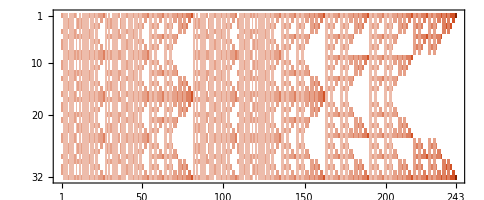

```mathematica
Block[{n=5,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=Append[RotateLeft[σ@@PadLeft[{3,3},n],#]&/@Range[n-1],σ@@ConstantArray[1,n]];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
MatrixPlot[P]]
```

#### GHZ State (Mixed)

##### N=2

```mathematica
Block[{n=2,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=RotateLeft[σ@@PadLeft[{3,3},n],#]&/@Range[n-1];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XX | XY | XZ | YX | YY | YZ | ZX | ZY | ZZ
++ | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1
+- | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 0
-+ | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 0
-- | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1
3.02045 | 0.936426 | 0. | 0.
0.557345 --
0.557345 ++
0.435162 +-
0.435162 -+ | -0.557345 -+
-0.557345 +-
0.435162 ++
0.435162 -- | 0.516128 +-
-0.516128 -+
0.483334 --
-0.483334 ++ | 0.516128 --
-0.516128 ++
0.483334 -+
-0.483334 +-
0.369048 ZZ
0.328596 XX
0.328596 XY
0.328596 ZY
0.328596 ZX
0.328596 YZ
0.328596 YY
0.328596 YX
0.328596 XZ | 0.92941 ZZ
-0.130478 XY
-0.130478 XX
-0.130478 ZY
-0.130478 ZX
-0.130478 YZ
-0.130478 YY
-0.130478 YX
-0.130478 XZ | 0.750925 XX
-0.659328 XY
-0.0152662 YX
-0.0152662 ZY
-0.0152662 ZX
-0.0152662 YZ
-0.0152662 YY
-0.0152662 XZ | 0.663541 XY
0.557774 XX
-0.203552 YX
-0.203552 ZY
-0.203552 ZX
-0.203552 YZ
-0.203552 YY
-0.203552 XZ

##### N=3

```mathematica
Block[{n=3,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=RotateLeft[σ@@PadLeft[{3,3},n],#]&/@Range[n-1];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XXX | XXY | XXZ | XYX | XYY | XYZ | XZX | XZY | XZZ | YXX | YXY | YXZ | YYX | YYY | YYZ | YZX | YZY | YZZ | ZXX | ZXY | ZXZ | ZYX | ZYY | ZYZ | ZZX | ZZY | ZZZ
+++ | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/2 | 1/2 | 1
++- | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/2 | 1/2 | 0
+-+ | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0
+-- | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0
-++ | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0
-+- | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0
--+ | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/2 | 1/2 | 0
--- | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/2 | 1/2 | 1
3.7527 | 1.38464 | 1. | 1. | 0. | 0. | 0. | 0.
0.47901 ---
0.47901 +++
0.300305 ++-
0.300305 +-+
0.300305 --+
0.300305 +--
0.300305 -++
0.300305 -+- | 0.520144 +++
0.520144 ---
-0.276556 --+
-0.276556 +-+
-0.276556 -++
-0.276556 +--
-0.276556 -+-
-0.276556 ++- | 0.550928 ++-
0.550928 --+
-0.424992 +-+
-0.424992 -+-
-0.125936 -++
-0.125936 +-- | 0.563448 -++
0.563448 +--
-0.390788 +-+
-0.390788 -+-
-0.17266 ++-
-0.17266 --+ | 0.611825 ---
-0.611825 +++
0.309592 +--
-0.309592 -++
0.16916 +-+
-0.16916 -+-
0.034762 ++-
-0.034762 --+ | 0.577602 -++
-0.577602 +--
0.338559 ---
-0.338559 +++
0.187466 --+
-0.187466 ++-
0.128881 -+-
-0.128881 +-+ | 0.659886 +-+
-0.659886 -+-
0.222665 -++
-0.222665 +--
0.0964762 ++-
-0.0964762 --+
0.0752577 +++
-0.0752577 --- | 0.674048 --+
-0.674048 ++-
0.144739 +--
-0.144739 -++
0.139017 +-+
-0.139017 -+-
0.0733785 +++
-0.0733785 ---
0.255288 ZZZ
0.207668 ZZY
0.207668 ZZX
0.207668 ZYZ
0.207668 ZXZ
0.207668 YZZ
0.207668 XZZ
0.183858 XXX
0.183858 ZYY
0.183858 ZYX
0.183858 ZXY
0.183858 ZXX
0.183858 YZY
0.183858 YZX
0.183858 YYZ
0.183858 YYY
0.183858 YYX
0.183858 YXZ
0.183858 YXY
0.183858 YXX
0.183858 XZY
0.183858 XZX
0.183858 XYZ
0.183858 XYY
0.183858 XYX
0.183858 XXY
0.183858 XXZ | 0.751304 ZZZ
0.175921 ZZY
0.175921 ZZX
0.175921 YZZ
0.175921 XZZ
0.175921 ZYZ
0.175921 ZXZ
-0.111771 XXX
-0.111771 XYX
-0.111771 ZYY
-0.111771 ZYX
-0.111771 ZXY
-0.111771 ZXX
-0.111771 YZY
-0.111771 YZX
-0.111771 YYZ
-0.111771 YYY
-0.111771 YYX
-0.111771 YXZ
-0.111771 YXY
-0.111771 YXX
-0.111771 XZY
-0.111771 XZX
-0.111771 XYZ
-0.111771 XYY
-0.111771 XXZ
-0.111771 XXY | 0.550928 ZZY
0.550928 ZZX
-0.424992 ZYZ
-0.424992 ZXZ
-0.125936 YZZ
-0.125936 XZZ | 0.563448 YZZ
0.563448 XZZ
-0.390788 ZYZ
-0.390788 ZXZ
-0.17266 ZZY
-0.17266 ZZX | 0.925361 XXX
-0.33938 XYX
-0.1267 XXY
0.0389086 ZZZ
-0.0231318 ZYY
-0.0231318 ZYX
-0.0231318 ZXY
-0.0231318 ZXX
-0.0231318 YZY
-0.0231318 YZX
-0.0231318 YYZ
-0.0231318 YYY
-0.0231318 YYX
-0.0231318 YXZ
-0.0231318 YXY
-0.0231318 YXX
-0.0231318 XZY
-0.0231318 XYY
-0.0231318 XZX
-0.0231318 XYZ
-0.0194543 YZZ
-0.0194543 XZZ
-0.0194543 ZZY
-0.0194543 ZZX
-0.0194543 ZYZ
-0.0194543 ZXZ
-0.0113555 XXZ | 0.844613 XYX
0.311173 XXX
0.272243 XXY
-0.0834867 XZX
-0.0834867 XZY
-0.0834867 ZYY
-0.0834867 ZYX
-0.0834867 ZXY
-0.0834867 ZXX
-0.0834867 YZY
-0.0834867 YZX
-0.0834867 YYZ
-0.0834867 YYY
-0.0834867 YYX
-0.0834867 YXZ
-0.0834867 YXY
-0.0834867 YXX
-0.0834867 XYZ
-0.0834867 XYY
-0.058895 XXZ
0.0166732 ZZZ
-0.0083366 ZZY
-0.0083366 ZZX
-0.0083366 ZYZ
-0.0083366 ZXZ
-0.0083366 YZZ
-0.0083366 XZZ | 0.751839 XXZ
0.536253 XXY
-0.191451 XYX
0.176067 ZZZ
-0.0880334 YZZ
-0.0880334 XZZ
-0.0880334 ZZY
-0.0880334 ZZX
-0.0880334 ZYZ
-0.0880334 ZXZ
-0.0450265 XZX
-0.0450265 XYZ
-0.0450265 XZY
-0.0450265 ZYY
-0.0450265 ZYX
-0.0450265 ZXY
-0.0450265 ZXX
-0.0450265 YZY
-0.0450265 YZX
-0.0450265 YYZ
-0.0450265 YYY
-0.0450265 YYX
-0.0450265 YXZ
-0.0450265 YXY
-0.0450265 YXX
-0.0450265 XYY
-0.0240828 XXX | 0.758925 XXY
-0.573017 XXZ
-0.285363 XYX
-0.0750913 ZZZ
0.0375456 ZYZ
0.0375456 ZXZ
0.0375456 YZZ
0.0375456 XZZ
0.0375456 ZZY
0.0375456 ZZX
-0.00310021 XZX
-0.00310021 XYY
-0.00310021 XYZ
-0.00310021 XZY
-0.00310021 ZYY
-0.00310021 ZYX
-0.00310021 ZXY
-0.00310021 ZXX
-0.00310021 YZY
-0.00310021 YZX
-0.00310021 YYZ
-0.00310021 YYY
-0.00310021 YYX
-0.00310021 YXZ
-0.00310021 YXY
-0.00310021 YXX
-0.00112495 XXX

##### N=4

```mathematica
Block[{n=4,stb,ρ,as,bs,tas,tbs,P,U,S,V,L,R},
stb=RotateLeft[σ@@PadLeft[{3,3},n],#]&/@Range[n-1];
ρ=Dot@@(Represent[(σ0[#]+#)/2]&/@stb);
as=Tuples[Range[3],n];tas=Row/@(as/.{1->Style["X",Red],2->Style["Y",Green],3->Style["Z",Blue]});
bs=Tuples[{1,-1},n];tbs=Row/@(bs/.{1->Style["+",Red],-1->Style["-",Blue]});
P=Table[Tr[ρ.(KroneckerProduct@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}];
{U,S,V}=SingularValueDecomposition@N@P;
S=Diagonal@S;{U,V}=Transpose/@{U,V};V=V[[;;Length@S]];
Column[{TableForm[P,TableHeadings->{tbs,tas}],Grid[Thread[Function[{s,u,v},Block[{sgn},sgn=Sign@First@MaximalBy[Join[u,v],Abs];
Prepend[Column[Reverse@SortBy[MonomialList[Chop[sgn#]],Abs[#]+0.0000001Sign[#]&@First@#&],Alignment->Right]&/@{u.tbs,v.tas},s]]]@@@Thread@{S,U,V}],Frame->All]}]]
```

| XXXX | XXXY | XXXZ | XXYX | XXYY | XXYZ | XXZX | XXZY | XXZZ | XYXX | XYXY | XYXZ | XYYX | XYYY | XYYZ | XYZX | XYZY | XYZZ | XZXX | XZXY | XZXZ | XZYX | XZYY | XZYZ | XZZX | XZZY | XZZZ | YXXX | YXXY | YXXZ | YXYX | YXYY | YXYZ | YXZX | YXZY | YXZZ | YYXX | YYXY | YYXZ | YYYX | YYYY | YYYZ | YYZX | YYZY | YYZZ | YZXX | YZXY | YZXZ | YZYX | YZYY | YZYZ | YZZX | YZZY | YZZZ | ZXXX | ZXXY | ZXXZ | ZXYX | ZXYY | ZXYZ | ZXZX | ZXZY | ZXZZ | ZYXX | ZYXY | ZYXZ | ZYYX | ZYYY | ZYYZ | ZYZX | ZYZY | ZYZZ | ZZXX | ZZXY | ZZXZ | ZZYX | ZZYY | ZZYZ | ZZZX | ZZZY | ZZZZ
++++ | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/2 | 1/2 | 1
+++- | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/2 | 1/2 | 0
++-+ | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0
++-- | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0
+-++ | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+-+- | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+--+ | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
+--- | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+++ | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-++- | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+-+ | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-+-- | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
--++ | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 0 | 0 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 0 | 0 | 0
--+- | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 0 | 0 | 0 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 0 | 0 | 0
---+ | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/8 | 1/8 | 0 | 1/8 | 1/8 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/4 | 1/4 | 0 | 1/2 | 1/2 | 0
---- | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/8 | 1/8 | 1/4 | 1/8 | 1/8 | 1/4 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/4 | 1/4 | 1/2 | 1/2 | 1/2 | 1
4.70003 | 1.93397 | 1.41421 | 1.41421 | 1.41421 | 1. | 1. | 0.411636 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.435501 ++++
0.435501 ----
0.232222 ---+
0.232222 +-++
0.232222 +---
0.232222 -+++
0.232222 -+--
0.232222 --+-
0.232222 ++-+
0.232222 +++-
0.177605 ++--
0.177605 +-+-
0.177605 +--+
0.177605 -++-
0.177605 -+-+
0.177605 --++ | 0.531242 ++++
0.531242 ----
-0.23486 ++--
-0.23486 --++
-0.23486 +--+
-0.23486 -++-
-0.23486 +-+-
-0.23486 -+-+
-0.114351 +-++
-0.114351 -+++
-0.114351 +---
-0.114351 -+--
-0.114351 --+-
-0.114351 ---+
-0.114351 ++-+
-0.114351 +++- | 0.506542 +---
0.506542 -+++
-0.395145 --+-
-0.395145 ++-+
-0.257033 ---+
-0.257033 +++-
0.145635 -+--
0.145635 +-++ | 0.547874 +-++
0.547874 -+--
-0.339774 -+++
-0.339774 +---
-0.281159 ++-+
-0.281159 --+-
0.0730581 ---+
0.0730581 +++- | 0.550996 ---+
0.550996 +++-
-0.373912 ++-+
-0.373912 --+-
-0.231569 +-++
-0.231569 -+--
0.0544852 +---
0.0544852 -+++ | 0.5727 +--+
0.5727 -++-
-0.349684 +-+-
-0.349684 -+-+
-0.223016 --++
-0.223016 ++-- | 0.532538 --++
0.532538 ++--
-0.459407 -+-+
-0.459407 +-+-
-0.0731314 +--+
-0.0731314 -++- | 0.282779 ++--
0.282779 +-+-
0.282779 -+-+
0.282779 +--+
0.282779 -++-
0.282779 --++
-0.240825 ++-+
-0.240825 --+-
-0.240825 +-++
-0.240825 -+--
-0.240825 +---
-0.240825 -+++
-0.240825 +++-
-0.240825 ---+
0.167693 ++++
0.167693 ---- | 0.693676 ----
-0.693676 ++++
0.0849833 +++-
-0.0849833 ---+
0.0647208 -+--
-0.0647208 +-++
0.062277 ++-+
-0.062277 --+-
0.0475828 --++
-0.0475828 ++--
0.0229971 +-+-
-0.0229971 -+-+
0.0215259 -+++
-0.0215259 +---
0.0163847 -++-
-0.0163847 +--+ | 0.61902 +-++
-0.61902 -+--
0.302103 +--+
-0.302103 -++-
0.117916 ++--
-0.117916 --++
0.0799809 ----
-0.0799809 ++++
0.0583753 -+-+
-0.0583753 +-+-
0.0389938 --+-
-0.0389938 ++-+
0.0155318 +---
-0.0155318 -+++
0.00884244 ---+
-0.00884244 +++- | 0.611462 ++-+
-0.611462 --+-
0.246094 --++
-0.246094 ++--
0.162253 ---+
-0.162253 +++-
0.128658 -+-+
-0.128658 +-+-
0.106508 -+++
-0.106508 +---
0.0931097 +-++
-0.0931097 -+--
0.0429265 ++++
-0.0429265 ----
0.0285755 -++-
-0.0285755 +--+ | 0.646684 ++--
-0.646684 --++
0.256444 ++-+
-0.256444 --+-
0.100062 -+--
-0.100062 +-++
0.0558417 -+-+
-0.0558417 +-+-
0.0458952 -+++
-0.0458952 +---
0.0255896 -++-
-0.0255896 +--+
0.0113234 ----
-0.0113234 ++++
0.00407888 +++-
-0.00407888 ---+ | 0.546881 ---+
-0.546881 +++-
0.380827 +--+
-0.380827 -++-
0.210914 -+--
-0.210914 +-++
0.0786072 --+-
-0.0786072 ++-+
0.0653185 ----
-0.0653185 ++++
0.025273 +---
-0.025273 -+++
0.0178752 ++--
-0.0178752 --++
0.00196353 +-+-
-0.00196353 -+-+ | 0.650585 -+-+
-0.650585 +-+-
0.211333 -+++
-0.211333 +---
0.158431 --+-
-0.158431 ++-+
0.0670864 -+--
-0.0670864 +-++
0.0423874 +++-
-0.0423874 ---+
0.0190351 --++
-0.0190351 ++--
0.0166282 ----
-0.0166282 ++++
0.00643379 +--+
-0.00643379 -++- | 0.482877 +--+
-0.482877 -++-
0.371825 +++-
-0.371825 ---+
0.251933 -+++
-0.251933 +---
0.186809 -+--
-0.186809 +-++
0.105765 +-+-
-0.105765 -+-+
0.0990443 ++-+
-0.0990443 --+-
0.0758291 ++++
-0.0758291 ----
0.0588381 --++
-0.0588381 ++-- | 0.614064 -+++
-0.614064 +---
0.204796 +-+-
-0.204796 -+-+
0.169567 -++-
-0.169567 +--+
0.16501 ---+
-0.16501 +++-
0.117738 --+-
-0.117738 ++-+
0.100305 +-++
-0.100305 -+--
0.0304279 ++--
-0.0304279 --++
0.0123816 ----
-0.0123816 ++++
0.185318 ZZZZ
0.142068 YZZZ
0.142068 XZZZ
0.142068 ZYZZ
0.142068 ZXZZ
0.142068 ZZZY
0.142068 ZZZX
0.142068 ZZYZ
0.142068 ZZXZ
0.114632 YZYZ
0.114632 YZXZ
0.114632 XZYZ
0.114632 XZXZ
0.114632 YZZY
0.114632 YZZX
0.114632 XZZY
0.114632 XZZX
0.114632 ZZYY
0.114632 ZZYX
0.114632 ZZXY
0.114632 ZZXX
0.114632 ZYZY
0.114632 ZYZX
0.114632 ZXZY
0.114632 ZXZX
0.114632 YYZZ
0.114632 YXZZ
0.114632 XYZZ
0.114632 XXZZ
0.114632 ZYYZ
0.114632 ZYXZ
0.114632 ZXYZ
0.114632 ZXXZ
0.100914 XXXX
0.100914 XXZY
0.100914 ZYYY
0.100914 ZYYX
0.100914 ZYXY
0.100914 ZYXX
0.100914 ZXYY
0.100914 ZXYX
0.100914 ZXXY
0.100914 ZXXX
0.100914 YZYY
0.100914 YZYX
0.100914 YZXY
0.100914 YZXX
0.100914 YYZY
0.100914 YYZX
0.100914 YYYZ
0.100914 YYYY
0.100914 YYYX
0.100914 YYXZ
0.100914 YYXY
0.100914 YYXX
0.100914 YXZY
0.100914 YXZX
0.100914 YXYZ
0.100914 YXYY
0.100914 YXYX
0.100914 YXXZ
0.100914 YXXY
0.100914 YXXX
0.100914 XZYY
0.100914 XZYX
0.100914 XZXY
0.100914 XZXX
0.100914 XYZY
0.100914 XYZX
0.100914 XYYZ
0.100914 XYYY
0.100914 XYYX
0.100914 XYXZ
0.100914 XYXY
0.100914 XYXX
0.100914 XXZX
0.100914 XXXY
0.100914 XXYZ
0.100914 XXYY
0.100914 XXYX
0.100914 XXXZ | 0.549379 ZZZZ
0.215562 ZZZY
0.215562 ZZZX
0.215562 ZYZZ
0.215562 ZXZZ
0.215562 ZZYZ
0.215562 ZZXZ
0.215562 YZZZ
0.215562 XZZZ
-0.0815345 XXXX
-0.0815345 XXZY
-0.0815345 ZYYY
-0.0815345 ZYYX
-0.0815345 ZYXY
-0.0815345 ZYXX
-0.0815345 ZXYY
-0.0815345 ZXYX
-0.0815345 ZXXY
-0.0815345 ZXXX
-0.0815345 YZYY
-0.0815345 YZYX
-0.0815345 YZXY
-0.0815345 YZXX
-0.0815345 YYZY
-0.0815345 YYZX
-0.0815345 YYYZ
-0.0815345 YYYY
-0.0815345 YYYX
-0.0815345 YYXZ
-0.0815345 YYXY
-0.0815345 YYXX
-0.0815345 YXZY
-0.0815345 YXZX
-0.0815345 YXYZ
-0.0815345 YXYY
-0.0815345 YXYX
-0.0815345 YXXZ
-0.0815345 YXXY
-0.0815345 YXXX
-0.0815345 XZYY
-0.0815345 XZYX
-0.0815345 XZXY
-0.0815345 XZXX
-0.0815345 XYZY
-0.0815345 XYZX
-0.0815345 XYYZ
-0.0815345 XYYY
-0.0815345 XYYX
-0.0815345 XYXZ
-0.0815345 XYXY
-0.0815345 XYXX
-0.0815345 XXYZ
-0.0815345 XXXY
-0.0815345 XXZX
-0.0815345 XXYY
-0.0815345 XXYX
-0.0815345 XXXZ
0.0174977 ZYZY
0.0174977 ZYZX
0.0174977 ZXZY
0.0174977 ZXZX
0.0174977 ZZYY
0.0174977 ZZYX
0.0174977 ZZXY
0.0174977 ZZXX
0.0174977 YYZZ
0.0174977 YXZZ
0.0174977 XYZZ
0.0174977 XXZZ
0.0174977 ZYYZ
0.0174977 ZYXZ
0.0174977 ZXYZ
0.0174977 ZXXZ
0.0174977 YZZY
0.0174977 YZZX
0.0174977 XZZY
0.0174977 XZZX
0.0174977 YZYZ
0.0174977 YZXZ
0.0174977 XZYZ
0.0174977 XZXZ | 0.35818 YZZZ
0.35818 XZZZ
-0.27941 ZZYZ
-0.27941 ZZXZ
0.23058 YYZZ
0.23058 YXZZ
0.23058 XYZZ
0.23058 XXZZ
-0.23058 ZZYY
-0.23058 ZZYX
-0.23058 ZZXY
-0.23058 ZZXX
-0.181749 ZZZY
-0.181749 ZZZX
0.10298 ZYZZ
0.10298 ZXZZ
0.088215 YZZY
0.088215 YZZX
0.088215 XZZY
0.088215 XZZX
-0.088215 ZYYZ
-0.088215 ZYXZ
-0.088215 ZXYZ
-0.088215 ZXXZ
0.039385 YZYZ
0.039385 YZXZ
0.039385 XZYZ
0.039385 XZXZ
-0.039385 ZYZY
-0.039385 ZYZX
-0.039385 ZXZY
-0.039385 ZXZX | 0.387406 ZYZZ
0.387406 ZXZZ
-0.240256 YZZZ
-0.240256 XZZZ
0.219533 ZYZY
0.219533 ZYZX
0.219533 ZXZY
0.219533 ZXZX
-0.219533 YZYZ
-0.219533 YZXZ
-0.219533 XZYZ
-0.219533 XZXZ
-0.198809 ZZYZ
-0.198809 ZZXZ
0.0942982 ZYYZ
0.0942982 ZYXZ
0.0942982 ZXYZ
0.0942982 ZXXZ
-0.0942982 YZZY
-0.0942982 YZZX
-0.0942982 XZZY
-0.0942982 XZZX
0.0735746 YYZZ
0.0735746 YXZZ
0.0735746 XYZZ
0.0735746 XXZZ
-0.0735746 ZZYY
-0.0735746 ZZYX
-0.0735746 ZZXY
-0.0735746 ZZXX
0.0516599 ZZZY
0.0516599 ZZZX | 0.389613 ZZZY
0.389613 ZZZX
-0.264396 ZZYZ
-0.264396 ZZXZ
0.21407 YZZY
0.21407 YZZX
0.21407 XZZY
0.21407 XZZX
-0.21407 ZYYZ
-0.21407 ZYXZ
-0.21407 ZXYZ
-0.21407 ZXXZ
-0.163744 ZYZZ
-0.163744 ZXZZ
0.112935 ZYZY
0.112935 ZYZX
0.112935 ZXZY
0.112935 ZXZX
-0.112935 YZYZ
-0.112935 YZXZ
-0.112935 XZYZ
-0.112935 XZXZ
0.0626086 ZZYY
0.0626086 ZZYX
0.0626086 ZZXY
0.0626086 ZZXX
-0.0626086 YYZZ
-0.0626086 YXZZ
-0.0626086 XYZZ
-0.0626086 XXZZ
0.0385268 YZZZ
0.0385268 XZZZ | 0.28635 YZZY
0.28635 YZZX
0.28635 XZZY
0.28635 XZZX
0.28635 ZYYZ
0.28635 ZYXZ
0.28635 ZXYZ
0.28635 ZXXZ
-0.174842 ZYZY
-0.174842 ZYZX
-0.174842 ZXZY
-0.174842 ZXZX
-0.174842 YZYZ
-0.174842 YZXZ
-0.174842 XZYZ
-0.174842 XZXZ
-0.111508 ZZYY
-0.111508 ZZYX
-0.111508 ZZXY
-0.111508 ZZXX
-0.111508 YYZZ
-0.111508 YXZZ
-0.111508 XYZZ
-0.111508 XXZZ | 0.266269 ZZYY
0.266269 ZZYX
0.266269 ZZXY
0.266269 ZZXX
0.266269 YYZZ
0.266269 YXZZ
0.266269 XYZZ
0.266269 XXZZ
-0.229703 ZYZY
-0.229703 ZYZX
-0.229703 ZXZY
-0.229703 ZXZX
-0.229703 YZYZ
-0.229703 YZXZ
-0.229703 XZYZ
-0.229703 XZXZ
-0.0365657 ZYYZ
-0.0365657 ZYXZ
-0.0365657 ZXYZ
-0.0365657 ZXXZ
-0.0365657 YZZY
-0.0365657 YZZX
-0.0365657 XZZY
-0.0365657 XZZX | 0.814763 ZZZZ
-0.177663 ZZYZ
-0.177663 ZZXZ
-0.177663 ZYZZ
-0.177663 ZXZZ
-0.177663 YZZZ
-0.177663 XZZZ
-0.177663 ZZZY
-0.177663 ZZZX
-0.0378715 ZYYZ
-0.0378715 ZYXZ
-0.0378715 ZXYZ
-0.0378715 ZXXZ
-0.0378715 YZYZ
-0.0378715 YZXZ
-0.0378715 XZYZ
-0.0378715 XZXZ
-0.0378715 YYZZ
-0.0378715 YXZZ
-0.0378715 XYZZ
-0.0378715 XXZZ
-0.0378715 ZZYY
-0.0378715 ZZYX
-0.0378715 ZZXY
-0.0378715 ZZXX
-0.0378715 ZYZY
-0.0378715 ZYZX
-0.0378715 ZXZY
-0.0378715 ZXZX
-0.0378715 YZZY
-0.0378715 YZZX
-0.0378715 XZZY
-0.0378715 XZZX
0.0320242 XXYZ
0.0320242 XXYY
0.0320242 ZYYY
0.0320242 ZYYX
0.0320242 ZYXY
0.0320242 ZYXX
0.0320242 ZXYY
0.0320242 ZXYX
0.0320242 ZXXY
0.0320242 ZXXX
0.0320242 YZYY
0.0320242 YZYX
0.0320242 YZXY
0.0320242 YZXX
0.0320242 YYZY
0.0320242 YYZX
0.0320242 YYYZ
0.0320242 YYYY
0.0320242 YYYX
0.0320242 YYXZ
0.0320242 YYXY
0.0320242 YYXX
0.0320242 YXZY
0.0320242 YXZX
0.0320242 YXYZ
0.0320242 YXYY
0.0320242 YXYX
0.0320242 YXXZ
0.0320242 YXXY
0.0320242 YXXX
0.0320242 XZYY
0.0320242 XZYX
0.0320242 XZXY
0.0320242 XZXX
0.0320242 XYZY
0.0320242 XYZX
0.0320242 XYYZ
0.0320242 XYYY
0.0320242 XYYX
0.0320242 XYXZ
0.0320242 XYXY
0.0320242 XYXX
0.0320242 XXYX
0.0320242 XXXY
0.0320242 XXXZ
0.0320242 XXZX
0.0320242 XXZY
0.0320242 XXXX | 0.98777 XXXX
-0.0824609 XXYY
-0.0462012 XXYX
-0.0443032 XXXY
-0.0216357 XXZY
-0.0179685 XXZX
-0.0161031 XYYY
-0.0161031 XYXY
-0.0161031 XYXZ
-0.0161031 XYZX
-0.0161031 ZYYY
-0.0161031 ZYYX
-0.0161031 ZYXY
-0.0161031 ZYXX
-0.0161031 ZXYY
-0.0161031 ZXYX
-0.0161031 ZXXY
-0.0161031 ZXXX
-0.0161031 YZYY
-0.0161031 YZYX
-0.0161031 YZXY
-0.0161031 YZXX
-0.0161031 YYZY
-0.0161031 YYZX
-0.0161031 YYYZ
-0.0161031 YYYY
-0.0161031 YYYX
-0.0161031 YYXZ
-0.0161031 YYXY
-0.0161031 YYXX
-0.0161031 YXZY
-0.0161031 YXZX
-0.0161031 YXYZ
-0.0161031 YXYY
-0.0161031 YXYX
-0.0161031 YXXZ
-0.0161031 YXXY
-0.0161031 YXXX
-0.0161031 XZYY
-0.0161031 XZYX
-0.0161031 XZXY
-0.0161031 XZXX
-0.0161031 XYZY
-0.0161031 XYXX
-0.0161031 XYYZ
-0.0161031 XYYX
-0.0149859 XXYZ
0.00882995 ZZZY
0.00882995 ZZZX
0.00861082 XXXZ
-0.00829548 ZZYY
-0.00829548 ZZYX
-0.00829548 ZZXY
-0.00829548 ZZXX
-0.00823734 ZYZY
-0.00823734 ZYZX
-0.00823734 ZXZY
-0.00823734 ZXZX
-0.00788508 YZZY
-0.00788508 YZZX
-0.00788508 XZZY
-0.00788508 XZZX
0.00776101 ZZYZ
0.00776101 ZZXZ
-0.00770287 ZYYZ
-0.00770287 ZYXZ
-0.00770287 ZXYZ
-0.00770287 ZXXZ
0.00764474 ZYZZ
0.00764474 ZXZZ
-0.00735061 YZYZ
-0.00735061 YZXZ
-0.00735061 XZYZ
-0.00735061 XZXZ
-0.00729247 YYZZ
-0.00729247 YXZZ
-0.00729247 XYZZ
-0.00729247 XXZZ
0.0069402 YZZZ
0.0069402 XZZZ | 0.94568 XXYY
0.13403 XXZY
0.132914 XXYX
-0.122201 XXYZ
0.113995 XXXY
0.0709338 XXXX
-0.0282975 XYYY
-0.0282975 XYZX
-0.0282975 ZYYY
-0.0282975 ZYYX
-0.0282975 ZYXY
-0.0282975 ZYXX
-0.0282975 ZXYY
-0.0282975 ZXYX
-0.0282975 ZXXY
-0.0282975 ZXXX
-0.0282975 YZYY
-0.0282975 YZYX
-0.0282975 YZXY
-0.0282975 YZXX
-0.0282975 YYZY
-0.0282975 YYZX
-0.0282975 YYYZ
-0.0282975 YYYY
-0.0282975 YYYX
-0.0282975 YYXZ
-0.0282975 YYXY
-0.0282975 YYXX
-0.0282975 YXZY
-0.0282975 YXZX
-0.0282975 YXYZ
-0.0282975 YXYY
-0.0282975 YXYX
-0.0282975 YXXZ
-0.0282975 YXXY
-0.0282975 YXXX
-0.0282975 XZYY
-0.0282975 XZYX
-0.0282975 XZXY
-0.0282975 XZXX
-0.0282975 XYZY
-0.0282975 XYYZ
-0.0282975 XYYX
-0.0282975 XYXY
-0.0282975 XYXX
-0.0282975 XYXZ
0.0279632 XXZX
0.0212604 YZZZ
0.0212604 XZZZ
-0.0168679 XXZZ
-0.0168679 YYZZ
-0.0168679 YXZZ
-0.0168679 XYZZ
-0.0127357 YZYZ
-0.0127357 YZXZ
-0.0127357 XZYZ
-0.0127357 XZXZ
0.0124754 ZYZZ
0.0124754 ZXZZ
-0.0122846 YZZY
-0.0122846 YZZX
-0.0122846 XZZY
-0.0122846 XZZX
-0.00834315 ZYYZ
-0.00834315 ZYXZ
-0.00834315 ZXYZ
-0.00834315 ZXXZ
-0.00789213 ZYZY
-0.00789213 ZYZX
-0.00789213 ZXZY
-0.00789213 ZXZX
-0.00639397 XXXZ
0.00421092 ZZYZ
0.00421092 ZZXZ
-0.00375989 ZZYY
-0.00375989 ZZYX
-0.00375989 ZZXY
-0.00375989 ZZXX
0.00330887 ZZZY
0.00330887 ZZZX | 0.884851 XXXZ
-0.352366 XXYX
-0.198668 XXZY
0.184415 XXXY
0.0790901 XXZX
0.0425256 XXYY
-0.0253635 XXXX
-0.0155794 XXYZ
-0.0144867 XYYZ
-0.0144867 XYZX
-0.0144867 ZYYY
-0.0144867 ZYYX
-0.0144867 ZYXY
-0.0144867 ZYXX
-0.0144867 ZXYY
-0.0144867 ZXYX
-0.0144867 ZXXY
-0.0144867 ZXXX
-0.0144867 YZYY
-0.0144867 YZYX
-0.0144867 YZXY
-0.0144867 YZXX
-0.0144867 YYZY
-0.0144867 YYZX
-0.0144867 YYYZ
-0.0144867 YYYY
-0.0144867 YYYX
-0.0144867 YYXZ
-0.0144867 YYXY
-0.0144867 YYXX
-0.0144867 YXZY
-0.0144867 YXZX
-0.0144867 YXYZ
-0.0144867 YXYY
-0.0144867 YXYX
-0.0144867 YXXZ
-0.0144867 YXXY
-0.0144867 YXXX
-0.0144867 XZYY
-0.0144867 XZYX
-0.0144867 XZXY
-0.0144867 XZXX
-0.0144867 XYZY
-0.0144867 XYYY
-0.0144867 XYYX
-0.0144867 XYXY
-0.0144867 XYXZ
-0.0144867 XYXX
0.0142483 ZZYZ
0.0142483 ZZXZ
-0.0123803 YZZZ
-0.0123803 XZZZ
-0.012156 ZZYY
-0.012156 ZZYX
-0.012156 ZZXY
-0.012156 ZZXX
0.0100637 ZZZY
0.0100637 ZZZX
0.00972654 XXZZ
0.00972654 YYZZ
0.00972654 YXZZ
0.00972654 XYZZ
-0.00707275 ZYZZ
-0.00707275 ZXZZ
-0.00358779 ZYYZ
-0.00358779 ZYXZ
-0.00358779 ZXYZ
-0.00358779 ZXXZ
-0.00149549 ZYZY
-0.00149549 ZYZX
-0.00149549 ZXZY
-0.00149549 ZXZX
0.0011583 YZZY
0.0011583 YZZX
0.0011583 XZZY
0.0011583 XZZX
-0.000934 YZYZ
-0.000934 YZXZ
-0.000934 XZYZ
-0.000934 XZXZ | 0.898971 XXYX
0.368514 XXXZ
-0.145382 XXYY
-0.0709904 XXXY
0.0315251 YZZZ
0.0315251 XZZZ
-0.0312881 XXZZ
-0.0312881 YYZZ
-0.0312881 YXZZ
-0.0312881 XYZZ
0.0310512 ZYZZ
0.0310512 ZXZZ
-0.023124 YZYZ
-0.023124 YZXZ
-0.023124 XZYZ
-0.023124 XZXZ
-0.0228871 ZYYZ
-0.0228871 ZYXZ
-0.0228871 ZXYZ
-0.0228871 ZXXZ
-0.0196148 XYXX
-0.0196148 XYXZ
-0.0196148 XYYX
-0.0196148 XYZX
-0.0196148 XYYY
-0.0196148 ZYYY
-0.0196148 ZYYX
-0.0196148 ZYXY
-0.0196148 ZYXX
-0.0196148 ZXYY
-0.0196148 ZXYX
-0.0196148 ZXXY
-0.0196148 ZXXX
-0.0196148 YZYY
-0.0196148 YZYX
-0.0196148 YZXY
-0.0196148 YZXX
-0.0196148 YYZY
-0.0196148 YYZX
-0.0196148 YYYZ
-0.0196148 YYYY
-0.0196148 YYYX
-0.0196148 YYXZ
-0.0196148 YYXY
-0.0196148 YYXX
-0.0196148 YXZY
-0.0196148 YXZX
-0.0196148 YXYZ
-0.0196148 YXYY
-0.0196148 YXYX
-0.0196148 YXXZ
-0.0196148 YXXY
-0.0196148 YXXX
-0.0196148 XZYY
-0.0196148 XZYX
-0.0196148 XZXY
-0.0196148 XZXX
-0.0196148 XYZY
-0.0196148 XYYZ
-0.0196148 XYXY
0.0154002 XXYZ
0.014723 ZZYZ
0.014723 ZZXZ
-0.0139165 YZZY
-0.0139165 YZZX
-0.0139165 XZZY
-0.0139165 XZZX
-0.0136796 ZYZY
-0.0136796 ZYZX
-0.0136796 ZXZY
-0.0136796 ZXZX
0.00656532 XXXX
0.00566643 XXZX
-0.00551544 ZZYY
-0.00551544 ZZYX
-0.00551544 ZZXY
-0.00551544 ZZXX
-0.0036921 ZZZY
-0.0036921 ZZZX
0.000277451 XXZY | 0.848408 XXXY
-0.410683 XXZY
-0.231517 XXXZ
0.146538 XXZX
0.141372 XXYX
-0.0829797 XXYY
0.0261587 XXXX
-0.0215852 YZZZ
-0.0215852 XZZZ
0.015512 YYZZ
0.015512 YXZZ
0.015512 XYZZ
0.015512 XXZZ
0.0150777 ZZYZ
0.0150777 ZZXZ
-0.013269 ZZYY
-0.013269 ZZYX
-0.013269 ZZXY
-0.013269 ZZXX
0.0114602 ZZZY
0.0114602 ZZZX
-0.0114392 XYXX
-0.0114392 XYYZ
-0.0114392 XYYX
-0.0114392 XYYY
-0.0114392 XYZX
-0.0114392 ZYYY
-0.0114392 ZYYX
-0.0114392 ZYXY
-0.0114392 ZYXX
-0.0114392 ZXYY
-0.0114392 ZXYX
-0.0114392 ZXXY
-0.0114392 ZXXX
-0.0114392 YZYY
-0.0114392 YZYX
-0.0114392 YZXY
-0.0114392 YZXX
-0.0114392 YYZY
-0.0114392 YYZX
-0.0114392 YYYZ
-0.0114392 YYYY
-0.0114392 YYYX
-0.0114392 YYXZ
-0.0114392 YYXY
-0.0114392 YYXX
-0.0114392 YXZY
-0.0114392 YXZX
-0.0114392 YXYZ
-0.0114392 YXYY
-0.0114392 YXYX
-0.0114392 YXXZ
-0.0114392 YXXY
-0.0114392 YXXX
-0.0114392 XZYY
-0.0114392 XZYX
-0.0114392 XZXY
-0.0114392 XZXX
-0.0114392 XYZY
-0.0114392 XYXZ
-0.0114392 XYXY
-0.00943876 ZYZZ
-0.00943876 ZXZZ
0.00506247 YZZY
0.00506247 YZZX
0.00506247 XZZY
0.00506247 XZZX
0.00325373 YZYZ
0.00325373 YZXZ
0.00325373 XZYZ
0.00325373 XZXZ
-0.00281948 ZYYZ
-0.00281948 ZYXZ
-0.00281948 ZXYZ
-0.00281948 ZXXZ
0.00232638 XXYZ
-0.00101074 ZYZY
-0.00101074 ZYZX
-0.00101074 ZXZY
-0.00101074 ZXZX | 0.708204 XXZY
0.40505 XXYZ
0.330253 XXXY
0.154294 ZZYZ
0.154294 ZZXZ
-0.118845 XXYY
-0.111387 YZYZ
-0.111387 YZXZ
-0.111387 XZYZ
-0.111387 XZXZ
0.111031 XXZX
-0.0945172 ZYYZ
-0.0945172 ZYXZ
-0.0945172 ZXYZ
-0.0945172 ZXXZ
-0.0853121 ZZZY
-0.0853121 ZZZX
-0.0767505 XXYX
0.0684807 YZZZ
0.0684807 XZZZ
-0.0516106 XXZZ
-0.0516106 YYZZ
-0.0516106 YXZZ
-0.0516106 XYZZ
0.0487366 XXXZ
0.0347404 ZYZZ
0.0347404 ZXZZ
-0.034491 ZZYY
-0.034491 ZZYX
-0.034491 ZZXY
-0.034491 ZZXX
0.0252858 ZYZY
0.0252858 ZYZX
0.0252858 ZXZY
0.0252858 ZXZX
-0.0180356 XYXX
-0.0180356 XYXZ
-0.0180356 XYYZ
-0.0180356 XYYX
-0.0180356 XYYY
-0.0180356 XYZX
-0.0180356 ZYYY
-0.0180356 ZYYX
-0.0180356 ZYXY
-0.0180356 ZYXX
-0.0180356 ZXYY
-0.0180356 ZXYX
-0.0180356 ZXXY
-0.0180356 ZXXX
-0.0180356 YZYY
-0.0180356 YZYX
-0.0180356 YZXY
-0.0180356 YZXX
-0.0180356 YYZY
-0.0180356 YYZX
-0.0180356 YYYZ
-0.0180356 YYYY
-0.0180356 YYYX
-0.0180356 YYXZ
-0.0180356 YYXY
-0.0180356 YYXX
-0.0180356 YXZY
-0.0180356 YXZX
-0.0180356 YXYZ
-0.0180356 YXYY
-0.0180356 YXYX
-0.0180356 YXXZ
-0.0180356 YXXY
-0.0180356 YXXX
-0.0180356 XZYY
-0.0180356 XZYX
-0.0180356 XZXY
-0.0180356 XZXX
-0.0180356 XYZY
-0.0180356 XYXY
0.00841568 YZZY
0.00841568 YZZX
0.00841568 XZZY
0.00841568 XZZX
0.00255859 XXXX | 0.641687 XXZX
-0.6008 XXYZ
0.313228 XXZY
-0.152716 XXYY
-0.0653098 YZZZ
-0.0653098 XZZZ
0.0649955 YZYZ
0.0649955 YZXZ
0.0649955 XZYZ
0.0649955 XZXZ
-0.0646812 ZZYZ
-0.0646812 ZZXZ
0.0528169 YYZZ
0.0528169 YXZZ
0.0528169 XYZZ
0.0528169 XXZZ
0.0525026 ZYYZ
0.0525026 ZYXZ
0.0525026 ZXYZ
0.0525026 ZXXZ
0.0457124 YZZY
0.0457124 YZZX
0.0457124 XZZY
0.0457124 XZZX
0.0453981 ZZYY
0.0453981 ZZYX
0.0453981 ZZXY
0.0453981 ZZXX
-0.040324 ZYZZ
-0.040324 ZXZZ
0.0332195 ZYZY
0.0332195 ZYZX
0.0332195 ZXZY
0.0332195 ZXZX
-0.026115 ZZZY
-0.026115 ZZZX
-0.024517 XYXZ
-0.024517 XYYY
-0.024517 XYZX
-0.024517 ZYYY
-0.024517 ZYYX
-0.024517 ZYXY
-0.024517 ZYXX
-0.024517 ZXYY
-0.024517 ZXYX
-0.024517 ZXXY
-0.024517 ZXXX
-0.024517 YZYY
-0.024517 YZYX
-0.024517 YZXY
-0.024517 YZXX
-0.024517 YYZY
-0.024517 YYZX
-0.024517 YYYZ
-0.024517 YYYY
-0.024517 YYYX
-0.024517 YYXZ
-0.024517 YYXY
-0.024517 YYXX
-0.024517 YXZY
-0.024517 YXZX
-0.024517 YXYZ
-0.024517 YXYY
-0.024517 YXYX
-0.024517 YXXZ
-0.024517 YXXY
-0.024517 YXXX
-0.024517 XZYY
-0.024517 XZYX
-0.024517 XZXY
-0.024517 XZXX
-0.024517 XYZY
-0.024517 XYYX
-0.024517 XYYZ
-0.024517 XYXX
-0.024517 XYXY
0.00920243 XXXY
-0.00752478 XXXZ
-0.00665747 XXXX
-0.00145983 XXYX | 0.64431 XXZX
0.415434 XXYZ
-0.362669 XXZY
-0.314944 XXXY
0.177628 ZZYZ
0.177628 ZZXZ
0.115645 XXYY
-0.0845537 XXXZ
-0.0810193 ZZZY
-0.0810193 ZZZX
-0.0766984 YZYZ
-0.0766984 YZXZ
-0.0766984 XZYZ
-0.0766984 XZXZ
-0.0757013 ZYYZ
-0.0757013 ZYXZ
-0.0757013 ZXYZ
-0.0757013 ZXXZ
0.0536225 ZYZY
0.0536225 ZYZX
0.0536225 ZXZY
0.0536225 ZXZX
0.0526255 YZZY
0.0526255 YZZX
0.0526255 XZZY
0.0526255 XZZX
-0.0483045 ZZYY
-0.0483045 ZZYX
-0.0483045 ZZXY
-0.0483045 ZZXX
-0.0262257 ZYZZ
-0.0262257 ZXZZ
0.0252287 XXZZ
0.0252287 YYZZ
0.0252287 YXZZ
0.0252287 XYZZ
-0.0242316 YZZZ
-0.0242316 XZZZ
-0.00578298 XYXZ
-0.00578298 XYYX
-0.00578298 XYXX
-0.00578298 XYYZ
-0.00578298 ZYYY
-0.00578298 ZYYX
-0.00578298 ZYXY
-0.00578298 ZYXX
-0.00578298 ZXYY
-0.00578298 ZXYX
-0.00578298 ZXXY
-0.00578298 ZXXX
-0.00578298 YZYY
-0.00578298 YZYX
-0.00578298 YZXY
-0.00578298 YZXX
-0.00578298 YYZY
-0.00578298 YYZX
-0.00578298 YYYZ
-0.00578298 YYYY
-0.00578298 YYYX
-0.00578298 YYXZ
-0.00578298 YYXY
-0.00578298 YYXX
-0.00578298 YXZY
-0.00578298 YXZX
-0.00578298 YXYZ
-0.00578298 YXYY
-0.00578298 YXYX
-0.00578298 YXXZ
-0.00578298 YXXY
-0.00578298 YXXX
-0.00578298 XZYY
-0.00578298 XZYX
-0.00578298 XZXY
-0.00578298 XZXX
-0.00578298 XYZY
-0.00578298 XYXY
-0.00578298 XYZX
-0.00578298 XYYY
0.00265493 XXYX
0.0000490122 XXXX

### Entanglement Feature

#### Marginalization

Given the shadow probability P_ρ(b,S), marginalize over a subsystem Ā

P_ρ(b_A,S_A)=∑_(b_(Ā),S_(Ā)) P_ρ(b,S).

The marginal shadow distribution is the simply given by

P_ρ(b_A,S_A)=Tr(σ_(b_A,S_A)ρ_A)P(S_A),

where

ρ_A=Tr_(Ā)ρ is the reduced density matrix,

σ_(b_A,S_A) is the reduced classical snapshot

σ_(b_A,S_A)=∏_(i∈A) (𝟙+b_i S_i)/2,

P(S_A)=3^(-|A|) is the observable distribution in the subsystem A.

Prove Eq. (DisplayFormulaNumbered).

Starting from Eq. (DisplayFormulaNumbered), plugging in Eq. (DisplayFormulaNumbered)

(P_ρ(b,S))_A=∑_(b_(Ā),S_(Ā)) Tr(σ_(b,S)ρ)P(S)
=3^-N∑_(b_(Ā),S_(Ā)) Tr(∏_(i∈A) (𝟙+b_i S_i)/2∏_(i∈Ā) (𝟙+b_i S_i)/2 ρ)
=3^-N Tr(∏_(i∈A) (𝟙+b_i S_i)/2∏_(i∈Ā) (∑_(b_i,S_i) (𝟙+b_i S_i)/2)ρ).

Now for a single qubit shadow

∑_(b_i=±) ∑_(S_i=X,Y,Z) (𝟙+b_i S_i)/2
=∑_(S_i=X,Y,Z) (𝟙+S_i)/2+(𝟙-S_i)/2
=∑_(S_i=X,Y,Z) 𝟙
=3𝟙.

Therefore the factor 3 will accumulate over |Ā| and the identity operator contracts the density matrix ρ in the Ā region, leading to the reduced density matrix

ρ_A=Tr_(Ā)ρ,

such that

P_ρ(b_A,S_A)=3^-N×3^(|Ā|)Tr(∏_(i∈A) (𝟙+b_i S_i)/2 ρ_A)
=3^(|A|)Tr(∏_(i∈A) (𝟙+b_i S_i)/2 ρ_A)
=Tr(σ_(b_A,S_A)ρ_A)P(S_A).

#### Rényi Partition Function (Pauli)

The Rényi partition function for a shadow distribution P_ρ(b,S) is defined as

Z_(ρ,sh)^(n)=∑_(b,S) (P_ρ(b,S))^n.

The definition applies to reduced density matrix as well.

Z_(ρ,sh)^(n)=∑_(b,S) (Tr(σ_(b,S)ρ))^n(P(S))^n
=3^(-n N)∑_(b,S) (Tr(∏_i (𝟙+b_i S_i)/2 ρ))^n
=3^(-n N)Tr(∏_i (∑_(b_i,S_i) ((𝟙+b_i S_i)/2)^(⊗n))ρ^(⊗n))

The summation has no simple expression for generic n. However,

when n=2

∑_(b_i,S_i) ((𝟙+b_i S_i)/2)^(⊗2)=g_()+g_(12).

when n=3

∑_(b_i,S_i) ((𝟙+b_i S_i)/2)^(⊗3)=1/2(g_()+g_(123)+g_(132)).

```mathematica
Block[{n=3,B,G,Ps},B=Represent[Sum[CircleTimes@@ConstantArray[(σ[0]+b σ[a])/2,n],{b,{1,-1}},{a,3}]];
G=GroupElements@SymmetricGroup[n];
Ps=Block[{bs},
bs=Tuples[{0,1},n];
Table[Boole[b1==Permute[b2,g]],{g,G},{b1,bs},{b2,bs}]];
LinearSolve[Transpose[Flatten/@Ps],Flatten@B].G
]
```

Cycles[{}]/2+1/2 Cycles[{{1,2,3}}]+1/2 Cycles[{{1,3,2}}]

Permutation expansion.

Using these results

Z_(ρ,sh)^(n)=1/9^N Tr(∏_i (g_()+g_(12))_i ρ^(⊗2)),
Z_(ρ,sh)^(n)=1/54^N Tr(∏_i (g_()+g_(123)+g_(132))_i ρ^(⊗3)).

#### Rényi Partition Function (Haar)

If we consider the case that the local measurement is Haar random

Z_(ρ,sh)^(n)=∫ⅆU 0 U^†ρ U 0^n(P(U))^n,

where U=∏_i U_i and P(U)=∏_i P(U_i). Define z_i=U_i 0 and P(z_i)=P(U_i),

Z_(ρ,sh)^(n)=∫ⅆz Tr(∏_i (z_iz_i)^(⊗n)ρ^(⊗n))∏_i (P(z_i))^n.

Note that P(z_i)=ⅇ^-S_P is a constant independent of z_i, and can be factor out. S_P stands for the entropy associated with the distribution P(U_i).

z_i on each qubit is independently Gaussian random.

∫ⅆ z_iP(z_i)(z_iz_i)^(⊗n)=1/c_n∑_(g_i∈S_n) g_i,

where c_n=∑_(g_i∈S_n) Tr g_i=Γ(d+n)/Γ(d) (with d=2).

So the Rényi partition function becomes

Z_(ρ,sh)^(n)=ⅇ^(-(n-1)S_P)/c_n^N Tr(∏_i ∑_(g_i∈S_n) g_i ρ^(⊗n))
=ⅇ^(-(n-1)S_P)/c_n^N∑_(g∈(S_n)^(×N)) Tr(ρ^(⊗n)g)
=ⅇ^(-(n-1)S_P)/c_n^N∑_(g∈(S_n)^(×N)) W_ρ^(n)(g),

where W_ρ^(n)(g) denotes the entanglement feature of the state ρ. Then the Rényi entropy is

S_(ρ,sh)^(n)=-1/(n-1)log Z_(ρ,sh)^(n)
=S_P+N/(n-1)log (Γ(d+n))/(Γ(d))-1/(n-1)log∑_(g∈(S_n)^(×N)) W_ρ^(n)(g).

On a single qubit

Z_(ρ,sh)^(2)=ⅇ^-S_P/(3!)(1+Tr ρ^2),
Z_(ρ,sh)^(3)=ⅇ^(-2 S_P)/(4!)(1+3Tr ρ^2+2 Tr ρ^3),
Z_(ρ,sh)^(4)=ⅇ^(-3 S_P)/(5!)(1+6Tr ρ^2+3(Tr ρ^2)^2+8Tr ρ^3+6Tr ρ^4).

```mathematica
Block[{n=4},
#->n!/(Times@@#)/Times@@(#!&/@Last/@Tally[#])&/@IntegerPartitions[n]]
```

{{4}→6,{3,1}→8,{2,2}→3,{2,1,1}→6,{1,1,1,1}→1}

Details.

#### Entanglement Feature

The entanglement feature of a state ρ is defined as

W_ρ^(n)(g)=Tr ρ^(⊗n)g,

where g∈(S_n)^(×N) is a permutation group element, which permutes among n layers on every qubits independently. It can be factorized to each qubit

g=∏_i g_i.

For n=2 specifically,

W_ρ^(2)(A)=Tr ρ^(⊗2)𝒳_A,

where 𝒳_A=∏_(i∈A) 𝒳_i is the swap operator in region A.

Using the Pauli representation of density matrix

ρ=1/2^N∑_(O∈Pauli) ⟨O⟩_ρ O,
⟨O⟩_ρ=∑_(S⊇O) ∑_b P_ρ(b|S)∏_(i∈supp O) b_i.

2nd Rényi entropy

Tr ρ^2=(Tr(1/2^N∑_(O∈Pauli) ⟨O⟩_ρ O))^2
=1/2^N∑_(O∈Pauli) ⟨O⟩_ρ^2.

#### Single Qubit Example

Single qubit state

ρ=(1+n·σ)/2.

State entropy

S_ρ^(1)=-((1+|n|)/2)log((1+|n|)/2)-((1-|n|)/2)log((1-|n|)/2),
S_ρ^(2)=-log(1+n^2)/2,
S_ρ^(3)=-1/2log(1+3 n^2)/4,
S_ρ^(4)=-1/3log(1+6 n^2+n^4)/8.

```mathematica
Block[{ρ},
ρ=(σ[0]+Sum[n[a]σ[a],{a,3}])/2;
Simplify[σTr[σPower[ρ,4]]]]
```

1/8 (4 n[1]^2+4 n[2]^2+4 n[3]^2+(1+n[1]^2+n[2]^2+n[3]^2)^2)

Details.

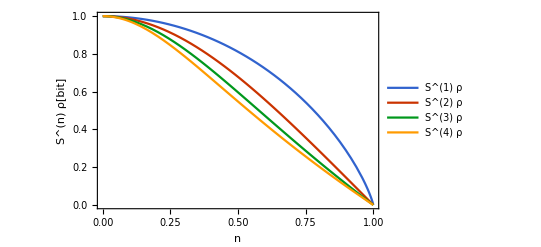

```mathematica
Plot[{-((1+n)/2)Log[2,(1+n)/2]-((1-n)/2)Log[2,(1-n)/2],-Log[2,(1+n^2)/2],-Log[2,(1+3n^2)/4]/2,-Log[2,(1+6n^2+n^4)/8]/3},{n,0,1},FrameLabel->{"\!\(|n|\)","\!\(S\^(n)\%ρ\)[bit]"},PlotLegends->Table[Style[StringTemplate["\!\(S\^(`1`)\%ρ\)"][n],"InlineFormula"],{n,4}]]
```

Shadow entropy

S_(ρ,sh)^(1)=∑_(a=1)^3 [-((1+n_a)/6)log((1+n_a)/6)-((1-n_a)/6)log((1-n_a)/6)],
S_(ρ,sh)^(2)=-log(3+n^2)/18,
S_(ρ,sh)^(3)=-1/2log(1+n^2)/36,
S_(ρ,sh)^(4)=-1/3log(3+6 n^2+∑_a n_a^4)/648,

```mathematica
Simplify@Total[(Flatten@Table[(1+b n[a])/6,{a,3},{b,{1,-1}}])^3]
```

1/36 (1+n[1]^2+n[2]^2+n[3]^2)

Details.

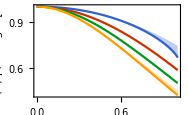

```mathematica
Plot[{Total[-((1+#)/6)Log[2,(1+#)/6]-((1-#)/6)Log[2,(1-#)/6]&/@(n Normalize@{1,0,0})]-Log[2,3],Total[-((1+#)/6)Log[2,(1+#)/6]-((1-#)/6)Log[2,(1-#)/6]&/@(n Normalize@{1,1,1})]-Log[2,3],-Log[2,(3+n^2)/18]-Log[2,3],-Log[2,(1+n^2)/36]/2-Log[2,3],-Log[2,(3+6n^2+Total[(n Normalize@{1,0,0})^4])/648]/3-Log[2,3],-Log[2,(3+6n^2+Total[(n Normalize@{1,1,1})^4])/648]/3-Log[2,3]},{n,0,1},PlotStyle->{Blue,None,Red,Green,Orange,None},Filling->{1->{2},5->{6}},FrameLabel->{"\!\(|n|\)","\!\(S\^(n)\%\(ρ,sh\)-log 3\) [bit]"}]
```

The uncertainty arise from the fact that Clifford is only unitary 3-design.

#### Numerical Experiments (Pauli)

##### Entropy

For a single qubit, the measurement entropy is positively correlated with the von Neumann entropy

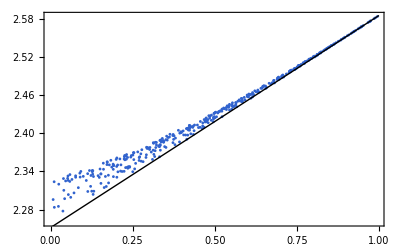

```mathematica
ListPlot[Table[Block[{Ν=1,ρ,Sρ,as,bs,kron,P,SP},
ρ=Chop[#/Tr[#]]&@(ConjugateTranspose[#].#)&@(RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ});
Sρ=Total[-# Log[2,#]]&@Eigenvalues@ρ;
as=Tuples[Range[3],Ν];
bs=Tuples[{1,-1},Ν];
kron[A_]:=A;
kron[A__]:=KroneckerProduct[A];
P=Table[Chop@Tr[ρ.(kron@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}]/3^Ν;
SP=Total[-# Log[2,#]]&@Flatten@P;
{Sρ,SP}],400],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{{0,2/3+Log[2,3]},{1,1+Log[2,3]}}]}]
```

For multiple qubits, the correlation is no longer prominent.

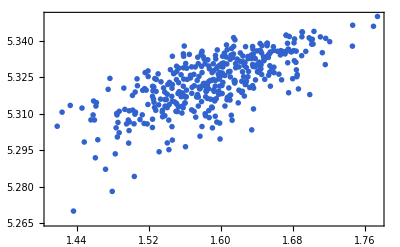

```mathematica
ListPlot[Table[Block[{Ν=3,ρ,Sρ,as,bs,kron,P,SP},
ρ=Chop[#/Tr[#]]&@(ConjugateTranspose[#].#)&@(RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ});
Sρ=Total[-# Log[#]]&@Eigenvalues@ρ;
as=Tuples[Range[3],Ν];
bs=Tuples[{1,-1},Ν];
kron[A_]:=A;
kron[A__]:=KroneckerProduct[A];
P=Table[Chop@Tr[ρ.(kron@@(Represent/@(σ[0]+b(σ/@a))/2))],{b,bs},{a,as}]/3^Ν;
SP=Total[-# Log[#]]&@Flatten@P;
{Sρ,SP}],400]]
```

##### Mutual Information

The shadow mutual information and the state mutual information do not have a definite relation, but when they both goes to 0 in the same way.

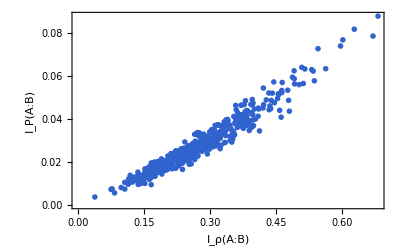

```mathematica
ListPlot[Table[Block[{Ν=2,ρ,ρA,ρB,IρAB,Ms,P,PA,PB,IPAB},
ρ=Chop[#/Tr[#]]&@(ConjugateTranspose[#].#)&@(RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ});
ρA=TensorContract[ArrayReshape[ρ,ConstantArray[2,2Ν]],{{1,3}}];
ρB=TensorContract[ArrayReshape[ρ,ConstantArray[2,2Ν]],{{2,4}}];
IρAB=(Total[-# Log[#]]&@Eigenvalues@ρA)+(Total[-# Log[#]]&@Eigenvalues@ρB)-(Total[-# Log[#]]&@Eigenvalues@ρ);
Ms=Represent/@Flatten@Table[(σ[0]+b σ[a])/2,{b,{1,-1}},{a,3}];
P=Chop@Table[Tr[KroneckerProduct[M1,M2].ρ],{M1,Ms},{M2,Ms}]/3^Ν;
PA=Total[P,{1}];
PB=Total[P,{2}];
IPAB=(Total[-# Log[#]]&@PA)+(Total[-# Log[#]]&@PB)-(Total[-# Log[#]]&@Flatten@P);
{IρAB,IPAB}
],500],FrameLabel->{"\!\(I\_ρ(A:B)\)","\!\(I\_P(A:B)\)"}]
```

#### Numerical Experiments (Haar)

##### Entropy (Single-Qubit)

Tetrahedron

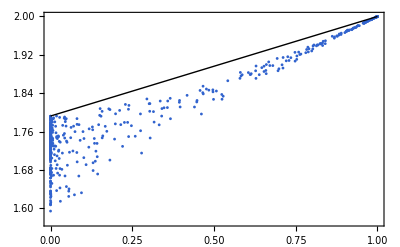

```mathematica
Block[{Ν=1,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Tetrahedron[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

Octahedron (Pauli)

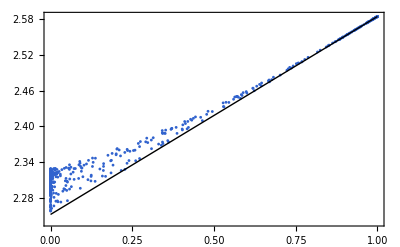

```mathematica
Block[{Ν=1,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Octahedron[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

Cube

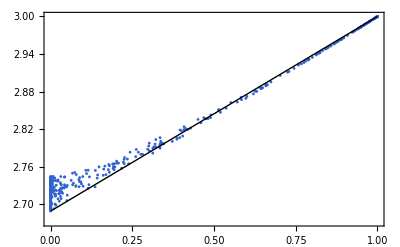

```mathematica
Block[{Ν=1,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Cube[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

Icosahedron

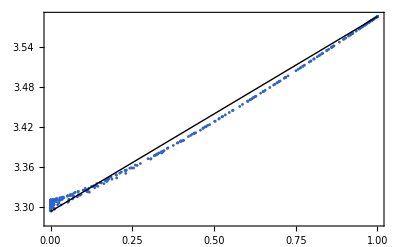

```mathematica
Block[{Ν=1,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Icosahedron[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

Dodecahedron

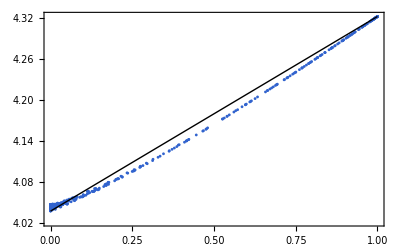

```mathematica
Block[{Ν=1,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Dodecahedron[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

##### Entropy (Double-Qubit)

Tetrahedron

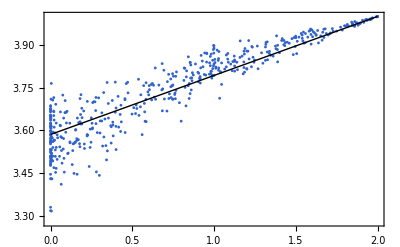

```mathematica
Block[{Ν=2,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Tetrahedron[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

Octahedron (Pauli)

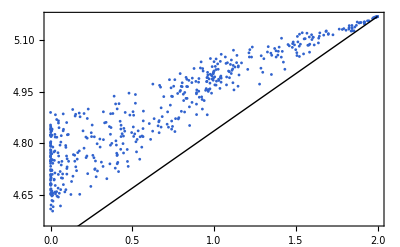

```mathematica
Block[{Ν=2,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Octahedron[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

Cube

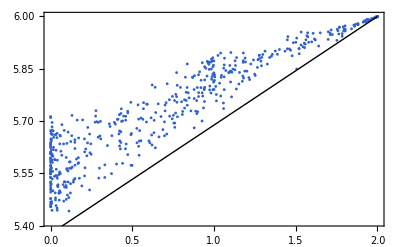

```mathematica
Block[{Ν=2,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Cube[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

Icosahedron

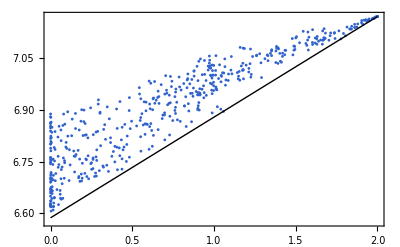

```mathematica
Block[{Ν=2,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Icosahedron[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

Dodecahedron

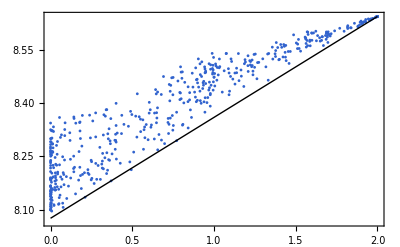

```mathematica
Block[{Ν=2,ns,pn,Zn,M,S},
ns=Normalize/@PolyhedronCoordinates[Dodecahedron[]];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
ListPlot[Table[Block[{U,p,ρ,P},
U=Orthogonalize[RandomVariate[NormalDistribution[],{2^Ν,2^Ν,2}].{1,ⅈ}];
p=#/Total[#]&[RandomReal[{0,1},2^Ν]^RandomReal[{0,20}]];
ρ=ConjugateTranspose[U].DiagonalMatrix[p].U;
P=Chop[tTr[{M,ρ},{{2,5},{3,4}}]]/Zn^Ν;
{S[p],S[P]}
],500],PlotStyle->AbsolutePointSize[2],Epilog->{Line[{Ν#,Ν If[#==0,S[pn],Log[2,Length@ns]]}&/@{0,1}]}]]
```

What is the pure state that maximizes the shadow entropy?

```mathematica
Block[{Ν=2,ns,pn,Zn,M,S,L},
ns=Normalize/@PolyhedronCoordinates[Octahedron[]];
Print[N@ns];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
L[A_List]:=Block[{z,P},
z=Normalize[A.{1,ⅈ}];
P=Chop[tTr[{M,z,Conjugate[z]},{{2,5},{3,4}}]]/Zn^Ν;
S[P]];
Block[{Lm,sol,Am,zm},
{Lm,sol}=FindMaximum[L[A],{A,RandomVariate[NormalDistribution[],{2^Ν,2}]}];
Am=A/.sol;
zm=Normalize[Am.{1,ⅈ}];
Print[Lm];
Print[zm/Sign[First@zm]];
Grid@Partition[Chop[Conjugate[zm].Represent[#].zm]&/@σ@@@Tuples[Range[0,3],Ν],4]
]
]
```

{{0.,1.,0.},{1.,0.,0.},{0.,-1.,0.},{-1.,0.,0.},{0.,0.,1.},{0.,0.,-1.}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

4.90937

{0.57735+2.77556×10^-17 ⅈ,0.288675-0.288675 ⅈ,-0.288675+0.288675 ⅈ,6.3062×10^-7-0.57735 ⅈ}

1. | -2.0816×10^-7 | -8.68922×10^-8 | -7.65733×10^-9
1.32419×10^-7 | -0.333333 | -0.666666 | -0.666667
1.62632×10^-7 | -0.666667 | -0.333334 | 0.666666
-8.33975×10^-8 | 0.666667 | -0.666666 | 0.333333

```mathematica
Block[{Ν=2,ns,pn,Zn,M,S,Os,H,L},
ns=Normalize/@PolyhedronCoordinates[Octahedron[]];
Print[N@ns];
pn=(1+#.First[ns])/2&/@ns;
Zn=Total[pn];pn=pn/Zn;
M=
Flatten[TensorProduct@@ConstantArray[SparseArray[Represent[(σ[0]+#.(σ/@Range[3]))/2]&/@ns],Ν],Table[i+3Range[0,Ν-1],{i,3}]];
S=Total[If[#==0.,0,-# Log[2,#]]&/@#]&;
Os=σ@@@Tuples[Range[0,3],Ν];
(*H[h_]:=Block[{H1},
H1=h.(Os/.{σ[0,_]:>0,σ[_,0]:>0});
H1+(H1/.{σ[a_,b_]:>σ[b,a]})];*)
H[h_]:=Block[{H1},
H1=h[[1]](σ[1,1]+σ[2,2]+σ[3,3])+h[[2]](σ[1,2]+σ[2,3]-σ[1,3]);
Expand[H1+(H1/.{σ[a_,b_]:>σ[b,a]})]];
L[h_List]:=Block[{z,P},
z=Last@First@SortBy[First]@Thread@Eigensystem@N@Represent@H[h];
P=Chop[tTr[{M,z,Conjugate[z]},{{2,5},{3,4}}]]/Zn^Ν;
S[P]];
Block[{Lm,sol,hm,zm},
{Lm,sol}=FindMaximum[L[h],{h,RandomReal[{-1,1},16]}];
hm=h/.sol;
zm=Last@First@SortBy[First]@Thread@Eigensystem@N@Represent@H[hm];
Print[Lm];Print[H[hm]];
Print[Grid@Partition[Chop[Conjugate[zm].Represent[#].zm]&/@Os,4]];
Eigensystem@Table[Chop@σTr[H[hm]·σ[a,b]],{a,3},{b,3}]
]
]
```

{{0.,1.,0.},{1.,0.,0.},{0.,-1.,0.},{-1.,0.,0.},{0.,0.,1.},{0.,0.,-1.}}

4.90937

-1.68126 σ[1,1]-0.684784 σ[1,2]+0.684784 σ[1,3]-0.684784 σ[2,1]-1.68126 σ[2,2]-0.684784 σ[2,3]+0.684784 σ[3,1]-0.684784 σ[3,2]-1.68126 σ[3,3]

1. | 0 | 0 | 0
0 | 0.333333 | 0.666667 | -0.666667
0 | 0.666667 | 0.333333 | 0.666667
0 | -0.666667 | 0.666667 | 0.333333

{{-9.46419,-9.46419,-1.24679},{{0.707107,0.707107,0.},{-0.408248,0.408248,0.816497},{0.57735,-0.57735,0.57735}}}

```mathematica
SortBy[First]@Thread@Eigensystem@Represent[-1.1(σ[1,1]+σ[2,2])-σ[3,3]]
```

{{-1.2,{0.,0.707107,0.707107,0.}},{-1.,{0.,0.,0.,1.}},{-1.,{1.,0.,0.,0.}},{3.2,{0.,-0.707107,0.707107,0.}}}

#### Random Vector

```mathematica
RandomVector[m_]:=
Block[{z=RandomReal[],nx,ny,nz},
nz=(m-2+4 z)/(1+Sqrt[(m-1)^2+4m z]);
{nx,ny}=Sqrt[1-nz^2]ReIm@Exp[ⅈ RandomReal[{0,2π}]];
{nx,ny,nz}];
RandomVector[m_,samples_]:=Table[RandomVector[m],samples];
```

#### Weak Measurement

```mathematica
Options[WeakMeasurements]={Axis->"Random"};
WeakMeasurements[ϵ_,Ν_,α0_,OptionsPattern[WeakMeasurements]]:=
Block[{measure,αs,outs},
Switch[OptionValue[Axis],
"Random",
measure[α_]:=Block[{n,nz},
Sow[n=RandomVector[Tanh[α]Tanh[ϵ]]];
nz=Last@n;
α+Log[(1+nz Tanh[ϵ/2])/(1-nz Tanh[ϵ/2])]],
"Fixed",
measure[α_]:=Block[{n},
Sow[n=RandomChoice[{1+Tanh[α]Tanh[ϵ],1-Tanh[α]Tanh[ϵ]}->{1,-1}]];
α+ϵ n]];
{αs,{outs}}=Reap[NestList[measure,α0,Ν]];
<|"αs"->αs,"outs"->outs|>]
```

#### Equal Earth Projection

```mathematica
EEP[{λ_,ϕ_}]:=Block[{θ=ArcSin[Sqrt[3]/2Sin[ϕ]],A1,A2,A3,A4},
{A1,A2,A3,A4}={1.340264,-0.081106,0.000893,0.003796};
{2Sqrt[3]λ Cos[θ]/(3 (9A4 θ^8+7A3 θ^6+3 A2 θ^2+A1)),A4 θ ^9+A3 θ^7+A2 θ^3+A1 θ}]
```

## Draft

### Single Qubit Case

#### Weak Measurement Ensemble

Consider a single qubit generating weak measurement outcomes following the probability distribution

p_dat(x)=(1+x·n)/2,

n is a 3-component vector parametrizing the density matrix of the qubit

ρ=(σ^0+n·σ)/2,

x is a 3-component vector representing the measurement outcome with the associated measurement operator

E_x=(σ^0+x·σ)/2.

It can be verified that Eq. (DisplayFormulaNumbered) is consistent with the measurement theory  p(x)=Tr E_x ρ.

#### Decoder Model

The decoder probability is given by

p(x|z)=(1+x·m(z))/2,

where we assume the decoder to be modeled by (single-layer perceptron, linear-activate-linear)

m(z)=m tanh (w z+b),

with m being a unit vector and w,b being real parameters to learn. The latent representation z is a single real scalar.

We fix the prior probability to normalized Gaussian

p(z)=1/(√(2π))e^(-z^2/2).

Then the model probability distribution is given by

p_mdl(x)=∫ⅆz p(x|z)p(z)=∫ⅆz (1+x·m tanh(w z+b))/(2 √(2π))e^(-z^2/2).

Using the approximation

∫ⅆz/(√(2π))  tanh(w z+b)e^(-z^2/2)≃tanh(b/(√(1+2 w^2))),

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-0.835178}. NIntegrate obtained -1.73472×10^-18 and 8.62339×10^-17 for the integral and error estimates.

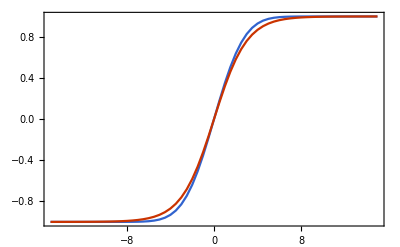

```mathematica
Block[{tanh},
tanh[w_?NumericQ,b_?NumericQ]:=NIntegrate[Tanh[w z+b]Exp[-z^2/2]/Sqrt[2π],{z,-∞,∞}];
Block[{w=2},ListLinePlot@Thread@Table[{{b,tanh[w,b]},{b,Tanh[b/Sqrt[1+2w^2]]}},{b,-15.,15.,0.5}]]]
```

Verification.

we have

p_mdl(x)=(1+x·m tanh(b (1+2 w^2)^(-1/2)))/2.

Comparing with p_dat(x) in Eq. (DisplayFormulaNumbered), the optimal solution should follow from

m tanh(b (1+2 w^2)^(-1/2))=n.

As we over-parametrized the model, the solution is not unique. One idea is to require m to be the unit vector along the direction of n and rescale its length by adjusting b and w.

The tricky part is that for the GHZ state, the reduced density matrix on each single qubit is trivial, i.e. n=0. But hidden behind, there are actually two modes: ±n both happened with 1/2 probability. Each time the system only collapse to one mode, and subsequent weak measurement will confirm the mode. If we train the machine using sequential data produced by one mode, the machine should learn about the preferential axis m to lie along n even if the ensemble does not have a preferential direction n.

Lesson: we can not use sequential measurement (in time) to train, because the sequential data only contain a single mode. ⇒ We should use spacial data to train.

#### Encoder Model

Given the latent prior and the decoder model, the optimal encoder model follows from the Bayes formula

p(z|x)=(p(x|z)p(z))/(p(x))
=1/(√(2π))(1+x·m tanh(w z+b))/(1+x·m tanh(b (1+2 w^2)^(-1/2)))e^(-z^2/2).

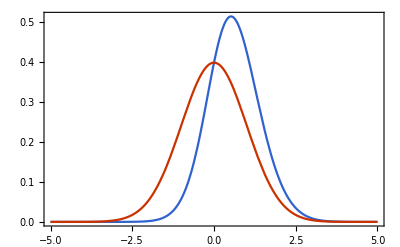

```mathematica
Block[{m={0,0,1},w=1,b=0,pzx},
pzx[z_,x_]:=(1+x.m Tanh[w z+b])/(1+x.m Tanh[b/Sqrt[1+2w^2]])Exp[-z^2/2]/Sqrt[2π];
Block[{x=Normalize@RandomVariate[NormalDistribution[],3]},Plot[{pzx[z,x],Exp[-z^2/2]/Sqrt[2π]},{z,-5,5}]]]
```

It can be approximated by a shifted Gaussian

q(z|x)=1/(√(2π σ))e^(-(z-ζ(x))^2/(2 σ^2)).

If we observe a sequence of x, assuming the events are independent, the inference probability for z follows from the product rule

∏_x q(z|x)∝e^(-∑_x (z-ζ(x))^2/(2 σ^2))=e^(-(N (z-⟨ζ⟩)^2)/(2 σ^2)).

The machine will be confident about its knowledge of z when

σ/(√N)≪⟨ζ⟩.

Moreover, it is possible to keep track of the mean and standard deviation

1/(Σ(T))^2=∑_(t=1:T) 1/(σ(x_t))^2,
Ζ(T)=(Σ(T))^2∑_(t=1:T) (ζ(x_t))/(σ(x_t))^2,

We can then plot Ζ(T)±Σ(T) to see how the mean and standard deviation of the latent variable evolves with respect to time.

Another way to estimate is to use the Bayesian estimation

p(z|{x})=(p({x}|z)p(z))/(p({x}))∝p(z)∏_x p(x|z)

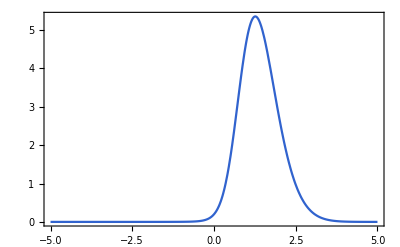

```mathematica
Block[{x=0.1,n=50},
Plot[(1+x Tanh[z])^n/2 Exp[-z^2/2]/Sqrt[2π],{z,-5,5},PlotRange->All]]
```

This also amplifies the bias.

A question to answer is that why measurement must be a many-body effect? If we do not have sufficient number of environment qubits, we will not have sufficient number of observations to establish confidence. So we need to show the confidence curve for different system size and demonstrate that the many-body environment is crucial.

#### Linearized Approximation

Let us consider the simplest case where all neural network functions are linear. Then the decoder model reads

p(x|z)=(1+x·m z)/2,

and the encoder model reads

q(z|x)=1/(√(2π))e^(-(z-x·m')^2/2).

According to Eq. (DisplayFormulaNumbered), the loss function reads

ℒ=𝔼_(z\[Distributed]q(z|x))ln p(x|z)-D_KL(q(z|x)||p(z))
=𝔼_(z\[Distributed]q(z|x))(ln (1+x·m z)/2+(z-x·m')^2/2-z^2/2),

consider that x is a weak measurement outcome which is close to zero, we can approximate

ln(1+x·m z)≃x·m z-(x·m)^2 z^2/2+…

therefore

ℒ=𝔼_(z\[Distributed]q(z|x))(x·(m-m')z-(x·m)^2 z^2/2+1/2(x·m')^2)
=x·(m-m') x·m'-(x·m)^2 (1+(x·m')^2)/2+1/2(x·m')^2
=-1/2 (x·m)^2(x·m')^2-1/2(x·(m-m'))^2.

Further average over x\[Distributed]p_dat(x),

ℒ=-1/2 m^2 m'^2-1/2(m-m')^2,

so maximizing ℒ leads to a trivial result m=m'=0. This implies that either linearized model is not good enough or the single-qubit signal can not drive the VAE to learn about the classical modes.

### IOVM Idea

#### Spherical POVM

##### On-Site Case

Define the single-qubit IOVM (where )

E_m=(σ^0+m·σ)/2.

We have

trace properties

Tr E_m=1, Tr E_m E_m'=(1+m·m')/2,

isometry (assuming ∫_(S^2) ⅆm =1)

∫_(S^2) ⅆm E_m⊗E_m ᵀ
=1/4∫_(S^2) ⅆm (σ^0+m·σ)⊗(σ^0+m·σ)ᵀ
=1/4∫_(S^2) ⅆm (σ^0+m_1 σ^1+m_2 σ^2+m_3 σ^3)⊗(σ^0+m_1 σ^1-m_2 σ^2+m_3 σ^3)
=1/4(σ^00+m^2/3(σ^11-σ^22+σ^33)).

```mathematica
Integrate[x^2,{x,y,z}∈Sphere[]]/(4π)
```

1/3

Details.

Therefore if we choose m^2=3, we can obtain

∫_(S^2) ⅆm E_m⊗E_m ᵀ=1/2(1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1)

```mathematica
Represent[σ[0,0]+σ[1,1]-σ[2,2]+σ[3,3]]//MatrixForm
```

(2 | 0 | 0 | 2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
2 | 0 | 0 | 2)

Details.

In terms of diagrams,

=1/2.

It corresponds to the projection operator of EPR state along the vertical direction, but it also gives the isometry along the horizontal direction.

##### Many-Body Case

For multiple sites, we define

the indefinite-operator valued measure (IOVM)

E[m]=⊗_i(1+m_i·σ_i)/2,

the measurement operator (overs non-local observables)

M[x]=1/2(1+∑_[μ] x_[μ]σ^[μ]).

The Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) generalized to

Tr E[m]=1,
Tr M[x]E[m]=1/2(1+∑_[μ] x_[μ]∏_i m_i^μ_i).

∫ⅅ[m] E[m]⊗E[m]ᵀ=2^-n id.

Given a density matrix ρ, we can generate a joint probability distribution

p[m]=2^n Tr E[m]ᵀρ.

such that the density matrix can be reconstructed by

ρ=∫ⅅ[m]E[m]p[m],

which gives the proposed model in Eq. (DisplayFormulaNumbered). However, since E[m]ᵀ is not positive definite, this makes p[m] potentially indefinite as well, which causes a problem. But in practice, it seems that p[m] might still exist for certain states (e.g. the EPR state).

Under measurement, the probability to generate the outcome x is

p(x)=Tr M[x]ρ=∫ⅅ[m]p(x|m)p[m],
p(x|m)=Tr M[x]E[m].

Again, there is no guarantee that p(x|m) is positive definite.

Comments:

If we restrict m to be unit vectors, then E[m] is a POVM, but we can not establish the isometry from the contraction of E[m]⊗E[m]ᵀ, and the tomography will fail. The fundamental reason is that the POVM model can not capture all the entanglement structure of a density matrix.

If we generalize m to be arbitrary vectors, then E[m] is no longer positive definite, but the isometry can be established, and the state tomography can be realized. But working with indefinite operator E[m], the conditional probability of measurement outcome p(x|m)=Tr M[x]E[m] can be negative. The workaround is to consider weak enough measurement to avoid negative p(x|m).

#### Representing EPR State

EPR state (2-qubit)

EPR=1/(√2)(00+11).

Density matrix

ρ=EPREPR=1/4(σ^00+σ^11-σ^22+σ^33).

```mathematica
Abstract[#⊗#&@(SparseArray[{1->1,-1->1},4]/Sqrt[2])]
```

1/4 σ[0,0]+1/4 σ[1,1]-1/4 σ[2,2]+1/4 σ[3,3]

Details.

Distribution of m, according to Eq. (DisplayFormulaNumbered),

p[m]=4Tr E[m]ᵀρ=1+m11 m21-m12 m22+m13 m23,

```mathematica
4σTr[σTranspose[CircleTimes@@Table[(σ[0]+Sum[Indexed[m,{i,a}] σ[a],{a,3}])/2,{i,2}]]·Abstract[#⊗#&@(SparseArray[{1->1,-1->1},4]/Sqrt[2])]]//Expand
```

1+m11 m21-m12 m22+m13 m23

Details.

where m_(1,2) is assumed to be on a sphere of √3 length. One can see that p[m] indeed become negative, e.g. when m_1=m_2=(0,√3,0), p[m]=-2. This seems to be a problem. But one may question if Eq. (DisplayFormulaNumbered) is the only solution for p[m]. Since the only key is to produce the desired expectation for the polynomials of m, there might be other solution of p[m] that can achieve the same expectations. To check this, we first evaluate the expectation values based on the indefinite distribution in Eq. (DisplayFormulaNumbered). We can indeed verify that

𝔼[m11 m21]=-𝔼[m12 m22]=𝔼[m13 m23]=1,

```mathematica
Integrate[m1⊗m2(1+9m1.DiagonalMatrix[{1,-1,1}].m2),m1∈Sphere[],m2∈Sphere[]]/(4π)^2
```

{{1,0,0},{0,-1,0},{0,0,1}}

Integrate.

and the remaining expectations are zero. However, the same expectations can be reproduced by another positive definite p[m]

p[m]=δ(m_1=n)δ(m_2=(1,-1,1)⊙n),

where n is uniformly distributed on a sphere of √3 length.

Conclusion:

What is important is the expectation value not the distribution. There are multiple possibilities of p[m] that gives the same expectation, we need to pick the positive ones.

The isometry relation is not useful, because p[m] in Eq. (DisplayFormulaNumbered) obtained from isometry relation is not the positive definite one. By using the trace formula Tr E[m]ᵀρ to construct the distribution, the result always looks like 1+… as Eq. (DisplayFormulaNumbered), then we are wasting our positivity on this background shift 1 of the distribution (we are weakening the sharpness of the distribution, and hence we will have to use negative probabilities somewhere to compensate).

#### Representing GHZ State

GHZ state (multiple qubits)

GHZ=1/(√2)(0… 0+1… 1).

Density matrix ρ=GHZGHZ. Now we assume that ρ is given by Eq. (DisplayFormulaNumbered), we have

∫ⅅ[m]E[m]p[m]=GHZGHZ.

By comparing both sides of Eq. (DisplayFormulaNumbered), we can obtain the required expectation of m_i=(m_i1,m_i2,m_i3) under p[m]. In the following, we only present the non-trivial expectation values.

2-qubit

```mathematica
Block[{n=2},DeleteCases[Reduce@First@Last@Reap[Collect[Collect[CircleTimes@@Table[σ[0]+Sum[Indexed[m,{i,a}] σ[a],{a,3}],{i,n}],_σ,𝔼]-Abstract[2^(n-1)#⊗#&@SparseArray[{1->1,-1->1},2^n]],_σ,Sow[#==0]&];],_==0]]
```

𝔼[1]==1&&𝔼[m11 m21]==1&&𝔼[m12 m22]==-1&&𝔼[m13 m23]==1

4-qubit

```mathematica
Block[{n=4},DeleteCases[Reduce@First@Last@Reap[Collect[Collect[CircleTimes@@Table[σ[0]+Sum[Indexed[m,{i,a}] σ[a],{a,3}],{i,n}],_σ,𝔼]-Abstract[2^(n-1)#⊗#&@SparseArray[{1->1,-1->1},2^n]],_σ,Sow[#==0]&];],_==0]]
```

𝔼[1]==1&&𝔼[m33 m43]==1&&𝔼[m23 m43]==1&&𝔼[m23 m33]==1&&𝔼[m11 m21 m31 m41]==1&&𝔼[m11 m21 m32 m42]==-1&&𝔼[m11 m22 m31 m42]==-1&&𝔼[m11 m22 m32 m41]==-1&&𝔼[m12 m21 m31 m42]==-1&&𝔼[m12 m21 m32 m41]==-1&&𝔼[m12 m22 m31 m41]==-1&&𝔼[m12 m22 m32 m42]==1&&𝔼[m13 m43]==1&&𝔼[m13 m33]==1&&𝔼[m13 m23]==1&&𝔼[m13 m23 m33 m43]==1

6-qubit

```mathematica
Block[{n=6},DeleteCases[Reduce@First@Last@Reap[Collect[Collect[CircleTimes@@Table[σ[0]+Sum[Indexed[m,{i,a}] σ[a],{a,3}],{i,n}],_σ,𝔼]-Abstract[2^(n-1)#⊗#&@SparseArray[{1->1,-1->1},2^n]],_σ,Sow[#==0]&];],_==0]]
```

𝔼[1]==1&&𝔼[m53 m63]==1&&𝔼[m43 m63]==1&&𝔼[m43 m53]==1&&𝔼[m33 m63]==1&&𝔼[m33 m53]==1&&𝔼[m33 m43]==1&&𝔼[m33 m43 m53 m63]==1&&𝔼[m23 m63]==1&&𝔼[m23 m53]==1&&𝔼[m23 m43]==1&&𝔼[m23 m43 m53 m63]==1&&𝔼[m23 m33]==1&&𝔼[m23 m33 m53 m63]==1&&𝔼[m23 m33 m43 m63]==1&&𝔼[m23 m33 m43 m53]==1&&𝔼[m11 m21 m31 m41 m51 m61]==1&&𝔼[m11 m21 m31 m41 m52 m62]==-1&&𝔼[m11 m21 m31 m42 m51 m62]==-1&&𝔼[m11 m21 m31 m42 m52 m61]==-1&&𝔼[m11 m21 m32 m41 m51 m62]==-1&&𝔼[m11 m21 m32 m41 m52 m61]==-1&&𝔼[m11 m21 m32 m42 m51 m61]==-1&&𝔼[m11 m21 m32 m42 m52 m62]==1&&𝔼[m11 m22 m31 m41 m51 m62]==-1&&𝔼[m11 m22 m31 m41 m52 m61]==-1&&𝔼[m11 m22 m31 m42 m51 m61]==-1&&𝔼[m11 m22 m31 m42 m52 m62]==1&&𝔼[m11 m22 m32 m41 m51 m61]==-1&&𝔼[m11 m22 m32 m41 m52 m62]==1&&𝔼[m11 m22 m32 m42 m51 m62]==1&&𝔼[m11 m22 m32 m42 m52 m61]==1&&𝔼[m12 m21 m31 m41 m51 m62]==-1&&𝔼[m12 m21 m31 m41 m52 m61]==-1&&𝔼[m12 m21 m31 m42 m51 m61]==-1&&𝔼[m12 m21 m31 m42 m52 m62]==1&&𝔼[m12 m21 m32 m41 m51 m61]==-1&&𝔼[m12 m21 m32 m41 m52 m62]==1&&𝔼[m12 m21 m32 m42 m51 m62]==1&&𝔼[m12 m21 m32 m42 m52 m61]==1&&𝔼[m12 m22 m31 m41 m51 m61]==-1&&𝔼[m12 m22 m31 m41 m52 m62]==1&&𝔼[m12 m22 m31 m42 m51 m62]==1&&𝔼[m12 m22 m31 m42 m52 m61]==1&&𝔼[m12 m22 m32 m41 m51 m62]==1&&𝔼[m12 m22 m32 m41 m52 m61]==1&&𝔼[m12 m22 m32 m42 m51 m61]==1&&𝔼[m12 m22 m32 m42 m52 m62]==-1&&𝔼[m13 m63]==1&&𝔼[m13 m53]==1&&𝔼[m13 m43]==1&&𝔼[m13 m43 m53 m63]==1&&𝔼[m13 m33]==1&&𝔼[m13 m33 m53 m63]==1&&𝔼[m13 m33 m43 m63]==1&&𝔼[m13 m33 m43 m53]==1&&𝔼[m13 m23]==1&&𝔼[m13 m23 m53 m63]==1&&𝔼[m13 m23 m43 m63]==1&&𝔼[m13 m23 m43 m53]==1&&𝔼[m13 m23 m33 m63]==1&&𝔼[m13 m23 m33 m53]==1&&𝔼[m13 m23 m33 m43]==1&&𝔼[m13 m23 m33 m43 m53 m63]==1

We conclude that the expectation values of m for the GHZ state are given by the following general rules

∀A∈Subset[{1,…,n},even]:
𝔼[∏_(i∈A) m_i3]=1,

∀a_i=1,2&{a_i} has even number of 2:
𝔼[∏_(i=1)^n m_(i a_i)]=∏_(i=1)^n ⅈ^(δ(a_i==2)).

We may reproduce these behaviors by assuming m_ia to be Ising variables,

m_ia=(-)^z_ia=±1, z_ia∈ℤ_2.

The requirements in Eq. (DisplayFormulaNumbered) can be easily achieved. We only need to assign

m_13=m_23=…=m_n3=±1,

meaning that all the 3rd component of m_i are the same and take values in ±1 with equal probability.

Eq. (DisplayFormulaNumbered) is harder to deal with. We must make sure that these conditions do not contradict with each other and also do not rule out all degrees of freedoms in the system. For a size-n system, there are 2n in-plane (1 and 2) components of m_i. Assuming them to be Ising variables, we have totally 2n of them. What about the number of constrains? The number of constrains is given by

∑_(k=0)^(n/2) C_n^(2k)=2^(n-1).

```mathematica
Sum[Binomial[n,2k],{k,0,n/2}]
```

2^(-1+n)

Sum.

So the number of constrains grows exponentially with n which is must faster than the linear grow of the number of variables 2n. In fact for n>4, we always have more constrains. The constrains can be expressed in a linear algebra approach using the ℤ_2 variable z_ia=0,1,

∑_(i a) z_(i a)P_(i a,k)=b_k,

where k labels the constrain and P_(i a,k) is a ℤ_2 matrix and b_k=0,1 denotes the constrain.

We can first check that the ℤ_2 rank of P, which is the number of independent constrains. We found

rank_ℤ_2 P=n,

```mathematica
Table[Block[{P},
P=SparseArray[Flatten[MapIndexed[Table[{ia,First@#2}->1,{ia,#1}]&,Join[Complement[Range[n],#],n+#]&/@Subsets[Range[n],{0,n,2}]]],{2n,2^(n-1)}];
n->MatrixRank[P,Modulus->2]],{n,2,6}]
```

{2→2,3→3,4→4,5→5,6→6}

MatrixRank.

meaning that P is not full ranked. Note that there are 2n variables, but only n independent constraint, so there remain n independent free variables.

Unfortunately, the solution of Eq. (DisplayFormulaNumbered) only exists for n=2. For larger n, the constrains contradict with each other and there is no solution.

```mathematica
Block[{n=3,P,b},
P=SparseArray[Flatten[MapIndexed[Table[{ia,First@#2}->1,{ia,#1}]&,Join[Complement[Range[n],#],n+#]&/@Subsets[Range[n],{0,n,2}]]],{2n,2^(n-1)}];
b=Mod[(Length/@Subsets[Range[n],{0,n,2}])/2,2];
LinearSolve[Transpose[P],b,Modulus->2];
Column@{MatrixForm[{b}],MatrixForm[P]}->Column@{MatrixForm[{b}],MatrixForm[RowReduce[P,Modulus->2]]}]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

(0 | 1 | 1 | 1)
(1 | 0 | 0 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 0
0 | 1 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 1)→(0 | 1 | 1 | 1)
(1 | 0 | 0 | 1
0 | 1 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

However, this is not the end of the story. Because in Eq. (DisplayFormulaNumbered), we have shown that there exist a set of tetra IOVM, which has been proven to be able to do tomography. The above failure only indicates that the assumption that all components of m are Ising variables is problematic, this restricts m_i to the 8 corners of a cube, which is actually not invertible.

### Latent Space

#### Entropy of Dipolar Distribution

```mathematica
Block[{d=3,n=2,p},
p[θ_]:=(1+m Cos[θ])/(2π^(d/2)/Gamma[d/2]);{Integrate[p[θ]^n 2π^((d-1)/2)/Gamma[(d-1)/2]Sin[θ]^(d-2),{θ,0,π}],Simplify[2π^((d-1)/2)Gamma[n+1]/(2π^(d/2)/Gamma[d/2])^n 
Sum[m^k Gamma[(k+1)/2]/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2]),{k,0,n,2}]]}]
```

{(3+m^2)/(12 π),(3+m^2)/(12 π)}

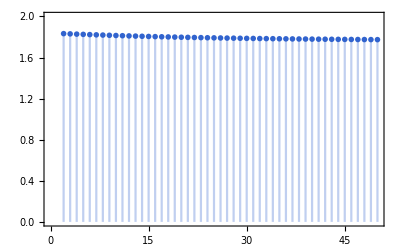

```mathematica
Block[{d=2,m=0.1,S},
S[n_]:=Log[2π^((d-1)/2)Gamma[n+1]/(2π^(d/2)/Gamma[d/2])^n 
Sum[m^k Gamma[(k+1)/2]/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2]),{k,0,n,2}]]/(1-n);
DiscretePlot[S[n],{n,2,50},PlotRange->{0,2}]]
```

```mathematica
Block[{S},
S[n_]:=Log[2π^((d-1)/2)Gamma[n+1]/(2π^(d/2)/Gamma[d/2])^n 
Sum[m^k Gamma[(k+1)/2]/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2]),{k,0,n,2}]]/(1-n);
S[2]//FullSimplify]
```

Log[2]-Log[((d+m^2) π^(-d/2) Gamma[d/2])/d]

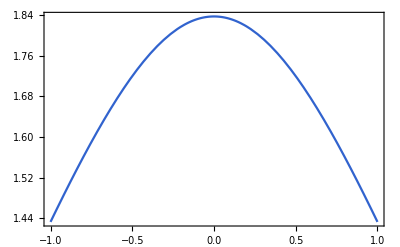

```mathematica
Block[{d=2},
Plot[-Log[(1+m^2/d)/(2π^(d/2)/Gamma[d/2])],{m,-1,1}]]
```

```mathematica
Block[{d=2,n=2},
2π^((d-1)/2)/Gamma[(d-1)/2]/(2π^(d/2)/Gamma[d/2])^n Integrate[(1+m Cos[θ])^n Sin[θ]^(d-2),{θ,0,π}]]
```

(2+m^2)/(4 π)

```mathematica
Block[{d=4},Integrate[(1+m Cos[θ])^n Sin[θ]^(d-2),{θ,0,π}]]
```

1/8 (4+m^2) π

```mathematica
Integrate[Cos[θ]^a Sin[θ]^b,{θ,0,π}]
```

ConditionalExpression[((1+(-1)^a) Gamma[(1+a)/2] Gamma[(1+b)/2])/(2 Gamma[1/2 (2+a+b)]),Re[a]>-1&&Re[b]>-1]

```mathematica
Block[{d=3,n=2},
Simplify[2π^((d-1)/2)/Gamma[(d-1)/2]/(2π^(d/2)/Gamma[d/2])^n 

Sum[m^k (Gamma[n+1]Gamma[(k+1)/2]Gamma[(d-1)/2])/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2]),{k,0,n,2}]]]
```

(3+m^2)/(12 π)

```mathematica
Gamma[n+1]Gamma[(k+1)/2]Gamma[(d-1)/2]/(Gamma[k+1]Gamma[n-k+1]Gamma[(k+d)/2])/.{n->1,k->0}
```

(√π Gamma[1/2 (-1+d)])/Gamma[d/2]

#### Loss Function

Let us focus on the fixed axis model and try to understand how the optimization works. In this case, x=(…,x_i,…) is a string of x_i=±1. To simplify the problem, we will further assume that the latent space is one-dimensional z∈ℝ.

We first evaluate the reconstruction loss. According to Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered),

ℒ_re=-𝔼_(z\[Distributed]q(z|x))log p(x|z)
=-1/(√(2π)σ_z)∫∑_i log(1+x_i m(z))exp(-(z-μ_z)^2/(2 σ_z^2))ⅆz.

In the weak measurement limit, x_i m(z) is expected to be small, so we can expand the logarithm

log(1+x_i m(z))≃x_i m(z)-(x_i^2(m(z))^2)/2.

Substitute Eq. (DisplayFormulaNumbered) to Eq. (DisplayFormulaNumbered), we have

ℒ_re≃-∑_i x_i ⟨m(z)⟩+1/2∑_i x_i^2⟨(m(z))^2⟩
=-N x̄⟨m(z)⟩+1/2 N OverBar[x^2]⟨(m(z))^2⟩,

where we have introduce the bracket notation for average under the Gaussian distribution of latent variable

⟨□⟩=1/(√(2π)σ_z)∫□exp(-(z-μ_z)^2/(2 σ_z^2))ⅆz,

and we have defined

x̄=1/N∑_i x_i, OverBar[x^2]=1/N∑_i x_i^2.

For our data set, OverBar[x^2] is basically a constant. For the fixed axis case, x_i=±1, so OverBar[x^2]=1 precisely. For the random axis case, in the weak measurement limit, OverBar[x^2]=1/3 is pretty stable. As we are considering the fixed axis model, we will just set OverBar[x^2] to identity.

As m(z) is a ℝ→ℝ function, it admits the power series expansion

m(z)≃a+b z+….

Here we assume z to be small and truncate the expansion at linear order. With this Eq. (DisplayFormulaNumbered) becomes

ℒ_re=-Nx̄(a+b ⟨z⟩)+1/2 N (a^2+2a b ⟨z⟩+b^2⟨z^2⟩),

and ⟨z^k⟩ is the kth moment of the latent distribution. Based on Eq. (DisplayFormulaNumbered), we have

⟨z^1⟩=μ_z,⟨z^2⟩=μ_z^2+σ_z^2,

so Eq. (DisplayFormulaNumbered) becomes

ℒ_re=-Nx̄(a+b μ_z)+1/2 N (a^2+2a b μ_z+b^2(μ_z^2+σ_z^2)),

Combining with the KL loss

ℒ_kl=1/2(μ_z^2+σ_z^2-1)-log σ_z,

the total loss is

ℒ=-Nx̄(a+b μ_z[x])+1/2 N (a^2+2a b μ_z[x]+b^2(μ_z^2[x]+σ_z^2[x]))+1/2(μ_z^2[x]+σ_z^2[x]-1)-log σ_z[x].

Both μ_z and σ_z will be function of the input x. Together with them, coefficients a and b will also be the variational.

The loss will be evaluated on the data set, where x is drawn form the distribution p(x).

#### Gradient Descent Dynamics

The functional optimization is still difficult to analyze. Based on our numerical observation, the VAE somehow (magically) learns to make μ_z linear in x̄ and σ_z to be a constant. If we follow this ansatz

μ_z[x]=c+d x̄, σ_z[x]=e,

the loss function becomes

ℒ=-Nx̄(a+b (c+d x̄))+1/2 N (a^2+2a b  (c+d x̄)+b^2( (c+d x̄)^2+e^2))+1/2( (c+d x̄)^2+e^2-1)-log e.

See Eq. (DisplayFormulaNumbered) for a simplified version with a=c=0 and KL regularization.

For the parameter θ=a,b,c,d,e, the learning dynamics is generally given by the gradient descent

∂_t θ=-∂_θ ℒ.

We obtain the dynamical equation of parameters

∂_t a=-N(a+b c)-N x̄(b d-1),
∂_t b=-N(a c+b (c^2+e^2))-N x̄((a +2 b c) d-c)-N (x̄)^2 d(b d-1),
∂_t c=-(c+N b (a+b c))- x̄(d+N b(b d-1)),
∂_t d=- x̄(c+N b (a+b c))- (x̄)^2(d+N b(b d-1)),
∂_t e=1/e-e-N b^2 e.

```mathematica
Collect[-D[-Ν x(a+b (c+d x))+Ν/2(a^2+2a b(c+d x)+b^2((c+d x)^2+e^2))+1/2((c+d x)^2+e^2)-Log[e],#],x,Expand]&/@{a,b,c,d,e}
```

{-a Ν-b c Ν+x (Ν-b d Ν),-a c Ν-b c^2 Ν-b e^2 Ν+x (c Ν-a d Ν-2 b c d Ν)+x^2 (d Ν-b d^2 Ν),-c-a b Ν-b^2 c Ν+x (-d+b Ν-b^2 d Ν),x (-c-a b Ν-b^2 c Ν)+x^2 (-d+b Ν-b^2 d Ν),1/e-e-b^2 e Ν}

Derivatives.

Let us first analyze the dynamics of e=σ_z. Without KL regularization, it follows ∂_t e=-N b^2 e, under which e flows to 0 inevitably. KL regularization plays an important role to maintain a finite variance

e^2=1/(1+N b^2).

Note: if the KL loss strength is controlled by λ (i.e. ℒ=ℒ_re+λ ℒ_kl), the saddle point is give by e^2=λ/(N b^2+λ).

```mathematica
e^2/.Solve[λ(1/e-e)-Ν b^2e==0,e]
```

{λ/(λ+b^2 Ν),λ/(λ+b^2 Ν)}

Solve

#### Saddle Point Solutions

In the batch training, the r.h.s. of the differential equation Eq. (DisplayFormulaNumbered) will be evaluated in an ensemble of input samples x (each has a different x̄ following the distribution p(x̄) that may bifurcate). Every power of x̄ should be ensemble averaged. Let us consider the case with reflection symmetry, i.e. p(x̄)=p(-x̄), then x̄ averages to 0. We define the average of (x̄)^2 to be

ϵ^2=∫ⅆ x̄ (x̄)^2 p(x̄).

The ensemble average can also be done on the level of loss function. It is very important to assume that ϵ^2 is independent of N. If x were a collection of independent Gaussian variables, the mean x̄ would follow a Gaussian distribution with a variance that decreases with N, as ϵ^2∼1/N, then the distribution p(x̄) will not bifurcate but just become more concentrated. The fact that p(x̄) bifurcates indicates that ϵ^2 will stop decreasing with N when bifurcation has happened.

Then Eq. (DisplayFormulaNumbered) becomes

∂_t a=-N(a+b c),
∂_t b=-N(a c+b (c^2+e^2))-N ϵ^2 d(b d-1),
∂_t c=-(c+N b (a+b c)),
∂_t d=- ϵ^2(d+N b(b d-1)).

This is still complicated. Let us further take the large-N limit, but keep N ϵ^2 fixed at order one, the leading terms will be

∂_t a=-N(a+b c),
∂_t b=-N c (a+b c),
∂_t c=-N b (a+b c),
∂_t d=-N ϵ^2 b (b d-1).

There are two saddle point solutions:

Type A (trivial, forgetful)

a=b=0,c,d∈ℝ,e=1
⇒m(z)=0, μ_z=c+d x̄,σ_z=1.

Type B (nontrivial, following)

a=-b c,b d=1,e=N^(-1/2) b^-1
⇒m(z)=(z-c)/d→x̄, μ_z=c+d x̄,σ_z=d N^(-1/2).

```mathematica
Solve[{a+b c==0,a c+b(c^2)==0,b(a+b c)==0,b(b d-1)==0},{a,b,c,d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→0,b→0},{a→-b c,d→1/b}}

Solve.

Now let us put the saddle point solutions back to Eq. (DisplayFormulaNumbered), so as to analyze the sub-leading effects.

Type A saddle (a=b=0,c,d∈ℝ,e=1)

∂_t a=0,
∂_t b=-N b (c^2+e^2)+N ϵ^2 d,
∂_t c=-c,
∂_t d=- ϵ^2d.

We can see that c,d will decay to zero. But the flow of d is very slow (of the rate ϵ^2). While d is finite, it tends to drive the growth of b in the same direction as d, but the dominate decay term in b will control b at a very low level b=ϵ^2 d (c^2+1)^-1 which will also slowly vanish as d vanishes. So in the long time limit, the ultimate type A saddle is

a=b=c=d=0, e=1
⇒m(z)=0, μ_z[x]=0,σ_z[x]=1.

Type B saddle (a=-b c,b d≃1,e=N^(-1/2) b^-1)

∂_t a=0
∂_t b=-b^-1-N ϵ^2 d(b d-1),
∂_t c=-c,
∂_t d=- ϵ^2(d+N b(b d-1)).

The dynamics of a,c is relatively simple: they just exponentially decay to zero, the decay of c is driven by the KL regulation gradually, a will quickly follow c as a=-b c, together they vanish.

The dynamics of b,d is more complicated. We can not assume b d=1 to hold exactly. The saddle point solution is (the sign of b and d are correlated to be the same)

b=±ϵ/2(1+√(1-4/(N ϵ^2))),
d=±1/ϵ.

```mathematica
Solve[{1/b+Ν ϵ^2 d(b d-1)==0,d+Ν b(b d-1)==0},{b,d}]//FullSimplify
```

{{b→-ϵ/2-(√(-4+ϵ^2 Ν))/(2 √Ν),d→-1/ϵ},{b→1/2 (ϵ-(√(-4+ϵ^2 Ν))/(√Ν)),d→1/ϵ},{b→1/2 (-ϵ+(√(-4+ϵ^2 Ν))/(√Ν)),d→-1/ϵ},{b→1/2 (ϵ+(√(-4+ϵ^2 Ν))/(√Ν)),d→1/ϵ}}

Solve.

Interestingly, the solution only exist for N ϵ^2≥4.

In the long time limit, the ultimate type B saddle is

a=c=0, b=(ϵ/2)(1+(1-4/N ϵ^2)^(1/2)),d=1/ϵ,e=1/(√(1+N b^2))
⇒m(z)=ϵ/2(1+√(1-4/(N ϵ^2)))z,
 μ_z[x]=(x̄)/ϵ,
σ_z[x]=√(1/2(1-√(1-4/(N ϵ^2)))).

It turns out that the saddle point solution is only valid in large N ϵ^2. The singularity at N ϵ^2=4 is not observed in actual numerics (by solving Eq. (DisplayFormulaNumbered)). We may have made some mistake in the above analysis.

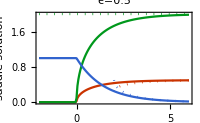

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν ϵ^2d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{b[t1],ϵ/2(1+Sqrt[1-4/(Ν ϵ^2)]),d[t1],1/ϵ,e[t1]^2,1/2(1-Sqrt[1-4/(Ν ϵ^2)])}],{lgΝ,0,8,0.05}],
PlotStyle->{Red,Directive[Dotted,Red],Green,Directive[Dotted,Green],Blue,Directive[Dotted,Blue]},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","saddle solution"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\) actual","\!\(b\) large-N","\!\(d\) actual","\!\(d\) large-N","\!\(e\^2\) actual","\!\(e\^2\) large-N"}),ImageSize->200]]
```

##### Implications of Type B Saddle

We expect that the standard deviation σ_z of the encoding distribution q(z|x) consistently drops with N ϵ^2. The dependence is universal.

σ_z^2[x]=1/2(1-√(1-4/(N ϵ^2))).

The following figure shows this dependence, red: analytic formula from Eq. (DisplayFormulaNumbered), black: machine learning result (on random axis model). The trend is consistent. The details don’t quite match because the models are different, or the training has not converged.

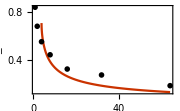

```mathematica
Show[{Plot[{Sqrt[(1-Sqrt[1-4/x])/2]},{x,4,64},PlotStyle->Red,PlotRange->{0,All}],ListPlot[{{1,0.84},{2,0.68},{4,0.55},{8,0.44},{16,0.32},{32,0.27},{64,0.18}}.{{1,0},{0,1}},PlotStyle->Black]},FrameLabel->{"\!\(N ϵ\^2\)","\!\(σ\_z\)"},ImageSize->180]
```

We can also investigate how the polarization m(μ_z) follows the magnetization x̄. We use the ratio to quantify how well the fidelity of the autoencoder in the data space. The ratio increases with N ϵ^2, and the behavior is universal.

(m(μ_z[x]))/(x̄)=1/2(1+√(1-4/(N ϵ^2))).

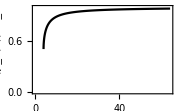

```mathematica
Plot[(1/2)(1+Sqrt[1-4/x]),{x,0,64},PlotRange->{0,1},PlotStyle->Black,FrameLabel->{"\!\(N ϵ\^2\)","\!\(m(μ\_z(x))/x\&_\)"},ImageSize->180]
```

We can also quantify the fidelity of the autoencoder in the latent space. This amounts to ask, given a latent variable z, generate the configuration x (whose mean x̄ is given by m(z)), then infer the latent representation, how much we can recover the latent variable? This gives the same ratio

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z=1/2(1+√(1-4/(N ϵ^2))).

Interestingly, the latent space fidelity and the latent space variance add up to a constant

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z+σ_z^2[x]=1.

This relation could be universal to the task?

##### Effect of KL Regulation

If we consider the KL loss appears with strength λ, the solution of e^2 is modified to

e^2=λ/(N b^2+λ).

Consider the Type B saddle point, where a=-b c, Eq. (DisplayFormulaNumbered) becomes (we will only focus on the equations for b and d)

∂_t b=-λ/b-N ϵ^2 d(b d-1),
∂_t d=- ϵ^2(λ d+N b(b d-1)).

We obtain the saddle point solution

b=ϵ/2(1+√(1-(4λ)/(N ϵ^2))),
d=1/ϵ,
e^2=1/2(1-√(1-(4λ)/(N ϵ^2))).

```mathematica
Solve[{λ/b+Ν ϵ^2d(b d-1)==0,λ d+Ν b(b d-1)==0},{b,d}]//FullSimplify
```

{{b→-(ϵ Ν+√(Ν (-4 λ+ϵ^2 Ν)))/(2 Ν),d→-1/ϵ},{b→(ϵ Ν-√(Ν (-4 λ+ϵ^2 Ν)))/(2 Ν),d→1/ϵ},{b→(-ϵ Ν+√(Ν (-4 λ+ϵ^2 Ν)))/(2 Ν),d→-1/ϵ},{b→(ϵ Ν+√(Ν (-4 λ+ϵ^2 Ν)))/(2 Ν),d→1/ϵ}}

Solve.

As we can see, the solution exists as long as N ϵ^2≥4λ. So the critical N ϵ^2 is indeed tunable by λ. However, amazingly, Eq. (DisplayFormulaNumbered) still holds for any choice of λ.

#### Dynamics

Solve the differential equation.

∂_t a=-N(a+b c),
∂_t b=-N(a c+b (c^2+e^2))-N ϵ^2 d(b d-1),
∂_t c=-(c+N b (a+b c)),
∂_t d=- ϵ^2(d+N b(b d-1)),
∂_t e=1/e-e-N b^2 e.

We can observe how parameters converges to their saddle point values.

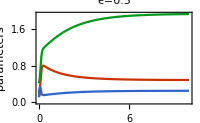

```mathematica
Block[{Ν=64,ϵ=0.5,t1=10,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν ϵ^2d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==RandomReal[],b[0]==ϵ RandomReal[],c[0]==RandomReal[],d[0]==RandomReal[]/ϵ,e[0]==RandomReal[]/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
Plot[{b[t],d[t],e[t]},{t,0,t1},PlotStyle->{Red,Green,Blue},FrameLabel->{"\!\(t\)","parameters"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(e\)"}),ImageSize->200]]
```

There is a (mean-field) phase transition between A phase (forgetting) and B phase (following). The transition occurs at N ϵ^2=1. No chaotic behavior observed around the transition.

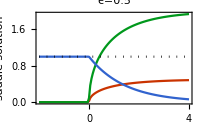

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν ϵ^2d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{b[t1],d[t1],e[t1]^2,b[t1]d[t1]+e[t1]^2}],{lgΝ,0,6,0.05}],
PlotStyle->{Red,Green,Blue,Directive[Dotted,Black]},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","saddle solution"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(e\^2\)","\!\(b d+e\^2\)"}),ImageSize->200]]
```

In the B phase, as N ϵ^2 increases, μ_z gradually grows larger than σ_z, then the consensus is formed.

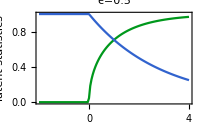

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν ϵ^2d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{d[t1]ϵ,e[t1]}],{lgΝ,0,6,0.05}],
PlotStyle->{Green,Blue},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","latent statistics"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(μ\_z[x]\)","\!\(σ\_z[x]\)"}),ImageSize->200]]
```

To explore the dynamical phase space flow, we reduce the differential equation Eq. (DisplayFormulaNumbered) to two variables b,d, by setting a=c=0 and e^2=1/(N b^2+1)

∂_t b=-(N b)/(N b^2+1)-N ϵ^2 d(b d-1),
∂_t d=- ϵ^2(d-N b (b d-1)),

which can be obtained from the following effective loss function

ℒ=-N ϵ^2 b d+1/2 d^2 ϵ^2(N b^2+1)+log (N b^2+1).

```mathematica
-Collect[D[-Ν ϵ^2 b d+1/2d^2 ϵ^2(Ν b^2+1)+(1/2)Log[Ν b^2+1],#],ϵ,Factor]&/@{b,d}
```

{-d (-1+b d) ϵ^2 Ν-(b Ν)/(1+b^2 Ν),-ϵ^2 (d-b Ν+b^2 d Ν)}

Gradient check.

Flow diagrams under different N ϵ^2.

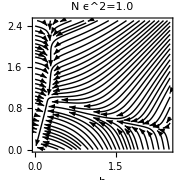
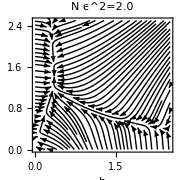
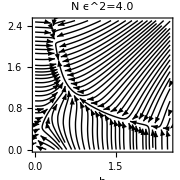

```mathematica
Row@Table[Block[{ϵ=0.5},
StreamPlot[{-Ν b/(Ν b^2+1)-Ν ϵ^2d(b d-1),-ϵ^2(d+Ν b(b d-1))},{b,0,2.5},{d,0,2.5},PlotRangePadding->Scaled[.02],FrameLabel->{"\!\(b\)","\!\(d\)"},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][Ν ϵ^2],StreamScale->Full,StreamPoints->Fine,StreamStyle->Directive[Black,AbsoluteThickness[1]],ImageSize->180]],{Ν,{4,8,16}}]
```

Details near the transition.

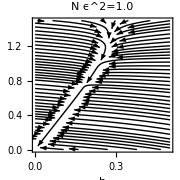
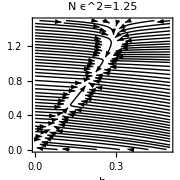

```mathematica
Row@Table[Block[{ϵ=0.5},
StreamPlot[{-Ν b/(Ν b^2+1)-Ν ϵ^2d(b d-1),-ϵ^2(d+Ν b(b d-1))},{b,0,0.5},{d,0,1.5},PlotRangePadding->Scaled[.02],FrameLabel->{"\!\(b\)","\!\(d\)"},PlotLabel->StringTemplate["\!\(N ϵ\^2=`1`\)"][Ν ϵ^2],StreamScale->Full,StreamPoints->Fine,StreamStyle->Directive[Black,AbsoluteThickness[1]],ImageSize->180]],{Ν,{4,5}}]
```

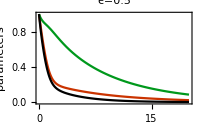

```mathematica
Block[{Ν=2,ϵ=0.5,t1=20,a,b,c,d,e},
{b,d}=NDSolveValue[{
b'[t]==-Ν b[t]/(Ν b[t]^2+1)-Ν ϵ^2d[t](b[t]d[t]-1),
d'[t]==-ϵ^2(d[t]+Ν b[t](b[t]d[t]-1)),
b[0]==1,d[0]==1},{b,d},{t,0,t1}];
Plot[{b[t],d[t],b[t] d[t]},{t,0,t1},PlotStyle->{Red,Green,Black},FrameLabel->{"\!\(t\)","parameters"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(b d\)"}),ImageSize->200]]
```

#### Cross Over Behavior

The above toy model is a little careless about the variance of x̄ in Eq. (DisplayFormulaNumbered). In fact, according to Eq. (DisplayFormulaNumbered), the variance actually goes like

∫ⅆ x̄ (x̄)^2 p(x̄)=ϵ^2+1/N.

In this case, we need to modify our differential equation to

∂_t a=-N(a+b c),
∂_t b=-N(a c+b (c^2+e^2))-(N ϵ^2+1)d(b d-1),
∂_t c=-(c+N b (a+b c)),
∂_t d=- (ϵ^2+1/N)(d+N b(b d-1)),
∂_t e=1/e-e-N b^2 e.

With this modification, the transition is gone. We can only observe a crossover behavior. In this case b=ϵ remains a constant (meaning that m(z)=ϵ z can learn about the weak measurement strength, even if the machine has no idea of the state yet).

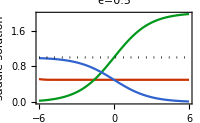

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν (ϵ^2+1/Ν)d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-(ϵ^2+1/Ν)(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{b[t1],d[t1],e[t1]^2,b[t1]d[t1]+e[t1]^2}],{lgΝ,-4,8,0.05}],
PlotStyle->{Red,Green,Blue,Directive[Dotted,Black]},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","saddle solution"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(b\)","\!\(d\)","\!\(e\^2\)","\!\(b d+e\^2\)"}),ImageSize->200]]
```

The latent statistics also only have a cross over behavior. The behavior looks quite universal.

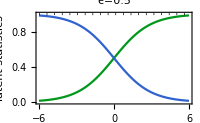

```mathematica
Block[{ϵ=0.5},
ListLinePlot[Thread@Table[Block[{Ν=2^lgΝ,t1=1000,a,b,c,d,e},
{a,b,c,d,e}=NDSolveValue[{
a'[t]==-Ν(a[t]+b[t] c[t]),
b'[t]==-Ν(a[t]c[t]+b[t](c[t]^2+e[t]^2))-Ν (ϵ^2+1/Ν)d[t](b[t]d[t]-1),
c'[t]==-(c[t]+Ν b[t](a[t]+b[t]c[t])),
d'[t]==-(ϵ^2+1/Ν)(d[t]+Ν b[t](b[t]d[t]-1)),
e'[t]==1/e[t]-e[t]-Ν b[t]^2 e[t],
a[0]==0,b[0]==1,c[0]==0,d[0]==1,e[0]==1/Sqrt[Ν]},{a,b,c,d,e},{t,0,t1}];
{Log[2,Ν ϵ^2],#}&/@{d[t1]ϵ,e[t1]^2,d[t1]ϵ+e[t1]^2}],{lgΝ,-4,8,0.05}],
PlotStyle->{Green,Blue,Directive[Black,Dotted]},FrameLabel->{"\!\(log\_2(N ϵ\^2)\)","latent statistics"},PlotLabel->StringTemplate["\!\(ϵ=`1`\)"][ϵ],PlotLegends->(Style[#,FontFamily->"CMU"]&/@{"\!\(μ\_z[x]\)","\!\(σ\_z\%2[x]\)"}),ImageSize->200]]
```

Let us try to understand this universal curve. First we set a=c=0, Eq. (DisplayFormulaNumbered) reduces to

∂_t b=-N b e^2-(N ϵ^2+1)d(b d-1),
∂_t d=- (ϵ^2+1/N)(d+N b(b d-1)),
∂_t e=1/e-e-N b^2 e.

We first solve ∂_t e=0 and find e^2=1/(N b^2+1). Substitute into Eq. (DisplayFormulaNumbered), we obtain

∂_t b=-(N b)/(N b^2+1)-(N ϵ^2+1)d(b d-1),
∂_t d=- (ϵ^2+1/N)(d+N b(b d-1)).

```mathematica
Solve[{Ν b/(Ν b^2+1)+(Ν ϵ^2+1)d(b d-1)==0,(ϵ^2+1/Ν)(d+Ν b(b d-1))==0},{b,d}]
```

{{b→0,d→0},{b→-ϵ,d→-(ϵ Ν)/(1+ϵ^2 Ν)},{b→ϵ,d→(ϵ Ν)/(1+ϵ^2 Ν)}}

Solve.

We find three saddle point solution

A:{ | b=0
d=0, B_±:{ | b=±ϵ
d=±(N ϵ)/(1+N ϵ^2).

Focus on the B_+ solution, it implies

m(z)=ϵ z, μ_z[x]=(N ϵ)/(1+N ϵ^2)x̄, σ_z^2[x]=1/(1+N ϵ^2).

The fidelity-variance sum rule

𝔼_(x\[Distributed]p(x|z))μ_z[x]/z+σ_z^2[x]=1.